```mathematica
Quit[]
```

```mathematica
(*warning, some of the integral methods need to be checked!*)
```

```mathematica
Rinf[k_,l_,r_]:= 2 k Exp[π/(2 k a0)] Abs[Gamma[l+1 - I/(k a0)]]/Factorial[2 l + 1](2 k r)^l Exp[-I k r]Hypergeometric1F1[I/(k a0)+l+1,2l+2, 2I k r];
RinfC[k_,l_,r_]:= 2 k Exp[π/(2 k a0)] Abs[Gamma[l+1 - -I/(k a0)]]/Factorial[2 l + 1](2 k r)^l Exp[I k r]Hypergeometric1F1[-I/(k a0)+l+1,2l+2,- 2I k r];
Rb[n_,l_,r_]:=√((2/(n a0))^3 Factorial[n - l - 1]/(2 n Factorial[n+l]))Exp[-r/(n a0)]((2 r)/(n a0))^l LaguerreL[n-l-1,2l+1,(2r)/(n a0)];
```

```mathematica
Integrate[Rb[2,1,r]^2 r^2,{r,0,Infinity}]
```

ConditionalExpression[1, Re[a0]>0]

```mathematica
ωerg[n_,α_,μ_,l_]:=μ (1-α^2/(2 n^2)-α^4/(8 n^4));
(*ωerg[n_,α_,μ_,l_]:=μ (1-α^2/(2 n^2)-α^4/(8 n^4));*)
```

```mathematica
FullSimplify[α^4/(8 n^4)+α^4/n^3(-6/(2l+1)+2/n)]
```

((17+34 l-48 n) α^4)/(8 (1+2 l) n^4)

```mathematica
Series[ωerg[5,α,μ,4]+ωerg[4,α,μ,4] - ωerg[4,α,μ,2],{α,0,2}]
```

μ-(μ α^2)/50+O[α]^3

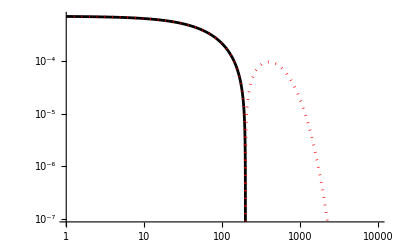

```mathematica
LogLogPlot[{Rb[2, 0,r]/.{a0->100},Abs[Rb[2, 0,r]]/.{a0->100}},{r,1,10000},PlotStyle->{Black,{Red,Dotted}}]
```

```mathematica
FullSimplify[1/Rb[2, 0,r](-1/r^2 D[r^2 D[Rb[2, 0,r],r],r]-2 α^2/r Rb[2, 0,r])/.{a0->1/α^2}]
```

-α^4/4

```mathematica
FullSimplify[1/Rb[2, 0,r](-1/r^2 D[r^2 D[(Rb[2, 0,r]^2)^(1/2),r],r]-2 α^2/r(Rb[2, 0,r]^2)^(1/2))/.{a0->1/α^2},r>0&&α>0]
```

1/4 α^4 Sign[-2+r α^2]

```mathematica
Rb[5, 0,.1]/.{a0->100}
```

0.000178707

```mathematica
Integrate[(ⅇ^(-√kind2 r) ( HypergeometricU[1-α^2/(√kind2),2,2 √kind2 r]))^2 r^2,{r,0,Infinity}]
```

ConditionalExpression[MeijerG[{{1,2,3+α^2/(√kind2)},{}},{{2,3},{1+α^2/(√kind2)}},1]/(8 kind2^(3/2) Gamma[-α^2/(√kind2)] Gamma[1-α^2/(√kind2)]), ]

```mathematica
RbNEW[α_,kind2_,r_]:=(ⅇ^(-√kind2 r) ( HypergeometricU[1-α^2/(√kind2),2,2 √kind2 r]))/(√(MeijerG[{{1,2,3+α^2/(√kind2)},{}},{{2,3},{1+α^2/(√kind2)}},1]/(8 kind2^(3/2) Gamma[-α^2/(√kind2)] Gamma[1-α^2/(√kind2)])));
```

```mathematica
tt=FullSimplify[Rinf[k,l,r]RinfC[k,l,r]]
```

(4^(1+l) ⅇ^(π/(a0 k)) k^2 (k r)^(2 l) Abs[Gamma[1-ⅈ/(a0 k)+l]] Abs[Gamma[1+ⅈ/(a0 k)+l]] Hypergeometric1F1[1-ⅈ/(a0 k)+l,2 (1+l),-2 ⅈ k r] Hypergeometric1F1[1+ⅈ/(a0 k)+l,2 (1+l),2 ⅈ k r])/Gamma[2 (1+l)]^2

```mathematica
FullSimplify[Normal[Series[tt,{r,Infinity,0}]],k>0&&r>0&&a0>0&&l>0]
```

-(2^(-(2 ⅈ)/(a0 k)) ⅇ^(π/(a0 k)-2 ⅈ k r) (-ⅈ k r)^(-(2 ⅈ)/(a0 k)) (k r)^(-2 l) Abs[Gamma[1-ⅈ/(a0 k)+l]] Abs[Gamma[1+ⅈ/(a0 k)+l]] (2^((2 ⅈ)/(a0 k)) ⅇ^(2 ⅈ k r) (-ⅈ k r)^l (k r)^((2 ⅈ)/(a0 k)) Gamma[1-ⅈ/(a0 k)+l]-(ⅈ k r)^l Gamma[1+ⅈ/(a0 k)+l])^2)/(r^2 Gamma[1-ⅈ/(a0 k)+l]^2 Gamma[1+ⅈ/(a0 k)+l]^2)

```mathematica
Limit[tt,r->Infinity]
```

lim_(r→∞) (4^(1+l) ⅇ^(π/(a0 k)) k^2 (k r)^(2 l) Abs[Gamma[1-ⅈ/(a0 k)+l]] Abs[Gamma[1+ⅈ/(a0 k)+l]] Hypergeometric1F1[1-ⅈ/(a0 k)+l,2 (1+l),-2 ⅈ k r] Hypergeometric1F1[1+ⅈ/(a0 k)+l,2 (1+l),2 ⅈ k r])/Gamma[2 (1+l)]^2

```mathematica
Rb[3,2,GM]^2/.{a0->1/α^2}
```

(8 ⅇ^(-(2 α^2)/3) α^14)/98415

```mathematica
(N211 Rb[2,1,GM]^2)/(μ fa^2)/.{a0->1/(α μ)}
```

(ⅇ^(-GM α μ) GM^2 N211 α^5 μ^4)/(24 fa^2)

```mathematica
(N322 Rb[3,2,GM]^2)/(μ fa^2)/.{a0->1/(α μ)}
```

(8 ⅇ^(-2/3 GM α μ) GM^4 N322 α^7 μ^6)/(98415 fa^2)

```mathematica
Clear[α]
```

```mathematica
Rb[n,n-1,GM]/.{a0->1/(α μ)}/.{GM μ -> α}
```

2^n ⅇ^(-α^2/n) (α^2/n)^(-1+n) √((α^3 μ^3)/(n^4 (-1+2 n)!))

```mathematica
Clear[C]
```

Clear::wrsym: Symbol C is Protected.

```mathematica
FullSimplify[ξ B(Cc αem)/fa √(N211/μ)2^n  (α^2/n)^(-1+n) √((α^3 μ^3)/(n^4 (-1+2 n)!))/.{n->3},α>0&&μ>0]
```

(2 √(2/15) B Cc √N211 α^(11/2) αem μ ξ)/(81 fa)

```mathematica
16((2 √(2/15) B Cc √N211 α^(11/2) αem μ ξ)/(81 fa))^4
```

(1024 B^4 Cc^4 N211^2 α^22 αem^4 μ^4 ξ^4)/(9685512225 fa^4)

```mathematica
N[1/36]
```

0.0277778

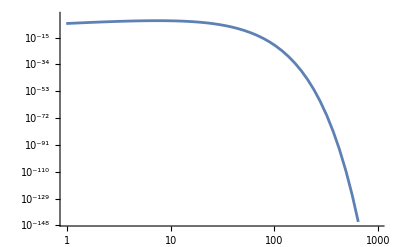

```mathematica
LogLogPlot[Rb[3,2,r]^2/.{a0->1/α^2}/.{α->0.9},{r,0,1000}]
```

```mathematica
Series[((r^2+a^2)^2)/(r^2-2r +a^2),{r,Infinity,1}]
```

r^2+2 r+(4+a^2)+8/r+O[1/r]^2

```mathematica
D[Rb[n,l,r],r]
```

```mathematica
Series[D[Rb[],r]/Rb[n,l,r]/.{n->2,l->1,a0->1/(α μ)},{r,Infinity,1}]
```

-(α μ)/2+1/r+O[1/r]^2

```mathematica
Series[FullSimplify[D[r D[Rb[n,l,r],r],r ]]/(α^2 r Rb[n,l,r] ω^2)/.{n->2,l->1,a0->1/(α μ)},{r,Infinity,1}]
```

μ^2/(4 ω^2)-(3 μ)/(2 (α ω^2) r)+O[1/r]^2

```mathematica
FullSimplify[Integrate[Rb[2,1,r] r^3,{r,0,Infinity}],a0>0]
```

64 √6 a0^(5/2)

```mathematica
1/r^2/.{r->1/α^(5/2)}
```

α^5

```mathematica
Series[ω^2-μ^2/.{ω->μ(1-α^2)},{α,0,4}]
```

-2 μ^2 α^2+μ^2 α^4+O[α]^5

```mathematica
Series[ω^2/.{ω->μ(1-α^2)},{α,0,4}]
```

μ^2-2 μ^2 α^2+μ^2 α^4+O[α]^5

```mathematica
1/r^3/.{r->1/α^(5/2)}
```

α^(15/2)

## trying something

```mathematica
Block[{n=2},FullSimplify[1/Rinf[k,0,r]((μ^2-ω^2)Rinf[k,0,r]+-1/r^2 D[r^2 D[Rinf[k,0,r],r],r]-2 μ α Rinf[k,0,r]/r)/.{a0->1/(μ α)},a0>0&&r>0&&n∈Integers]]
```

k^2+μ^2-ω^2

```mathematica
FullSimplify[1/Rinf[k,0,r](-1/r^2 D[r^2 D[Rinf[k,0,r],r],r]-2 μ α Rinf[k,0,r]/r)/.{a0->1/(μ α)},a0>0&&r>0]
```

k^2

```mathematica
FullSimplify[1/RinfC[k,0,r](-1/r^2 D[r^2 D[RinfC[k,0,r],r],r]-2 μ α RinfC[k,0,r]/r)/.{a0->1/(μ α)},a0>0&&r>0]
```

k^2

```mathematica
Block[{n=2},FullSimplify[1/Rb[n,0,r]((μ^2-ω^2)Rb[n,0,r]+-1/r^2 D[r^2 D[Rb[n,0,r],r],r]-2 μ α Rb[n,0,r]/r)/.{a0->1/(μ α)},a0>0&&r>0&&n∈Integers]]
```

-1/4 (-4+α^2) μ^2-ω^2

```mathematica
Expand[-1/4 (-4+α^2) μ^2-ω^2]
```

μ^2-(α^2 μ^2)/4-ω^2

```mathematica
test2[n_,l_,r_]:=Exp[-r/(n a0)]((2 r)/(n a0))^-m LaguerreL[n-l-1,2l+1,(2r)/(n a0)]
```

```mathematica
Block[{n=4},FullSimplify[1/test2[n,l,r](-1/r^2 D[r^2 D[test2[n,l,r],r],r]-2 μ α test2[n,l,r]/r-Λ^2 test2[n,l,r])/.{a0->1/(μ α)},a0>0&&r>0]]/.{l->0}
```

-(16 ((-1+m) m+r^2 Λ^2)-8 m r α μ+r^2 α^2 μ^2+(40 m r α μ (1-(r α μ)/2+1/16 r^2 α^2 μ^2-1/480 r^3 α^3 μ^3))/(1-(3 r α μ)/4+1/8 r^2 α^2 μ^2-1/192 r^3 α^3 μ^3))/(16 r^2)

```mathematica
Normal[Series[-(16 ((-1+m) m+r^2 Λ^2)-8 m r α μ+r^2 α^2 μ^2+(40 m r α μ (1-(r α μ)/2+1/16 r^2 α^2 μ^2-1/480 r^3 α^3 μ^3))/(1-(3 r α μ)/4+1/8 r^2 α^2 μ^2-1/192 r^3 α^3 μ^3))/(16 r^2),{α,0,2}]]
```

(-((-1+m) m)-r^2 Λ^2)/r^2-(2 m α μ)/r+1/16 α^2 (-μ^2-10 m μ^2)

```mathematica
Solve[(m-m^2-k^2 r^2)/r^2==0,m]
```

{{m→1/2 (1-√(1-4 k^2 r^2))},{m→1/2 (1+√(1-4 k^2 r^2))}}

```mathematica
FullSimplify[Rb[2,1,r]^2 Rb[3,2,r] 1/(α)^(3/2)/.{a0->1/(μ α)}/.{μ->α},α>0]
```

(ⅇ^(-(4 r α^2)/3) r^4 α^(31/2))/(486 √30)

```mathematica
sln=y[r]/.DSolve[{D[y[r],{r,2}]==S0 ⅇ^(-(4 r α^2)/3) r^4 α^(31/2)-2 D[y[r],r]/r- 2 α^4 y[r]-2 α^2 y[r]/r,y[100]==0,y'[100]==0},y[r],r]⟦1⟧;
```

```mathematica
test=Normal[Series[sln,{r,0,0}]]
```

(2 ⅈ C[2]-√2 π S0 α^(33/2) ∫_1^0 ⅇ^(-4/3 α^2 K[2]) BesselJ[1,2 √2 α √K[2]] K[2]^(11/2)ⅆK[2])/(2 π r α^2)+1/π(π C[1]+2 ⅈ C[2]-4 ⅈ EulerGamma C[2]-√2 π^2 S0 α^(33/2) ∫_1^0 ⅇ^(-4/3 α^2 K[1]) BesselY[1,2 √2 α √K[1]] K[1]^(11/2)ⅆK[1]-√2 π S0 α^(33/2) ∫_1^0 ⅇ^(-4/3 α^2 K[2]) BesselJ[1,2 √2 α √K[2]] K[2]^(11/2)ⅆK[2]+2 √2 EulerGamma π S0 α^(33/2) ∫_1^0 ⅇ^(-4/3 α^2 K[2]) BesselJ[1,2 √2 α √K[2]] K[2]^(11/2)ⅆK[2]-4 ⅈ C[2] Log[√2 √r α]+2 √2 π S0 α^(33/2) (∫_1^0 ⅇ^(-4/3 α^2 K[2]) BesselJ[1,2 √2 α √K[2]] K[2]^(11/2)ⅆK[2]) Log[√2 √r α])

```mathematica
FullSimplify[Series[test,{α,0,16}],α>0&&r>0]
```

(ⅈ C[2])/(π r α^2)-(ⅈ (ⅈ π C[1]-2 C[2]+4 EulerGamma C[2]+2 C[2] Log[2 r α^2]))/π-(((-6+7 r) S0) α^(31/2))/(42 r)+O[α]^(33/2)

```mathematica
Series[(432 √30 α^(35/2) (256 α^8-480 α^4 β+81 β^2))/((4 α^2-3 ⅈ √β)^6 (4 α^2+3 ⅈ √β)^6),{α,0,16}]
```

-(61776 (√30 α^24) α^(3/2))/((-4 ⅈ α^2+3 √(α^4))^6 (4 ⅈ α^2+3 √(α^4))^6)+O[α]^(33/2)

```mathematica
FullSimplify[(61776 (√30 α^24) α^(3/2))/((-4 ⅈ α^2+3 √(α^4))^6 (4 ⅈ α^2+3 √(α^4))^6),α>0]
```

(61776 √(6/5) α^(3/2))/48828125

```mathematica
Series[μ^2-(μ(1-α^2))^2,{α,0,2}]
```

2 μ^2 α^2+O[α]^3

```mathematica
N[35/2]
```

17.5

```mathematica
DSolve[D[y[r],{r,2}]==(ⅇ^(-(4 r α^2)/3) r^4 α^(31/2))/(486 √30)r,y[r],r]
```

{{y[r]→-(ⅇ^(-(4 r α^2)/3) α^(7/2) (-18225 r-32805/(2 α^2)-9720 r^2 α^2-3240 r^3 α^4-720 r^4 α^6-96 r^5 α^8))/(82944 √30)+C[1]+r C[2]}}

```mathematica
Series[-(ⅇ^(-(4 r α^2)/3) α^(7/2) (-18225 r-32805/(2 α^2)-9720 r^2 α^2-3240 r^3 α^4-720 r^4 α^6-96 r^5 α^8))/(82944 √30),{r,0,0}]
```

(27 √(15/2) α^(3/2))/2048+O[r]^1

```mathematica
srcT=Interpolation[Import["/Users/samuelwitte/Dropbox/Axion_SR/src/test_store/source_test.dat"]];
outp=Interpolation[Import["/Users/samuelwitte/Dropbox/Axion_SR/src/test_store/test_RAD.dat"]];
outp2=Interpolation[Import["/Users/samuelwitte/Dropbox/Axion_SR/src/test_store/test_RAD_i.dat"]];
```

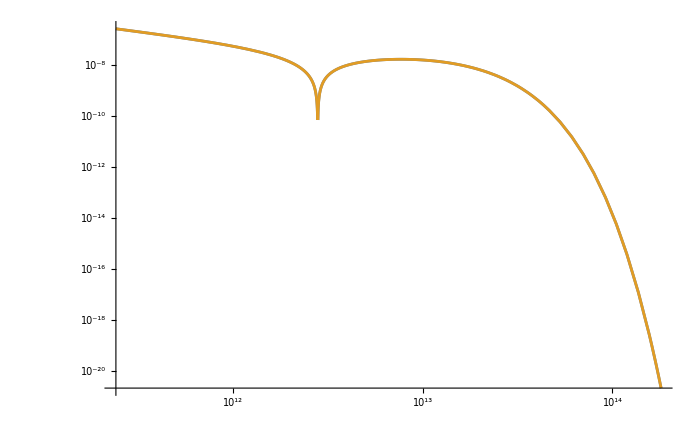

```mathematica
LogLogPlot[{Abs[outp2[x]],Abs[outp[x]]},{x,2.4 10^11, 1.805 10^14},PlotRange->All,ImageSize->700]
```

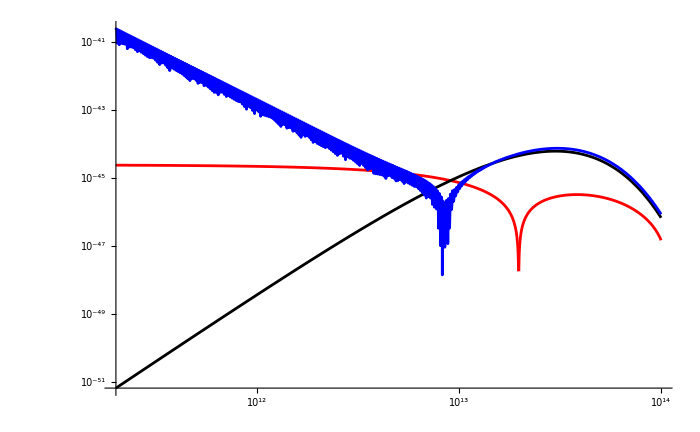

```mathematica
val=0;
Do[
If[n>l+1,
CG = Block[{m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
hold=1 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,l,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];

coef=Rb[n,l,r](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
val+= (μ^2-ωnew^2)coef -1/r^2 D[r^2 D[coef,r],r]- (2 α μ coef)/r;
]
,{n,1,7},{l,0,0}];

newTry= ((μ^2-ωnew^2)test[r]-1/r^2 D[r^2 D[test[r],r],r]- (2 α μ test[r])/r)10^-20;
Block[{α=.1,μ=10^-12},LogLogPlot[{Abs[val],1/(2μ)^(3/2)Rb[n1,l1,r] Rb[n2,l2,r]Rb[n3,l3,r]/.{a0-> 1/(μ α)},Abs[newTry] 10^1.5},{r,2 10^11,10^14},PlotStyle->{Red,Black,Blue},ImageSize->700]]
```

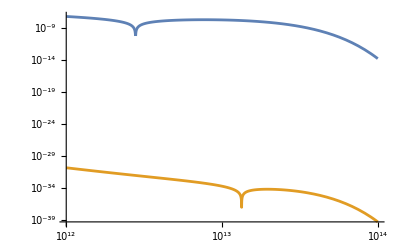

```mathematica
LogLogPlot[{Abs[outp2[r]],Abs[D[outp2[rr],{rr,2}]]/.{rr->r}},{r,10^12,10^14}]
```

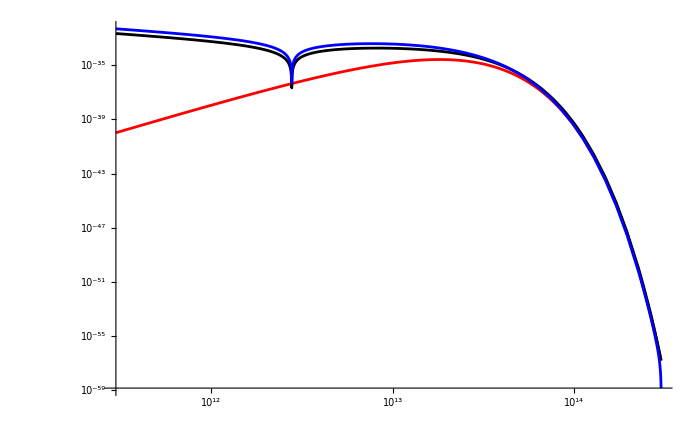

```mathematica
Clear[α]
newTry= ((1/(GNM 22.2))^2 Re[-2.40284 10^-19]outp[r]-1/r^2 D[r^2 D[outp[r],r],r]- (2α μ outp[r])/r);
newTry3= (Re[-2.40284 10^-19]outp[r]-( D[outp[r],{r,2}]+ 2 D[outp[r],r]/r )- .1(2α μ outp[r])/r);Block[{α=0.1661485565,μ=10^-12},LogLogPlot[{1/2 0.087217/(2μ)^(3/2)10^10 Rb[n1,l1,r] Rb[n2,l2,r]Rb[n3,l3,r]/.{a0-> 1/(μ α)},Abs[newTry ],Abs[newTry3] 10^-7 },{r,3 10^11,3  10^14},PlotStyle->{Red,Black,Blue},ImageSize->700,PlotRange->All]]
```

```mathematica
D[Log[y[x]],x]
```

y'[x]/y[x]

```mathematica
FullSimplify[val,α>0&&μ>0]
```

ⅇ^(-1/2 r α μ) α^(9/2) μ^3 (-0.000624422+α (0.000312211 r μ+α (-0.00202694+α (0.00101347 r μ+α (0.00042718+α (-0.00021359 r μ+α (0.000268386-0.000134193 r α μ)))))))

```mathematica
FullSimplify[1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n1,l1,r] Rb[n2,l2,r]Rb[n3,l3,r]/.{a0-> 1/(μ α)},α>0&&μ>0]
```

(ⅇ^(-4/3 r α μ) r^4 (α μ)^(5/2))/(1944 √15)

```mathematica
Series[Hypergeometric1F1[1-ⅈ/(a0 k),2,-2 ⅈ k r],{r,0,2}]
```

1-(ⅈ (-ⅈ+a0 k) r)/a0-(((-ⅈ+a0 k) (-ⅈ+2 a0 k)) r^2)/(3 a0^2)+O[r]^3

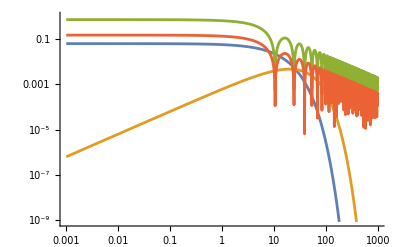

```mathematica
LogLogPlot[{Rb[1,0,r]/.{a0->10},Rb[2,1,r]/.{a0->10},Abs[RinfC[.2,0,r]/.{a0->10}],Abs[RinfC[-.2,0,r]/.{a0->10}]},{r,10^-3,1000}]
```

```mathematica
Integrate[Hypergeometric1F1[-I/(k a0)+l+1,2l+2,- 2I k r]/.{a0->1},{k,0,1}]
```

∫_0^1 Hypergeometric1F1[1-ⅈ/k+l,2+2 l,-2 ⅈ k r]ⅆk

```mathematica
Expand[Integrate[D[(k r)^4 Exp[-k ],r],{k,0,Infinity},Assumptions->r>0]]
```

96 r^3

```mathematica
D[(24 ⅈ r^4)/(ⅈ+r)^5,r]
```

-(120 ⅈ r^4)/(ⅈ+r)^6+(96 ⅈ r^3)/(ⅈ+r)^5

```mathematica
Integrate[D[Exp[I k r](k r)^4 Exp[-k ],r],{k,0,Infinity},Assumptions->r>0]
```

-(24 ⅈ r^3 (-4 ⅈ+r))/(ⅈ+r)^6

```mathematica
Expand[-(24 ⅈ r^3 (-4 ⅈ+r))/(ⅈ+r)^6]
```

-(96 r^3)/(ⅈ+r)^6-(24 ⅈ r^4)/(ⅈ+r)^6

```mathematica
FullSimplify[(-1/r^2 D[r^2 D[RinfC[kk,0,r],r],r]-(2 α μ)/r RinfC[kk,0,r])/RinfC[kk,0,r]/.{a0->1/(α μ)}]
```

kk^2

```mathematica
FullSimplify[(-1/r^2 D[r^2 D[Rb[2,0, r],r],r]-(2 α μ)/r Rb[2,0, r])/Rb[2,0, r]/.{a0->1/(α μ)}]
```

-1/4 α^2 μ^2

```mathematica
GNM=7484169213.942;
hbar=6.58 10^-16;
kms=2.998 10^5;
```

```mathematica
Ergs[n_,α_,μ_]:=μ(1-α^2/(2 n^2)-α^4/(8 n^4));
ErgI[α_,μ_]:= Ergs[2,α,μ] + Ergs[2,α,μ] - Ergs[3,α,μ]
```

```mathematica
Clear[rout]
```

```mathematica
rout[rr_,Mbh_,S0_,μ_]:=
(α=Mbh μ GNM;
Src[β_,r_]:=(1 S0 0.08)/(2(2μ)^(3/2))Rb[2,1,r]^2 Rb[3,2,r]/.{a0->1/(μ α)};
rmax=20 (1/(α μ));
rp=(1+√(1-0.9^2))GNM Mbh;

rint = Src[α,rmax];
drint = D[Src[α,r],r]/.{r->rmax};

val=Rv[r]/.NDSolve[{D[Rv[r],{r,2}]== -2 (α μ Rv[r])/r+(μ^2- ErgI[α,μ]^2)Rv[r] - 2 D[Rv[r],r]/r+Src[α,r],Rv[rmax]==10^-60,Rv'[rmax]==-10^-60},Rv[r],{r, rmax,rp},AccuracyGoal->30,PrecisionGoal->11]⟦1⟧⟦1⟧/.{r->rr})
```

```mathematica
test=Interpolation[Table[{rr,rout[rr,22,10^20,10^-12]},{rr,10^Range[Log10[rp 1.001],Log10[rmax 0.99],.1]}]];
```

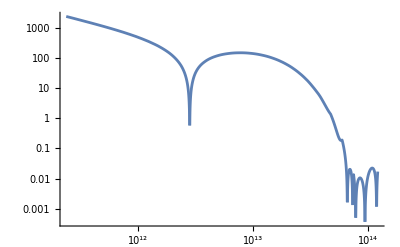

```mathematica
LogLogPlot[Abs[test[r]],{r,rp 1.001, rmax}]
```

```mathematica
8 π rout[rp 1.01,22.2,10^20,10^-12]^2 0.165254937^2/(( 10^-12)^2)1/((10^20)^2)(1+√(1-0.9^2))
```

5.51647×10^-10

```mathematica
Clear[μ]
```

```mathematica
rout2[rr_,Mbh_,S0_,μ_]:=
(α=Mbh μ GNM;
Src[β_,r_]:=(1 S0 0.08)/(2(2μ)^(3/2))Rb[2,1,r]^2 Rb[3,2,r]/.{a0->1/(μ α)};
rmax=50 (1/(α μ));
rp=(1+√(1-0.9^2))GNM Mbh;

rint = Src[α,rmax];
drint = D[Src[α,r],r]/.{r->rmax};

val=Rv[r]/.NDSolve[{D[Rv[r],{r,2}]== -2 (α μ Rv[r])/r+(μ^2- Ergs[1,α,μ]^2)Rv[r] - 2 D[Rv[r],r]/r,Rv[rmax]==10^-40,Rv'[rmax]==-10^-40},Rv[r],{r, rmax,100},AccuracyGoal->30,PrecisionGoal->11]⟦1⟧⟦1⟧/.{r->rr})
```

```mathematica
test=Interpolation[Table[{rr,rout2[rr,22,10^40,10^-12]},{rr,10^Range[Log10[100],Log10[rmax 0.99],.1]}]];
```

```mathematica
nm=NIntegrate[test[r]^2 r^2,{r,rp 1.01, rmax}]
```

7.15083×10^55

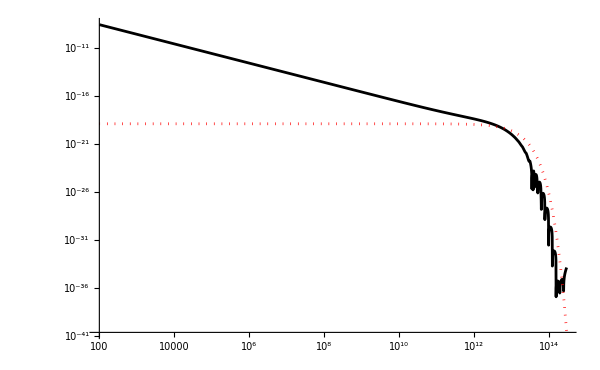

```mathematica
LogLogPlot[{Abs[test[r]/(√nm)],Abs[Rb[1,0,r]/.{a0->1/(μ α)}/.{μ->10^-12}]},{r,100, rmax},PlotRange->All,PlotStyle->{Black,{Red,Dotted}},ImageSize->600]
```

```mathematica
Block[{s0=10^20},(rout[rp 1.01,22,10^3,10^-12]/rout[rp 1.01,22,10^3,2 10^-12])^-2]
```

6.12065

```mathematica
FullSimplify[Rb[3,2,r]/.{a0->1/(α μ)},μ>0]
```

2/81 √(2/15) ⅇ^(-1/3 r α μ) r^2 α^2 √(α^3) μ^(7/2)

```mathematica
FullSimplify[Src[α,r]/((α μ)^2 μ),μ>0]
```

(1.68003×10^10 ⅇ^(-1.33333 r) r^4)/α^2

```mathematica
rmax
```

2.×10^13

```mathematica
8 π rout[rp 1.001,22.2,10^20,.5 10^-12]^2 0.165254937^2/(( 10^-12)^2)1/((10^20)^2)(1+√(1-0.9^2))
```

NDSolve::ndsz: At r == 4.81497×10^14, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {2.3881×10^11} lies outside the range of data in the interpolating function. Extrapolation will be used.

1.93484×10^-25

```mathematica
0.08307/(μ GNM)
```

11.0994

```mathematica
Block[{s0=10^20},(rout[rp,0.2,s0]/rout[rp,0.1,s0])^2]
```

8.11062

```mathematica
Table[{α,(rout[rp,2α,10^20]/rout[rp,α,10^20])^2},{α,Range[.01,.5,.01]}]
```

{{0.01,8.03991},{0.02,8.01386},{0.03,8.03725},{0.04,8.06041},{0.05,8.07126},{0.06,8.0811},{0.07,8.09005},{0.08,8.09814},{0.09,8.10536},{0.1,8.11197},{0.11,8.11802},{0.12,8.12326},{0.13,8.12787},{0.14,8.13183},{0.15,8.13517},{0.16,8.13789},{0.17,8.13998},{0.18,8.14159},{0.19,8.14244},{0.2,8.14266},{0.21,8.14224},{0.22,8.14105},{0.23,8.13934},{0.24,8.13689},{0.25,8.13387},{0.26,8.13006},{0.27,8.12552},{0.28,8.1204},{0.29,8.11435},{0.3,8.10761},{0.31,8.10019},{0.32,8.09185},{0.33,8.08259},{0.34,8.07266},{0.35,8.06175},{0.36,8.04985},{0.37,8.03715},{0.38,8.02348},{0.39,8.0087},{0.4,7.993},{0.41,7.97625},{0.42,7.95842},{0.43,7.9396},{0.44,7.91944},{0.45,7.89823},{0.46,7.87582},{0.47,7.85218},{0.48,7.82735},{0.49,7.8013},{0.5,7.77363}}

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]
```

1/2

```mathematica
n1=2;l1=1;m1=1;
n2=2;l2=1;m2=1;
n3=3;l3=2;m3=2;
```

```mathematica
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[2,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]]
```

α^2/7200000000000000000000000

```mathematica
hold=FullSimplify[fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,l,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)},α>0&&μ>0]
```

(2^(-3+l) ⅇ^(-((4/3+1/n) r)) r^4 (r/n)^l √(Gamma[-l+n]/(n^4 (l+n)!)) LaguerreL[-1-l+n,1+2 l,(2 r)/n])/(243 √15)

```mathematica
rp 0.08 10^-12
```

0.00954235

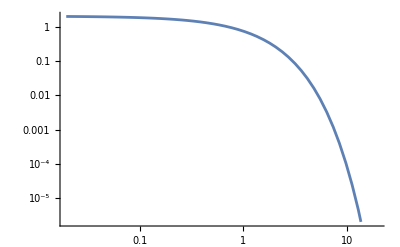

```mathematica
LogLogPlot[1/(√(α^3 μ^3))Rb[1,0,r/(μ α)]/.{a0->1/α / μ}/.{n->1,l->0},{r,0,20}]
```

```mathematica
NIntegrate[hold r^2/.{n->1,l->0},{r,.3 ,Infinity},PrecisionGoal->18,AccuracyGoal->18]
```

0.000253951

```mathematica
NIntegrate[hold r^2/.{n->1,l->0},{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18]
```

0.000253953

```mathematica
N[(Limit[Rb[1,0,r],r->0]/.{a0->1/α / μ})/(Rb[1,0,r/(α μ)]/.{a0->1/α / μ})/.{r->.01}]
```

1.01005

```mathematica
Clear[α]
```

```mathematica
val=0;
Do[
If[n>l+1,
CG = Block[{m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,l,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];

val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,l,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};]
,{n,1,20},{l,0,0}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,20}],α>0&&μ>0]
(*FullSimplify[Series[8π val^2(1+√(1+0.9^2)),{α,0,20}],α>0&&μ>0]*)
```

2.07972×10^-7 λ^2 μ α^7+O[α]^(41/2)

```mathematica
2 10^-7 α^7/.{α -> 0.16614}
```

6.98794×10^-13

```mathematica
Block[{k=α μ,l=0},NIntegrate[Rinf[k,l,r ]Rb[n1,l1,r] Rb[n2,l2,r]Rb[n3,l3,r] r^2/.{a0->1/(α μ)}/.{α->0.2,μ->10^-12},{r,rp 1.1,10^16}]]/Block[{k=α μ,l=0},NIntegrate[Rinf[k,l,r ]Rb[n1,l1,r] Rb[n2,l2,r]Rb[n3,l3,r] r^2/.{a0->1/(α μ)}/.{α->0.1,μ->10^-12},{r,rp 1.1,10^16}]]
```

5.65685+1.22548×10^-12 ⅈ

```mathematica
Block[{k=α μ,l=2},NIntegrate[Rinf[k,l,r ]Rb[n1,l1,r] Rb[n2,l2,r]Rb[n3,l3,r] r^2/.{a0->1/(α μ)}/.{α->0.2,μ->10^-12},{r,rp 1.1,10^16}]]/Block[{k=α μ,l=2},NIntegrate[Rinf[k,l,r ]Rb[n1,l1,r] Rb[n2,l2,r]Rb[n3,l3,r] r^2/.{a0->1/(α μ)}/.{α->0.1,μ->10^-12},{r,rp 1.1,10^16}]]
```

5.65685

```mathematica
Block[{k=5 α μ},hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[2,1,r/(α μ)] Rb[2,1,r/(α μ)]Rb[3,2,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR = NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->6,AccuracyGoal->6]]
```

2.98768×10^-6+8.85594×10^-9 ⅈ

```mathematica
intR
```

NIntegrate::inumr: The integrand (ⅇ^(1/2 (r (-3-2 ⅈ k Power[«2»] Power[«2»])+(π α μ)/k)) k r^5 Abs[Gamma[1-(ⅈ α μ)/k]] Hypergeometric1F1[1+(ⅈ α μ)/k,2,(2 ⅈ k r)/(α μ)])/(24 √6 α μ) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

((α μ)^(11/2) NIntegrate[hold2 r^2,{r,0,∞},PrecisionGoal→6,AccuracyGoal→6])/(α^3 μ^3)

```mathematica
Block[{k=α μ },Rinf[k,0,r ]/Rinf[k,2,r ]/.{a0->1/(α μ)}/.{α->0.1,μ->10^-12}/.{r->rp 1.1}]
```

13783.4+0. ⅈ

```mathematica
(*k > 0 part*)
```

```mathematica
Clear[α]
```

```mathematica
(*kvals = Range[0.01, 2, 0.05]μ α ;*)
kvals = Range[0.01, 2, .1]μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Block[{l=0,m=0},Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,l,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->6,AccuracyGoal->6];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }]];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
(*R0=Limit[Rinf[k,0,r],r->(1+√(1-0.9^2))]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};*)
(*R0=Normal[Series[Limit[Rinf[k,0,r/(α μ)],r->α^2(1-√(1-0.9^2))]/(α μ)/.{a0-> 1/(μ α),k-> k α μ},{α,0,0}]];*)
(*R1=FullSimplify[Normal[Series[Limit[Rinf[k,0,r/(α μ)],r->α^2(1-√(1-0.9^2))]/(α μ)/.{a0-> 1/(μ α),k-> k α μ},{α,0,1}]]-R0];*)
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

```mathematica
FullSimplify[Normal[Series[Limit[Rinf[k,0,r/(α μ)],r->α^2(1-√(1-0.9^2))]/(α μ)/.{a0-> 1/(μ α),k-> k α μ},{α,0,3}]]]
```

ⅇ^(π/(2 k)) k (2-1.12822 α^2) Abs[Gamma[(-ⅈ+k)/k]]

```mathematica
FullSimplify[Normal[Series[Rinf[k,0,r]/.{a0->1/(μ α)},{r,0,1}]]]
```

-2 ⅇ^((π α μ)/(2 k)) k (-1+r α μ) Abs[Gamma[1-(ⅈ α μ)/k]]

```mathematica
Limit[Rinf[k,0,r],r->0]
```

4 ⅇ^(π/(a0 k)) k^2 Abs[Gamma[1-ⅈ/(a0 k)]]^2

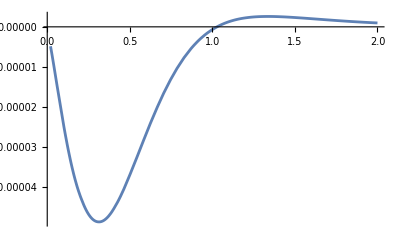

```mathematica
Plot[Re[cOfK[k]R0],{k,.02, 2},PlotRange->All]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

3.31154×10^-11 λ^2 μ α^7+O[α]^10

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

2.31436×10^-9 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

$Aborted

```mathematica
kvals⟦1⟧/(α μ)
```

0.01

```mathematica
Rinf[k,0,r]/.{a0-> 1/(μ α),k-> k α μ}/.{α->.1,μ->10^-12}
```

2.×10^-13 ⅇ^(π/(2 k)-(0.+1.×10^-13 ⅈ) k r) k Abs[Gamma[1-ⅈ/k]] Hypergeometric1F1[1+ⅈ/k,2,(0.+2.×10^-13 ⅈ) k r]

```mathematica
Plot[{Real[Rinf[k,0,r]/.{a0-> 1/(μ α),k-> k α μ}/.{α->.16,μ->10^-12}]},{r,0,2}]
```

-Graphics-

## 322 x 322 → 211 x Inf [test!]

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1/2;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=3;l1=2;m1=2;
n2=3;l2=2;m2=2;
n3=2;l3=1;m3=1;
```

```mathematica
Block[{l=l2+l1-l3+2,m=-(m1+m2-m3)},SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ]]
```

-(15 √(1155/2) (-1+9 Cos[θ]^2) Sin[θ]^9)/(2048 π^2)

```mathematica
m1+m2-m3
```

3

```mathematica
l1+l2-l3
```

3

```mathematica
N[ Block[{l=l2+l1-l3+2,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]]]
```

0.0165571

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity}],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

1.13451×10^-8 λ^2 μ^2 α^4+1.57571×10^-10 λ^2 μ^2 α^6+O[α]^14

```mathematica
kvals = Range[0.16, 0.18, 0.0001]μ α ;
clist = {};
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Conjugate[Rinf[k,l2+l1-l3,r/(α μ) ]]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->22,AccuracyGoal->22];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
```

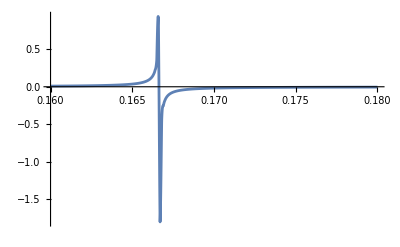

```mathematica
Plot[Re[cOfK[k]R0],{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)},PlotRange->All]
```

```mathematica
Limit[Rinf[k,l2+l1-l3,r],r->Infinity]
```

lim_(r→∞) 1/315 ⅇ^(π/(2 a0 k)-ⅈ k r) k^4 r^3 Abs[Gamma[4-ⅈ/(a0 k)]] Hypergeometric1F1[4+ⅈ/(a0 k),8,2 ⅈ k r]

```mathematica
khold
```

-(α^2 (240+1559 α^2) (34560+240 α^2+1559 α^4) μ^2)/298598400

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

1.38719×10^-9 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

1.52885×10^-7 λ^2 μ α^7+O[α]^10

## 322 x 322 → 211 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1/2;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=3;l1=2;m1=2;
n2=3;l2=2;m2=2;
n3=2;l3=1;m3=1;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity}],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

1.13451×10^-8 λ^2 μ^2 α^4+1.57571×10^-10 λ^2 μ^2 α^6+O[α]^14

```mathematica
CG = Block[{l=l2+l1-l3+4,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity}],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

0.

```mathematica
10^-8 (0.03)^8
```

6.561×10^-21

## 322 x 411 → 211 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=3;l1=2;m1=2;
n2=4;l2=1;m2=1;
n3=2;l3=1;m3=1;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},PrecisionGoal->8,AccuracyGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,1}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,4}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

3.73534×10^-9 λ^2 μ^2 α^4+O[α]^6

## 411 x 422 → 211 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=1;m1=1;
n2=4;l2=2;m2=2;
n3=2;l3=1;m3=1;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,1}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,4}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

2.23477×10^-9 λ^2 μ^2 α^4+O[α]^6

## 422 x 322 → 211 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=2;m1=2;
n2=3;l2=2;m2=2;
n3=2;l3=1;m3=1;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,1}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,4}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

1.61941×10^-8 λ^2 μ^2 α^4+O[α]^6

## 433 x 433 → 211 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1/2;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=3;m1=3;
n2=4;l2=3;m2=3;
n3=2;l3=1;m3=1;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,1}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,4}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

9.20827×10^-11 λ^2 μ^2 α^4+O[α]^6

```mathematica
Series[ωnew,{α,0,2}]
```

μ+(μ α^2)/16+O[α]^3

## 322 x 433 → 211 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=3;l1=2;m1=2;
n2=4;l2=3;m2=3;
n3=2;l3=1;m3=1;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,1}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,4}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

2.61936×10^-9 λ^2 μ^2 α^4+O[α]^6

## 211 x 211 → 322 x BH

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]
```

1/2

```mathematica
n1=2;l1=1;m1=1;
n2=2;l2=1;m2=1;
n3=3;l3=2;m3=2;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,20}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

3.6113×10^-7 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.05]μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->6,AccuracyGoal->6];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

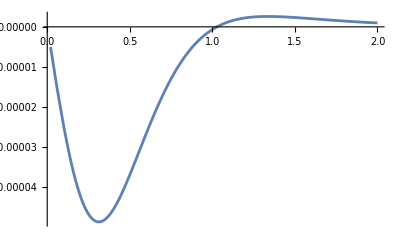

```mathematica
Plot[Re[cOfK[k]R0],{k,.02, 2}]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

2.32152×10^-9 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

4.21361×10^-7 λ^2 μ α^7+O[α]^10

## 211 x 311 → 322 x BH

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;
```

```mathematica
n1=2;l1=1;m1=1;
n2=3;l2=1;m2=1;
n3=3;l3=2;m3=2;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,20}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

3.11168×10^-10 λ^2 μ α^3-8.40007×10^-9 (λ^2 μ) α^5+5.66906×10^-8 λ^2 μ α^7+O[α]^(15/2)

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.05]μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->6,AccuracyGoal->6];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

```mathematica
Plot[Re[cOfK[k]R0],{k,.02, 2}]
```

-Graphics-

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

2.32152×10^-9 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

4.21361×10^-7 λ^2 μ α^7+O[α]^10

```mathematica
Solve[FullSimplify[4/2.7 10^-2 α^8-ξ 3.11 10^-10(0.99/(.9))(10^19/f)^4 α^7(.25 (0.01/α)^3(f/10^15)^2)(7 10^-6 (f/10^15)^2)]==0,α]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{α→0.},{α→0.},{α→0.},{α→0.},{α→-0.141783 ξ^(1/4)},{α→(0.-0.141783 ⅈ) ξ^(1/4)},{α→(0.+0.141783 ⅈ) ξ^(1/4)},{α→0.141783 ξ^(1/4)}}

## 211 x 211 → 422 x BH

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]
```

1/2

```mathematica
n1=2;l1=1;m1=1;
n2=2;l2=1;m2=1;
n3=4;l3=2;m3=2;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,20}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

1.25146×10^-7 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.05]μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->6,AccuracyGoal->6];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

```mathematica
Plot[Re[cOfK[k]R0],{k,.02, 2}]
```

-Graphics-

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

2.32152×10^-9 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

4.21361×10^-7 λ^2 μ α^7+O[α]^10

## 211 x 211 → 322 x BH [check radial Eq]

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]
```

1/2

```mathematica
n1=2;l1=1;m1=1;
n2=2;l2=1;m2=1;
n3=3;l3=2;m3=2;
```

```mathematica
rr=Range[1+√(1-0.9^2),2 10^4,1];
```

```mathematica
rout=ConstantArray[0,Length[rr]];
val=ConstantArray[0,Length[rr]];
srs=ConstantArray[0,Length[rr]];
 Block[{m=0,α=0.041},
CG = Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}];
Do[hold=fac 1/(2α)^(3/2)Rb[n,l,r ]Rb[n1,l1,r] Rb[n2,l2,r]Rb[n3,l3,r]/.{a0-> 1/α^2};
ωnew =  ωerg[n1,α,α,l1]+ωerg[n2,α,α,l2]-ωerg[n3,α,α,l3];

kDiff =(α^2 -ωnew^2)-(α^2-ωerg[n,α,α,0]^2);
cf=(CG/kDiff NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->15,AccuracyGoal->15,Method->"QuasiMonteCarlo"])/.{a0-> 1/α^2};
tempR =Rb[n,0,rr]/.{a0-> 1/α^2}; 
rout+=cf Rb[n,0,rr]/.{a0-> 1/α^2}; 
val+= ((α^2 -ωnew^2) cf tempR- 2 α^2/rr cf tempR)/.{a0-> 1/α^2};
val+=-cf D[Rb[n,0,r],{r,2}]/.{r->rr}/.{a0-> 1/α^2};
val+=-2cf D[Rb[n,0,r],r]/r/.{r->rr}/.{a0->1/α^2};
srs += fac 1/(2α)^(3/2)Rb[n1,l1,r] Rb[n2,l2,r]Rb[n3,l3,r]/.{a0-> 1/α^2}/.{r->rr};
,{n,1,2},{l,0,2}]];//Quiet
test=Interpolation[Thread[{rr,val}]];
testsrs=Interpolation[Thread[{rr,srs}]];
```

$Aborted

```mathematica
Block[{l=0,m=0,α=0.041},4  λ^2 μ(rout⟦1⟧)^2]
```

5.5861×10^-17 λ^2 μ

```mathematica
3.6113014745233424*^-7 λ^2 μ α^7/.{α -> 0.041}
```

7.03316×10^-17 λ^2 μ

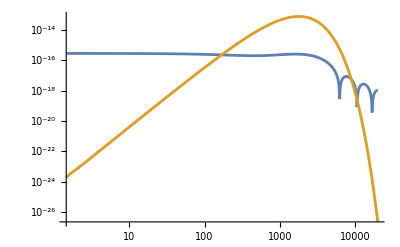

```mathematica
LogLogPlot[{Abs[test[x]],Abs[testsrs[x]]},{x,1.45,2  10^4}]
```

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.05]μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->6,AccuracyGoal->6];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

```mathematica
Plot[Re[cOfK[k]R0],{k,.02, 2}]
```

-Graphics-

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

2.32152×10^-9 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

4.21361×10^-7 λ^2 μ α^7+O[α]^10

## 211 x 211 → 322 x BH [add other WF?]

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]
```

1/2

```mathematica
n1=2;l1=1;m1=1;
n2=2;l2=1;m2=1;
n3=3;l3=2;m3=2;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,20}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

3.6113×10^-7 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.05]μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->6,AccuracyGoal->6];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

```mathematica
Plot[Re[cOfK[k]R0],{k,.02, 2}]
```

-Graphics-

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

2.32152×10^-9 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

4.21361×10^-7 λ^2 μ α^7+O[α]^10

## 211 x 211 → 422 x BH

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]
```

1/2

```mathematica
n1=2;l1=1;m1=1;
n2=2;l2=1;m2=1;
n3=4;l3=2;m3=2;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,20}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

1.25146×10^-7 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.05]μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->6,AccuracyGoal->6];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

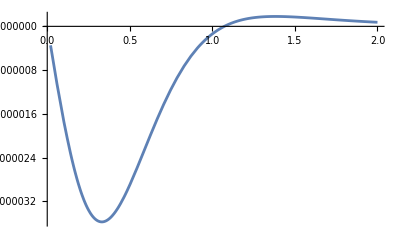

```mathematica
Plot[Re[cOfK[k]R0],{k,.02, 2}]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

1.38719×10^-9 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

1.52885×10^-7 λ^2 μ α^7+O[α]^10

## TEST

```mathematica
(*322 x 322 -> 533 x 21-1*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]
```

1/2

```mathematica
Clear[m]
```

```mathematica
n1=3;l1=2;m1=2;
n2=3;l2=2;m2=2;
n3=5;l3=4;m3=4;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[Conjugate[SphericalHarmonicY[l,m,θ,ϕ]]Conjugate[SphericalHarmonicY[l3,m3,θ,ϕ]]SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,20}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

1.90982×10^-9 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.05]μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->6,AccuracyGoal->6];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

```mathematica
Plot[Re[cOfK[k]R0],{k,.02, 2}]
```

-Graphics-

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

1.38719×10^-9 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

1.52885×10^-7 λ^2 μ α^7+O[α]^10

## TESTv2

```mathematica
(*322 x 322 -> 533 x 21-1*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]
```

1/2

```mathematica
Clear[m]
```

```mathematica
n1=3;l1=2;m1=2;
n2=3;l2=2;m2=2;
n3=6;l3=5;m3=5;
```

```mathematica
FullSimplify[ Block[{l=1,m=-1},Conjugate[SphericalHarmonicY[l,m,θ,ϕ]]Conjugate[SphericalHarmonicY[l3,m3,θ,ϕ]]SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ]],ϕ∈Reals]
```

-(45 √(231/2) Sin[θ]^5 Sin[Conjugate[θ]]^6)/(2048 π^2)

```mathematica
val=0;
CG = Block[{l=1,m=-1},Integrate[Conjugate[SphericalHarmonicY[l,m,θ,ϕ]]Conjugate[SphericalHarmonicY[l3,m3,θ,ϕ]]SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,20}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

7.02964×10^-11 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.05]μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->6,AccuracyGoal->6];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

```mathematica
Plot[Re[cOfK[k]R0],{k,.02, 2}]
```

-Graphics-

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

1.38719×10^-9 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

1.52885×10^-7 λ^2 μ α^7+O[α]^10

## 211 x 411 → 322 x BH [inf dominated?]

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

1

```mathematica
n1=2;l1=1;m1=1;
n2=4;l2=1;m2=1;
n3=3;l3=2;m3=2;
```

```mathematica
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[2,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]]
```

-7/144 α^2 μ^2

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
(*Print[val/.{α->1,μ->1}];*)
,{n,1,90}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,15}],α>0&&μ>0]
```

3.79027×10^-9 λ^2 μ α^7+O[α]^16

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = 10^Range[-4, Log10[100], 0.02] μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->10,AccuracyGoal->10];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

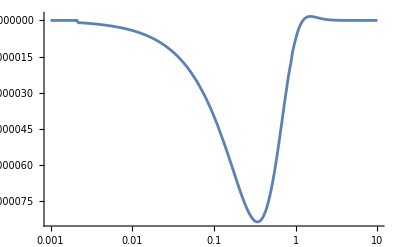

```mathematica
LogLinearPlot[Re[cOfK[k]R0],{k,.001, 10}]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

9.09593×10^-9 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,12}],α>0&&μ>0]
```

2.45653×10^-8 λ^2 μ α^7+O[α]^15

```mathematica
9.20314580318522*^-9 /3.50267884453691*^-9
```

2.62746

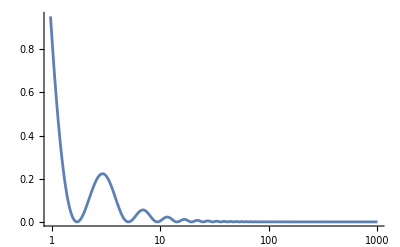

```mathematica
LogLinearPlot[Re[Rinf[0.5,0,r]Conjugate[Rinf[0.5,0,r]]/.{a0-> 1}],{r, 0,1000},PlotRange->All]
```

```mathematica
Rb[n1,l1,r/(α μ)]^2/.{a0-> 1/(μ α)}
```

1/24 ⅇ^-r r^2 α^3 μ^3

```mathematica
val=0;
CG = Block[{l=2,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Block[{l=2,m=0},Do[hold=FullSimplify[fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,l,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)},α>0&&μ>0];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,l,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->14,AccuracyGoal->14])/.{a0-> 1/(μ α)};
(*Print[val/.{α->1,μ->1}];*)
,{n,3,5}]];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,15}],α>0&&μ>0]
```

0.

```mathematica
hold
```

ComplexInfinity

```mathematica
FullSimplify[fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[1,2,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)},α>0&&μ>0]
```

ComplexInfinity

## 411 x 411 → 322 x BH [v2]

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1/2(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

1/2

```mathematica
n1=4;l1=1;m1=1;
n2=4;l2=1;m2=1;
n3=3;l3=2;m3=2;
```

```mathematica
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[2,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]]
```

-17/72 α^2 μ^2

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
(*Print[val/.{α->1,μ->1}];*)
,{n,1,90}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,15}],α>0&&μ>0]
```

5.62915×10^-12 λ^2 μ α^7+O[α]^16

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = 10^Range[-3, 1.5, 0.025] μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->10,AccuracyGoal->10];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

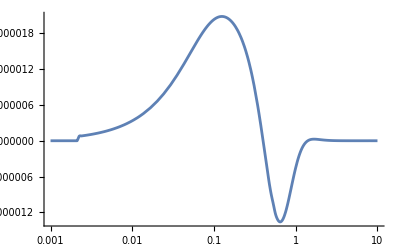

```mathematica
LogLinearPlot[Re[cOfK[k]R0],{k,.001, 10}]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

2.79285×10^-12 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,12}],α>0&&μ>0]
```

1.63011×10^-11 λ^2 μ α^7+O[α]^15

```mathematica
9.20314580318522*^-9 /3.50267884453691*^-9
```

2.62746

```mathematica
LogLinearPlot[Re[Rinf[0.5,0,r]Conjugate[Rinf[0.5,0,r]]/.{a0-> 1}],{r, 0,1000},PlotRange->All]
```

-Graphics-

```mathematica
Rb[n1,l1,r/(α μ)]^2/.{a0-> 1/(μ α)}
```

1/24 ⅇ^-r r^2 α^3 μ^3

```mathematica
val=0;
CG = Block[{l=2,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Block[{l=2,m=0},Do[hold=FullSimplify[fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,l,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)},α>0&&μ>0];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,l,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->14,AccuracyGoal->14])/.{a0-> 1/(μ α)};
(*Print[val/.{α->1,μ->1}];*)
,{n,3,5}]];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,15}],α>0&&μ>0]
```

0.

```mathematica
hold
```

ComplexInfinity

```mathematica
FullSimplify[fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[1,2,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)},α>0&&μ>0]
```

ComplexInfinity

## 411 x 411 → 322 x BH

```mathematica
Block[{n=3},kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
FullSimplify[Limit[Rb[n,0,r],r->0]/kuse a0^(3/2)α^2 μ^2,a0>0]
]
```

(2 α^2 μ^2)/(3 √3 kuse)

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1/2;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=1;m1=1;
n2=4;l2=1;m2=1;
n3=3;l3=2;m3=2;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
(*Print[NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18]];*)
,{n,1,50}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

6.07729×10^-12 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = 10^Range[-3, 1.5, 0.1] μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

(*intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->20,AccuracyGoal->20,Method->"Trapezoidal"]*);
intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->20,AccuracyGoal->20];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

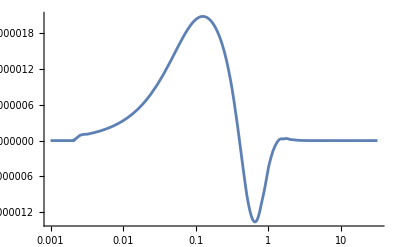

```mathematica
LogLinearPlot[Re[cOfK[k]R0],{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

2.41095×10^-12 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

1.61411×10^-11 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,20}],α>0&&μ>0]
```

6.07729×10^-12 λ^2 μ α^7+O[α]^23

```mathematica
FullSimplify[val,α>0&&μ>0]
```

-1.23261×10^-6 α^(5/2) μ

```mathematica
FullSimplify[val2,α>0&&μ>0]
```

(-7.78639×10^-7-7.64672×10^-21 ⅈ) α^(5/2) μ

## 211 x 322 → 433 x BH

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=2;l1=1;m1=1;
n2=3;l2=2;m2=2;
n3=4;l3=3;m3=3;
(*n3=5;l3=4;m3=4;*)
```

```mathematica
val=0;
CG = Block[{l=2,m=0},Integrate[Conjugate[SphericalHarmonicY[l,m,θ,ϕ]]Conjugate[SphericalHarmonicY[l3,m3,θ,ϕ]]SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,2,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,20}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

ComplexInfinity

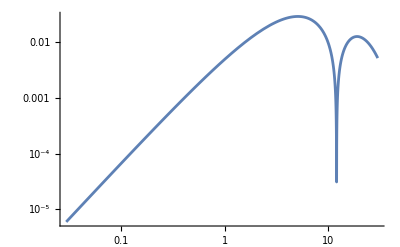

```mathematica
LogLogPlot[Abs[Rb[4,2,r]]/.{a0->1},{r,0,30}]
```

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.05]μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->6,AccuracyGoal->6];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

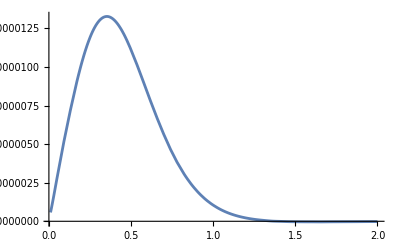

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2}]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

2.21466×10^-10 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,5}],α>0&&μ>0]
```

9.067×10^-8 λ^2 μ α^7+O[α]^8

## 322 x 322 → 544 x BH

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1/2;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=3;l1=2;m1=2;
n2=3;l2=2;m2=2;
n3=5;l3=4;m3=4;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,20}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

1.90982×10^-9 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.02]μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

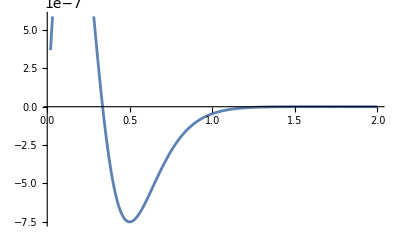

```mathematica
Plot[Re[cOfK[k]R0],{k,.02, 2}]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

2.86687×10^-14 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

1.92465×10^-9 λ^2 μ α^7+O[α]^10

## 322 x 322 → 644 x BH

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1/2;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=3;l1=2;m1=2;
n2=3;l2=2;m2=2;
n3=9;l3=4;m3=4;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,40}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

1.33987×10^-9 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.02]μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

```mathematica
Plot[Re[cOfK[k]R0],{k,.02, 2}]
```

-Graphics-

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

2.86687×10^-14 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

1.92465×10^-9 λ^2 μ α^7+O[α]^10

## 322 x 422 → 544 x BH

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=3;l1=2;m1=2;
n2=4;l2=2;m2=2;
n3=5;l3=4;m3=4;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,20}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

6.88452×10^-11 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.02]μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

```mathematica
Plot[Re[cOfK[k]R0],{k,.02, 2}]
```

-Graphics-

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

2.86687×10^-14 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

1.92465×10^-9 λ^2 μ α^7+O[α]^10

## 211 x 422 → 433 x BH [res]

```mathematica
ωerg[n_,α_,μ_,l_]:=μ (1-α^2/(2 n^2)-α^4/(8 n^4));
```

```mathematica
ωerg2[n_,α_,μ_,l_,a_,m_]:=μ (1-α^2/(2 n^2)-α^4/(8 n^4)+((2l-3n + 1)α^4)/(n^4(l+1/2))+(2a m α^5)/(n^3 l(l+1/2)(l+1)))
```

```mathematica
Series[ωerg2[n,α,μ,l,a,m]/ωerg[n,α,μ,l],{α,0,7}]/.{n->4,l->3,m->3,a->1}
```

1+α^5/448+α^7/14336+O[α]^8

```mathematica
tt[α_,n_]:=1-α^2/(2 n^2)-α^4/(8 n^4)
```

```mathematica
tt[α,n1]+tt[α,n2]-tt[α,n3]
```

1-α^2/(2 n1^2)-α^2/(2 n2^2)+α^2/(2 n3^2)-α^4/(8 n1^4)-α^4/(8 n2^4)+α^4/(8 n3^4)

```mathematica
tt[α,2]
```

1-α^2/8-α^4/128

```mathematica
FullSimplify[ωnew]
```

-1/128 (-128+16 α^2+α^4) μ

```mathematica
ωerg[2,α,μ,0]
```

(1-α^2/8-(81 α^4)/128) μ

```mathematica
ωnew= ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[2,α,μ,0]^2)]
```

0

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=2;l1=1;m1=1;
n2=4;l2=2;m2=2;
n3=4;l3=3;m3=3;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
(*Print[n];Print[kDiff];*)
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->19,AccuracyGoal->19])/.{a0-> 1/(μ α)};
,{n,1,2}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,3}],α>0&&μ>0]
```

7.82881×10^-11 λ^2 μ α^3+O[α]^(7/2)

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.02]μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->10,AccuracyGoal->10, Method->"QuasiMonteCarlo"];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

$Aborted

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

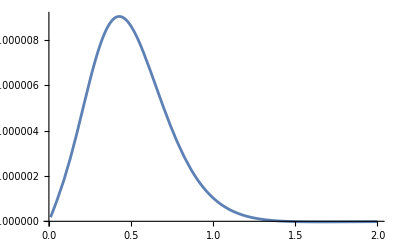

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2}]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

1.0361×10^-10 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,3}],α>0&&μ>0]
```

7.82881×10^-11 λ^2 μ α^3+O[α]^4

## 411 x 411 → 422 x BH [res]

```mathematica
ωerg[n_,α_,μ_,l_,a_,m_]:=μ (1-α^2/(2 n^2)-α^4/(8 n^4)+((2l-3n + 1)α^4)/(n^4(l+1/2))+(2a m α^5)/(n^3 l(l+1/2)(l+1)))
```

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1/2;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=1;m1=1;
n2=4;l2=1;m2=1;
n3=4;l3=2;m3=2;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,20}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

Power::infy: Infinite expression 1/0 encountered.

```mathematica
k2First
```

(3 α^2 μ^2)/50

```mathematica
k2
```

(3 α^2 μ^2)/50

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.02]μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

$Aborted

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

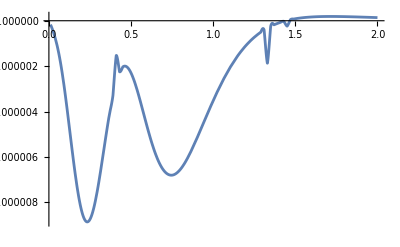

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2}]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

1.16422×10^-10 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

2.19286×10^-11 λ^2 μ α^3-1.23712×10^-10 (λ^2 μ) α^5+1.74495×10^-10 λ^2 μ α^7+O[α]^8

## 211 x 211 → 622 x BH

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=2;l1=1;m1=1;
n2=2;l2=1;m2=1;
n3=6;l3=2;m3=2;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,20}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

1.36751×10^-7 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.02]μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

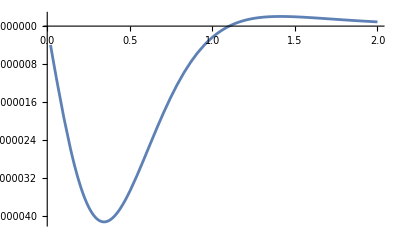

```mathematica
Plot[Re[cOfK[k]R0],{k,.02, 2}]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

1.97908×10^-9 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

1.71632×10^-7 λ^2 μ α^7+O[α]^10

```mathematica
1.7 10^-7 α^11/.{α->0.0609376787889787}
```

7.31466×10^-21

```mathematica
((1.5*^-24)/(2.5 10^-25))
```

6.

## 211 x 411 → 522 x BH

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=2;l1=1;m1=1;
n2=4;l2=1;m2=1;
n3=5;l3=2;m3=2;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,20}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

7.43058×10^-8 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.02]μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

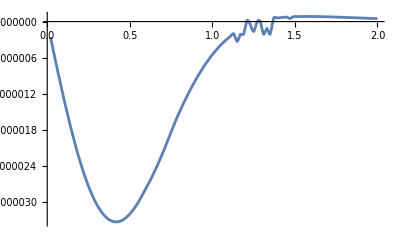

```mathematica
Plot[Re[cOfK[k]R0],{k,.02, 2}]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

1.80694×10^-9 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

9.92874×10^-8 λ^2 μ α^7+O[α]^10

```mathematica
9.928738344372948*^-8 α^11/.{α->0.03}
```

1.75885×10^-24

```mathematica
((1.758846211490634*^-24)/(8.646251329514222 10^-25))^-1
```

0.491587

## 411 x 532 → 543 x BH

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=1;m1=1;
n2=5;l2=3;m2=2;
n3=5;l3=4;m3=3;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,20}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {35.656}. NIntegrate obtained -9.51798×10^-7 and 1.17081×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {32.2047}. NIntegrate obtained -8.66448×10^-7 and 1.32153×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {33.8398}. NIntegrate obtained -7.93175×10^-7 and 1.36491×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

4.92498×10^-12 λ^2 μ α^3+2.6631×10^-11 λ^2 μ α^5+3.60005×10^-11 λ^2 μ α^7+O[α]^(15/2)

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.02]μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

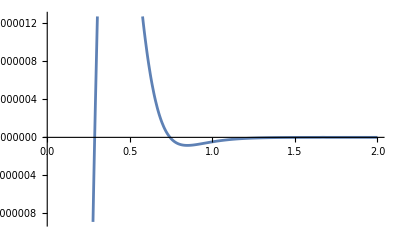

```mathematica
Plot[Re[cOfK[k]R0],{k,.02, 2}]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

6.12538×10^-12 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

4.92498×10^-12 λ^2 μ α^3+3.76159×10^-11 λ^2 μ α^5+7.18255×10^-11 λ^2 μ α^7+O[α]^8

```mathematica
4.9249819785617285*^-12 α^7/.{α->0.03}
```

1.07709×10^-22

## 321 x 755 → 876 x BH

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=3;l1=2;m1=1;
n2=7;l2=5;m2=5;
n3=8;l3=7;m3=6;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,20}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

1.10804×10^-13 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.02]μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

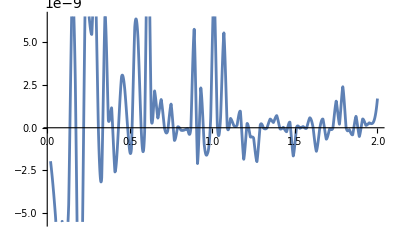

```mathematica
Plot[Re[cOfK[k]R0],{k,.02, 2}]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

3.78522×10^-18 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

1.11873×10^-13 λ^2 μ α^7+O[α]^10

```mathematica
1.1 10^-13 α^11/.{α->0.0506}
```

6.12419×10^-28

## 762 x 866 → 521 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=7;l1=6;m1=2;
n2=8;l2=6;m2=6;
n3=5;l3=2;m3=1;
```

```mathematica
Series[ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3],{α,0,2}]
```

μ+(311 μ α^2)/156800+O[α]^3

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->16,PrecisionGoal->16],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

1.0432×10^-71 λ^2 μ^2 α^4+2.0691×10^-74 λ^2 μ^2 α^6+O[α]^14

## 422 x 422 → 544 x BH

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1/2;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=2;m1=2;
n2=4;l2=2;m2=2;
n3=5;l3=4;m3=4;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,20}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

2.53193×10^-9 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.02]μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

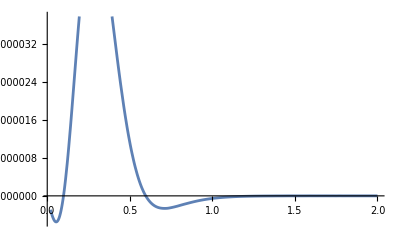

```mathematica
Plot[Re[cOfK[k]R0],{k,.02, 2}]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

7.38975×10^-12 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

2.26575×10^-9 λ^2 μ α^7+O[α]^10

```mathematica
2.265751467378204*^-9 α^11/.{α->0.03}
```

4.01371×10^-26

## 321 x 522 → 543 x BH

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=3;l1=2;m1=1;
n2=5;l2=2;m2=2;
n3=5;l3=4;m3=3;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,20}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

1.72294×10^-12 λ^2 μ α^3+1.60012×10^-11 λ^2 μ α^5+3.71513×10^-11 λ^2 μ α^7+O[α]^(15/2)

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.02]μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

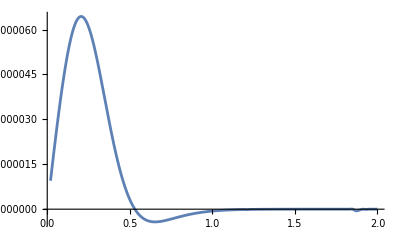

```mathematica
Plot[Re[cOfK[k]R0],{k,.02, 2}]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

1.23401×10^-11 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

1.72294×10^-12 λ^2 μ α^3+2.52231×10^-11 λ^2 μ α^5+9.23143×10^-11 λ^2 μ α^7+O[α]^8

```mathematica
1.7229364636764806*^-12 α^7/.{α->0.03}
```

3.76806×10^-23

## 542 x 543 → 321 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=5;l1=4;m1=2;
n2=5;l2=4;m2=3;
n3=3;l3=2;m3=1;
```

```mathematica
Series[ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3],{α,0,2}]
```

μ+(7 μ α^2)/450+O[α]^3

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->10,PrecisionGoal->10],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

5.59123×10^-29 λ^2 μ^2 α^4+8.69747×10^-31 λ^2 μ^2 α^6+O[α]^14

```mathematica
5.591229599985127*^-29/.{α->0.07}
```

5.59123×10^-29

## 433 x 542 → 321 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=3;m1=3;
n2=5;l2=4;m2=2;
n3=3;l3=2;m3=1;
```

```mathematica
Series[ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3],{α,0,2}]
```

μ+(31 μ α^2)/7200+O[α]^3

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->10,PrecisionGoal->10],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

4.03542×10^-17 λ^2 μ^2 α^4+1.73747×10^-19 λ^2 μ^2 α^6+O[α]^14

```mathematica
5.591229599985127*^-29/.{α->0.07}
```

5.59123×10^-29

```mathematica
0.1 (0.7/0.03)^1
```

2.33333

## 321 x 433 → 211 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=3;l1=2;m1=1;
n2=4;l2=3;m2=3;
n3=2;l3=1;m3=1;
```

```mathematica
Series[ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3],{α,0,2}]
```

μ+(11 μ α^2)/288+O[α]^3

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->10,PrecisionGoal->10],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

8.38195×10^-10 λ^2 μ^2 α^4+3.20144×10^-11 λ^2 μ^2 α^6+O[α]^14

```mathematica
8.381949072988977*^-10 α^8/.{α->0.03}
```

5.4994×10^-22

```mathematica
holdT
```

1/5266071827251200 121 √(11/14) ⅇ^((6 π)/(√11)+1/12 ⅈ (13 ⅈ+√11) r) r^10 Abs[Gamma[5-(12 ⅈ)/(√11)]] Conjugate[Hypergeometric1F1[5+(12 ⅈ)/(√11),10,1/6 ⅈ √11 r]]

```mathematica
ff
```

(-0.000489339-2.52394×10^-12 ⅈ) α^(3/2)

```mathematica
kuse
```

1/12 √11 α μ

```mathematica
facfront
```

1/12 √11 α μ^2+(11 √11 α^3 μ^2)/3456

## 431 x 544 → 321 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=3;m1=1;
n2=5;l2=4;m2=4;
n3=3;l3=2;m3=1;
```

```mathematica
Series[ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3],{α,0,2}]
```

μ+(31 μ α^2)/7200+O[α]^3

```mathematica
CG = Block[{l=l2+l1-l3+2,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT =  Block[{l=l2+l1-l3+2,m=-(m1+m2-m3)},1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,7,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0]];
ff= FullSimplify[(CG (4π))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,10^3},AccuracyGoal->11,PrecisionGoal->11],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

1.72375×10^-12 λ^2 μ^2 α^4+7.4217×10^-15 λ^2 μ^2 α^6+O[α]^14

```mathematica
1.7237506074933756*^-12  α^8/.{α->0.1955}
```

3.67831×10^-18

## NEW [Dec 2024]

## 311 x 311 → 211 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=3;l1=1;m1=1;
n2=3;l2=1;m2=1;
n3=2;l3=1;m3=1;
```

```mathematica
Series[ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3],{α,0,2}]
```

μ+(μ α^2)/72+O[α]^3

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

5.1409×10^-8 λ^2 μ^2 α^4+7.14014×10^-10 λ^2 μ^2 α^6+O[α]^14

## 311 x 322 → 211 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=3;l1=1;m1=1;
n2=3;l2=2;m2=2;
n3=2;l3=1;m3=1;
```

```mathematica
Series[ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3],{α,0,2}]
```

μ+(μ α^2)/72+O[α]^3

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

1.21555×10^-8 λ^2 μ^2 α^4+1.68826×10^-10 λ^2 μ^2 α^6+O[α]^14

## 311 x 411 → 211 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=3;l1=1;m1=1;
n2=4;l2=1;m2=1;
n3=2;l3=1;m3=1;
```

```mathematica
Series[ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3],{α,0,2}]
```

μ+(11 μ α^2)/288+O[α]^3

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

1.87115×10^-8 λ^2 μ^2 α^4+7.14677×10^-10 λ^2 μ^2 α^6+O[α]^14

## 311 x 422 → 211 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=3;l1=1;m1=1;
n2=4;l2=2;m2=2;
n3=2;l3=1;m3=1;
```

```mathematica
Series[ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3],{α,0,2}]
```

μ+(11 μ α^2)/288+O[α]^3

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

6.95805×10^-9 λ^2 μ^2 α^4+2.65759×10^-10 λ^2 μ^2 α^6+O[α]^14

## 311 x 433 → 211 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=3;l1=1;m1=1;
n2=4;l2=3;m2=3;
n3=2;l3=1;m3=1;
```

```mathematica
Series[ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3],{α,0,2}]
```

μ+(11 μ α^2)/288+O[α]^3

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

2.21075×10^-10 λ^2 μ^2 α^4+8.44385×10^-12 λ^2 μ^2 α^6+O[α]^14

## 322 x 422 → 211 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=3;l1=2;m1=2;
n2=4;l2=2;m2=2;
n3=2;l3=1;m3=1;
```

```mathematica
Series[ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3],{α,0,2}]
```

μ+(11 μ α^2)/288+O[α]^3

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

1.61941×10^-8 λ^2 μ^2 α^4+6.18523×10^-10 λ^2 μ^2 α^6+O[α]^14

## 311 x 522 → 211 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=3;l1=1;m1=1;
n2=5;l2=2;m2=2;
n3=2;l3=1;m3=1;
```

```mathematica
Series[ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3],{α,0,2}]
```

μ+(89 μ α^2)/1800+O[α]^3

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

3.87946×10^-9 λ^2 μ^2 α^4+1.91818×10^-10 λ^2 μ^2 α^6+O[α]^14

## 311 x 533 → 211 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=3;l1=1;m1=1;
n2=5;l2=3;m2=3;
n3=2;l3=1;m3=1;
```

```mathematica
Series[ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3],{α,0,2}]
```

μ+(89 μ α^2)/1800+O[α]^3

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

7.56695×10^-11 λ^2 μ^2 α^4+3.74144×10^-12 λ^2 μ^2 α^6+O[α]^14

## 311 x 544 → 211 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=3;l1=1;m1=1;
n2=5;l2=4;m2=4;
n3=2;l3=1;m3=1;
```

```mathematica
Series[ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3],{α,0,2}]
```

μ+(89 μ α^2)/1800+O[α]^3

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

5.26246×10^-11 λ^2 μ^2 α^4+2.60199×10^-12 λ^2 μ^2 α^6+O[α]^14

## 532 x 543 → 321 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=5;l1=3;m1=2;
n2=5;l2=4;m2=3;
n3=3;l3=2;m3=1;
```

```mathematica
Series[ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3],{α,0,2}]
```

μ+(7 μ α^2)/450+O[α]^3

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->12,PrecisionGoal->12],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,6}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

1.04365×10^-28 λ^2 μ^2 α^4+1.62345×10^-30 λ^2 μ^2 α^6+1.57651×10^-30 λ^2 μ^2 α^8+O[α]^14

```mathematica
10^-28 (0.03)^8
```

6.561×10^-41

## 322 x 511 → 211 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=3;l1=2;m1=2;
n2=5;l2=1;m2=1;
n3=2;l3=1;m3=1;
```

```mathematica
Series[ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3],{α,0,2}]
```

μ+(89 μ α^2)/1800+O[α]^3

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

1.68046×10^-9 λ^2 μ^2 α^4+8.30895×10^-11 λ^2 μ^2 α^6+O[α]^14

## 411 x 511 → 211 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=1;m1=1;
n2=5;l2=1;m2=1;
n3=2;l3=1;m3=1;
```

```mathematica
Series[ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3],{α,0,2}]
```

μ+(59 μ α^2)/800+O[α]^3

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

4.31553×10^-14 λ^2 μ^2 α^4+3.1827×10^-15 λ^2 μ^2 α^6+O[α]^14

## 411 x 522 → 211 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=1;m1=1;
n2=5;l2=2;m2=2;
n3=2;l3=1;m3=1;
```

```mathematica
Series[ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3],{α,0,2}]
```

μ+(59 μ α^2)/800+O[α]^3

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

8.05981×10^-10 λ^2 μ^2 α^4+5.94411×10^-11 λ^2 μ^2 α^6+O[α]^14

## 411 x 533 → 211 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=1;m1=1;
n2=5;l2=3;m2=3;
n3=2;l3=1;m3=1;
```

```mathematica
Series[ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3],{α,0,2}]
```

μ+(59 μ α^2)/800+O[α]^3

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->6,PrecisionGoal->6],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

5.76425×10^-16 λ^2 μ^2 α^4+4.25113×10^-17 λ^2 μ^2 α^6+O[α]^14

## 411 x 544 → 211 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=1;m1=1;
n2=5;l2=4;m2=4;
n3=2;l3=1;m3=1;
```

```mathematica
Series[ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3],{α,0,2}]
```

μ+(59 μ α^2)/800+O[α]^3

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

4.27523×10^-14 λ^2 μ^2 α^4+3.15298×10^-15 λ^2 μ^2 α^6+O[α]^14

## 422 x 511 → 211 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=2;m1=2;
n2=5;l2=1;m2=1;
n3=2;l3=1;m3=1;
```

```mathematica
Series[ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3],{α,0,2}]
```

μ+(59 μ α^2)/800+O[α]^3

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

1.96782×10^-10 λ^2 μ^2 α^4+1.45127×10^-11 λ^2 μ^2 α^6+O[α]^14

## 422 x 522 → 211 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=2;m1=2;
n2=5;l2=2;m2=2;
n3=2;l3=1;m3=1;
```

```mathematica
Series[ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3],{α,0,2}]
```

μ+(59 μ α^2)/800+O[α]^3

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

3.74027×10^-9 λ^2 μ^2 α^4+2.75845×10^-10 λ^2 μ^2 α^6+O[α]^14

## 422 x 533 → 211 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=2;m1=2;
n2=5;l2=3;m2=3;
n3=2;l3=1;m3=1;
```

```mathematica
Series[ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3],{α,0,2}]
```

μ+(59 μ α^2)/800+O[α]^3

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

6.19093×10^-14 λ^2 μ^2 α^4+4.56581×10^-15 λ^2 μ^2 α^6+O[α]^14

## 422 x 544 → 211 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=2;m1=2;
n2=5;l2=4;m2=4;
n3=2;l3=1;m3=1;
```

```mathematica
Series[ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3],{α,0,2}]
```

μ+(59 μ α^2)/800+O[α]^3

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

2.70799×10^-12 λ^2 μ^2 α^4+1.99714×10^-13 λ^2 μ^2 α^6+O[α]^14

## 433 x 511 → 211 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=3;m1=3;
n2=5;l2=1;m2=1;
n3=2;l3=1;m3=1;
```

```mathematica
Series[ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3],{α,0,2}]
```

μ+(59 μ α^2)/800+O[α]^3

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

2.64847×10^-16 λ^2 μ^2 α^4+1.95325×10^-17 λ^2 μ^2 α^6+O[α]^14

## 433 x 522 → 211 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=3;m1=3;
n2=5;l2=2;m2=2;
n3=2;l3=1;m3=1;
```

```mathematica
Series[ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3],{α,0,2}]
```

μ+(59 μ α^2)/800+O[α]^3

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

2.70955×10^-10 λ^2 μ^2 α^4+1.99829×10^-11 λ^2 μ^2 α^6+O[α]^14

## 433 x 533 → 211 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=3;m1=3;
n2=5;l2=3;m2=3;
n3=2;l3=1;m3=1;
```

```mathematica
Series[ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3],{α,0,2}]
```

μ+(59 μ α^2)/800+O[α]^3

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

1.85881×10^-10 λ^2 μ^2 α^4+1.37087×10^-11 λ^2 μ^2 α^6+O[α]^14

## 433 x 544 → 211 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=3;m1=3;
n2=5;l2=4;m2=4;
n3=2;l3=1;m3=1;
```

```mathematica
Series[ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3],{α,0,2}]
```

μ+(59 μ α^2)/800+O[α]^3

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

2.43838×10^-11 λ^2 μ^2 α^4+1.7983×10^-12 λ^2 μ^2 α^6+O[α]^14

## 411 x 511 → 311 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=1;m1=1;
n2=5;l2=1;m2=1;
n3=3;l3=1;m3=1;
```

```mathematica
Series[ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3],{α,0,2}]
```

μ+(31 μ α^2)/7200+O[α]^3

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

2.79633×10^-15 λ^2 μ^2 α^4+1.20397×10^-17 λ^2 μ^2 α^6+O[α]^14

## 411 x 511 → 322 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=1;m1=1;
n2=5;l2=1;m2=1;
n3=3;l3=2;m3=2;
```

```mathematica
Series[ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3],{α,0,2}]
```

μ+(31 μ α^2)/7200+O[α]^3

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

1.45704×10^-16 λ^2 μ^2 α^4+6.27339×10^-19 λ^2 μ^2 α^6+O[α]^14

## 411 x 522 → 311 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=1;m1=1;
n2=5;l2=2;m2=2;
n3=3;l3=1;m3=1;
```

```mathematica
Series[ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3],{α,0,2}]
```

μ+(31 μ α^2)/7200+O[α]^3

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

1.12787×10^-14 λ^2 μ^2 α^4+4.8561×10^-17 λ^2 μ^2 α^6+O[α]^14

## 411 x 533 → 311 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=1;m1=1;
n2=5;l2=3;m2=3;
n3=3;l3=1;m3=1;
```

```mathematica
Series[ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3],{α,0,2}]
```

μ+(31 μ α^2)/7200+O[α]^3

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

2.04932×10^-14 λ^2 μ^2 α^4+8.82348×10^-17 λ^2 μ^2 α^6+O[α]^14

## 411 x 533 → 322 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=1;m1=1;
n2=5;l2=3;m2=3;
n3=3;l3=2;m3=2;
```

```mathematica
Series[ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3],{α,0,2}]
```

μ+(31 μ α^2)/7200+O[α]^3

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

4.2952×10^-15 λ^2 μ^2 α^4+1.84932×10^-17 λ^2 μ^2 α^6+O[α]^14

## 411 x 544 → 311 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=1;m1=1;
n2=5;l2=4;m2=4;
n3=3;l3=1;m3=1;
```

```mathematica
Series[ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3],{α,0,2}]
```

μ+(31 μ α^2)/7200+O[α]^3

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

1.86405×10^-15 λ^2 μ^2 α^4+8.02577×10^-18 λ^2 μ^2 α^6+O[α]^14

## 411 x 533 → 322 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=1;m1=1;
n2=5;l2=3;m2=3;
n3=3;l3=2;m3=2;
```

```mathematica
Series[ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3],{α,0,2}]
```

μ+(31 μ α^2)/7200+O[α]^3

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

4.2952×10^-15 λ^2 μ^2 α^4+1.84932×10^-17 λ^2 μ^2 α^6+O[α]^14

## 511 x 511 → 311 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1/2;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=5;l1=1;m1=1;
n2=5;l2=1;m2=1;
n3=3;l3=1;m3=1;
```

```mathematica
Series[ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3],{α,0,2}]
```

μ+(7 μ α^2)/450+O[α]^3

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

4.24531×10^-27 λ^2 μ^2 α^4+6.60381×10^-29 λ^2 μ^2 α^6+O[α]^14

## 411 x 511 → 311 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=3;m1=3;
n2=5;l2=4;m2=4;
n3=2;l3=1;m3=1;
```

```mathematica
Series[ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3],{α,0,2}]
```

μ+(59 μ α^2)/800+O[α]^3

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

2.43838×10^-11 λ^2 μ^2 α^4+1.7983×10^-12 λ^2 μ^2 α^6+O[α]^14

## 211 x 211 → 522 x BH

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1/2;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=2;l1=1;m1=1;
n2=2;l2=1;m2=1;
n3=5;l3=2;m3=2;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,40}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

6.06146×10^-8 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = 10^Range[-2, 1.4, 0.025] μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

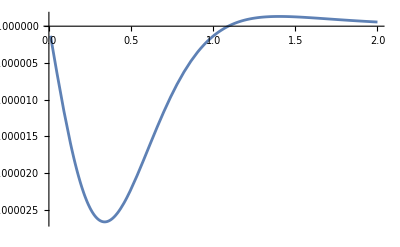

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2},PlotRange->All]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

7.72281×10^-10 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

7.50706×10^-8 λ^2 μ α^7+O[α]^10

## 211 x 311 → 322 x BH

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=2;l1=1;m1=1;
n2=3;l2=1;m2=1;
n3=3;l3=2;m3=2;
```

```mathematica
FullSimplify[Series[ωerg[2,α,μ,1]+ωerg[3,α,μ,1]-ωerg[4,α,μ,2],{α,0,2}]]
```

μ-(43 μ α^2)/288+O[α]^3

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,40}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

3.11168×10^-10 λ^2 μ α^3-8.43494×10^-9 (λ^2 μ) α^5+5.71622×10^-8 λ^2 μ α^7+O[α]^(15/2)

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = 10^Range[-2, 1.4, 0.025] μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

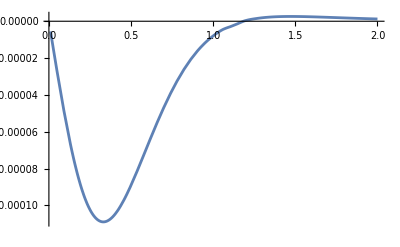

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2},PlotRange->All]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

1.43738×10^-8 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

3.11168×10^-10 λ^2 μ α^3-1.26647×10^-8 (λ^2 μ) α^5+1.28865×10^-7 λ^2 μ α^7+O[α]^8

## 211 x 311 → 422 x BH

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=2;l1=1;m1=1;
n2=3;l2=1;m2=1;
n3=4;l3=2;m3=2;
```

```mathematica
FullSimplify[Series[ωerg[2,α,μ,1]+ωerg[3,α,μ,1]-ωerg[4,α,μ,2],{α,0,2}]]
```

μ-(43 μ α^2)/288+O[α]^3

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,40}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

1.99173×10^-7 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = 10^Range[-2, 1.4, 0.025] μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

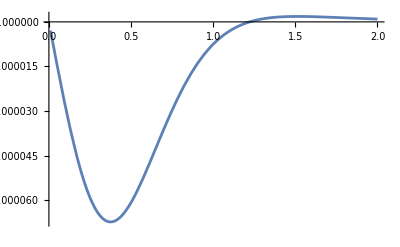

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2},PlotRange->All]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

6.19335×10^-9 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

2.7561×10^-7 λ^2 μ α^7+O[α]^10

## 211 x 311 → 522 x BH

```mathematica
ωerg[n_,α_,μ_,l_]:=μ (1-α^2/(2 n^2)-α^4/(8 n^4));
```

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=2;l1=1;m1=1;
n2=3;l2=1;m2=1;
n3=5;l3=2;m3=2;
```

```mathematica
FullSimplify[Series[ωerg[2,α,μ,1]+ωerg[3,α,μ,1]-ωerg[5,α,μ,2],{α,0,2}]]
```

μ-(289 μ α^2)/1800+O[α]^3

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,40}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

7.11957×10^-8 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = 10^Range[-2, 1.4, 0.025] μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

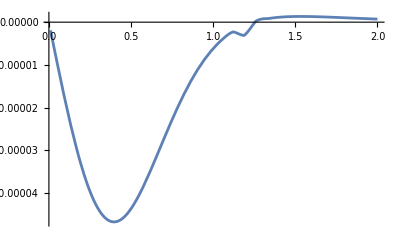

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2},PlotRange->All]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

3.17727×10^-9 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

1.04452×10^-7 λ^2 μ α^7+O[α]^10

## 211 x 411 → 522 x BH

```mathematica
ωerg[n_,α_,μ_,l_]:=μ (1-α^2/(2 n^2)-α^4/(8 n^4));
```

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=2;l1=1;m1=1;
n2=4;l2=1;m2=1;
n3=5;l3=2;m3=2;
```

```mathematica
FullSimplify[Series[ωerg[5,α,μ,1]+ωerg[4,α,μ,2]-ωerg[3,α,μ,1],{α,0,2}]]
```

μ+(31 μ α^2)/7200+O[α]^3

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,40}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

7.44329×10^-8 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = 10^Range[-2, 1.4, 0.025] μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

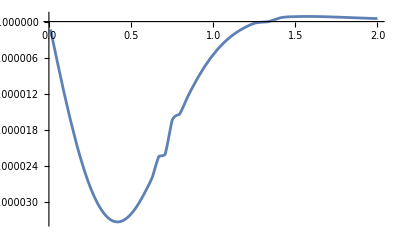

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2},PlotRange->All]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

1.72184×10^-9 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

9.8796×10^-8 λ^2 μ α^7+O[α]^10

## 211 x 322 → 533 x BH

```mathematica
ωerg[n_,α_,μ_,l_]:=μ (1-α^2/(2 n^2)-α^4/(8 n^4));
```

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=2;l1=1;m1=1;
n2=3;l2=2;m2=2;
n3=5;l3=3;m3=3;
```

```mathematica
FullSimplify[Series[ωerg[2,α,μ,1]+ωerg[4,α,μ,1]-ωerg[5,α,μ,2],{α,0,2}]]
```

μ-(109 μ α^2)/800+O[α]^3

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,40}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

3.53279×10^-8 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = 10^Range[-2, 1.4, 0.025] μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

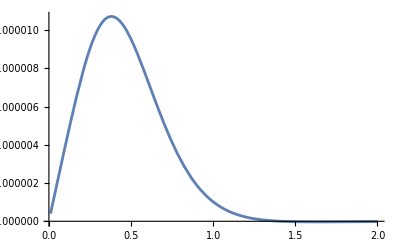

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2},PlotRange->All]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

1.50072×10^-10 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

3.08729×10^-8 λ^2 μ α^7+O[α]^10

## 211 x 422 → 533 x BH

```mathematica
ωerg[n_,α_,μ_,l_]:=μ (1-α^2/(2 n^2)-α^4/(8 n^4));
```

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=2;l1=1;m1=1;
n2=4;l2=2;m2=2;
n3=5;l3=3;m3=3;
```

```mathematica
FullSimplify[Series[ωerg[2,α,μ,1]+ωerg[4,α,μ,1]-ωerg[5,α,μ,2],{α,0,2}]]
```

μ-(109 μ α^2)/800+O[α]^3

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,40}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

1.20292×10^-7 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = 10^Range[-2, 1.4, 0.025] μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

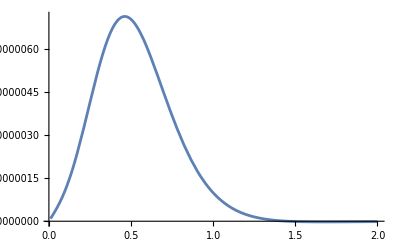

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2},PlotRange->All]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

6.46208×10^-11 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

1.1478×10^-7 λ^2 μ α^7+O[α]^10

## 211 x 433 → 544 x BH

```mathematica
ωerg[n_,α_,μ_,l_]:=μ (1-α^2/(2 n^2)-α^4/(8 n^4));
```

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=2;l1=1;m1=1;
n2=4;l2=3;m2=3;
n3=5;l3=4;m3=4;
```

```mathematica
FullSimplify[Series[ωerg[2,α,μ,1]+ωerg[4,α,μ,1]-ωerg[5,α,μ,2],{α,0,2}]]
```

μ-(109 μ α^2)/800+O[α]^3

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,40}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

1.14881×10^-9 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = 10^Range[-2, 1.4, 0.025] μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

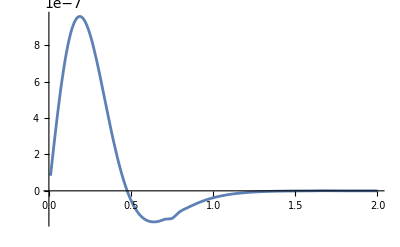

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2},PlotRange->All]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

1.83438×10^-13 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

1.1204×10^-9 λ^2 μ α^7+O[α]^10

## 211 x 511 → 322 x BH

```mathematica
ωerg[n_,α_,μ_,l_]:=μ (1-α^2/(2 n^2)-α^4/(8 n^4));
```

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=2;l1=1;m1=1;
n2=5;l2=1;m2=1;
n3=3;l3=2;m3=2;
```

```mathematica
FullSimplify[Series[ωerg[2,α,μ,1]+ωerg[5,α,μ,1]-ωerg[3,α,μ,2],{α,0,2}]]
```

μ-(161 μ α^2)/1800+O[α]^3

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,40}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

9.37642×10^-9 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = 10^Range[-2, 1.4, 0.025] μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

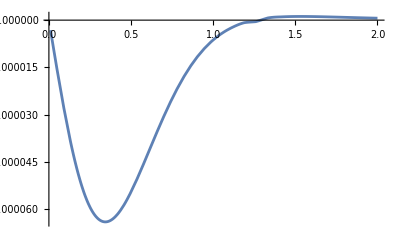

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2},PlotRange->All]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

5.4973×10^-9 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

2.92327×10^-8 λ^2 μ α^7+O[α]^10

## 211 x 511 → 422 x BH

```mathematica
ωerg[n_,α_,μ_,l_]:=μ (1-α^2/(2 n^2)-α^4/(8 n^4));
```

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=2;l1=1;m1=1;
n2=5;l2=1;m2=1;
n3=4;l3=2;m3=2;
```

```mathematica
FullSimplify[Series[ωerg[2,α,μ,1]+ωerg[5,α,μ,1]-ωerg[3,α,μ,2],{α,0,2}]]
```

μ-(161 μ α^2)/1800+O[α]^3

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,40}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

3.55021×10^-9 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = 10^Range[-2, 1.4, 0.025] μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

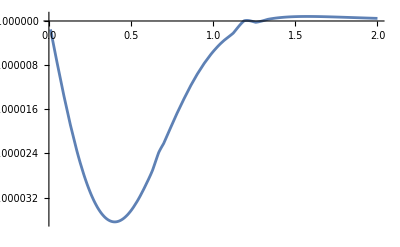

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2},PlotRange->All]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

2.0289×10^-9 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

2.11454×10^-10 λ^2 μ α^7+O[α]^10

## 211 x 522 → 433 x BH

```mathematica
ωerg[n_,α_,μ_,l_]:=μ (1-α^2/(2 n^2)-α^4/(8 n^4));
```

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=2;l1=1;m1=1;
n2=5;l2=2;m2=2;
n3=4;l3=3;m3=3;
```

```mathematica
FullSimplify[Series[ωerg[2,α,μ,1]+ωerg[5,α,μ,1]-ωerg[3,α,μ,2],{α,0,2}]]
```

μ-(161 μ α^2)/1800+O[α]^3

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,40}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

6.11834×10^-8 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = 10^Range[-2, 1.4, 0.025] μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

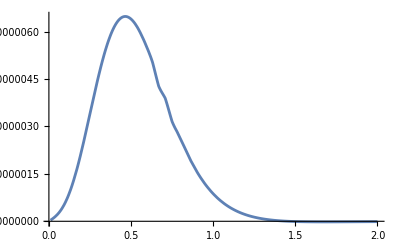

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2},PlotRange->All]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

4.9436×10^-11 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

6.47111×10^-8 λ^2 μ α^7+O[α]^10

## 211 x 511 → 522 x BH

```mathematica
ωerg[n_,α_,μ_,l_]:=μ (1-α^2/(2 n^2)-α^4/(8 n^4)+α^4/n^3(-6/(2l+1)+2/n));
```

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=2;l1=1;m1=1;
n2=5;l2=1;m2=1;
n3=5;l3=2;m3=2;
```

```mathematica
FullSimplify[Series[ωerg[2,α,μ,1]+ωerg[5,α,μ,1]-ωerg[3,α,μ,2],{α,0,2}]]
```

μ-(161 μ α^2)/1800+O[α]^3

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,40}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

6.57249×10^-12 λ^2 μ α^3-2.36811×10^-10 (λ^2 μ) α^5+2.1331×10^-9 λ^2 μ α^7+O[α]^(15/2)

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = 10^Range[-2, 1.4, 0.025] μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

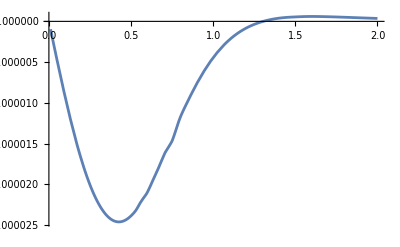

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2},PlotRange->All]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

9.9227×10^-10 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

6.57249×10^-12 λ^2 μ α^3-3.98282×10^-10 (λ^2 μ) α^5+6.03432×10^-9 λ^2 μ α^7+O[α]^8

## 211 x 522 → 533 x BH

```mathematica
ωerg[n_,α_,μ_,l_]:=μ (1-α^2/(2 n^2)-α^4/(8 n^4)+α^4/n^3(-6/(2l+1)+2/n));
```

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=2;l1=1;m1=1;
n2=5;l2=2;m2=2;
n3=5;l3=3;m3=3;
```

```mathematica
FullSimplify[Series[ωerg[2,α,μ,1]+ωerg[5,α,μ,1]-ωerg[3,α,μ,2],{α,0,2}]]
```

μ-(161 μ α^2)/1800+O[α]^3

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,40}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

2.61896×10^-11 λ^2 μ α^3-9.23107×10^-11 (λ^2 μ) α^5+8.13421×10^-11 λ^2 μ α^7+O[α]^(15/2)

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = 10^Range[-2, 1.4, 0.025] μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

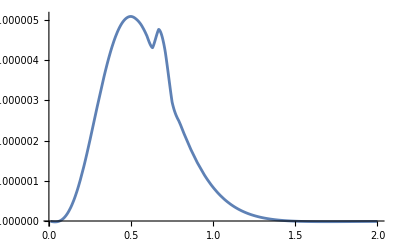

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2},PlotRange->All]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

3.12716×10^-11 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

2.61896×10^-11 λ^2 μ α^3-3.50965×10^-11 (λ^2 μ) α^5+1.1782×10^-11 λ^2 μ α^7+O[α]^8

## 211 x 533 → 544 x BH

```mathematica
ωerg[n_,α_,μ_,l_]:=μ (1-α^2/(2 n^2)-α^4/(8 n^4)+α^4/n^3(-6/(2l+1)+2/n));
```

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=2;l1=1;m1=1;
n2=5;l2=3;m2=3;
n3=5;l3=4;m3=4;
```

```mathematica
FullSimplify[Series[ωerg[2,α,μ,1]+ωerg[5,α,μ,1]-ωerg[3,α,μ,2],{α,0,2}]]
```

μ-(161 μ α^2)/1800+O[α]^3

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,40}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

4.58324×10^-13 λ^2 μ α^3+3.87304×10^-12 λ^2 μ α^5+8.18224×10^-12 λ^2 μ α^7+O[α]^(15/2)

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = 10^Range[-2, 1.4, 0.025] μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

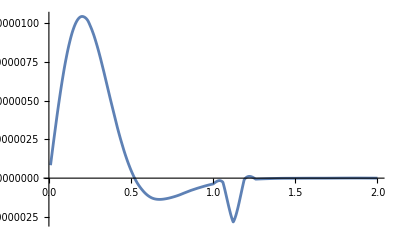

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2},PlotRange->All]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

2.421×10^-13 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

4.58324×10^-13 λ^2 μ α^3+4.53773×10^-12 λ^2 μ α^5+1.12328×10^-11 λ^2 μ α^7+O[α]^8

## 311 x 311 → 322 x BH

```mathematica
ωerg[n_,α_,μ_,l_]:=μ (1-α^2/(2 n^2)-α^4/(8 n^4)+α^4/n^3(-6/(2l+1)+2/n));
```

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1/2;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=3;l1=1;m1=1;
n2=3;l2=1;m2=1;
n3=3;l3=2;m3=2;
```

```mathematica
FullSimplify[Series[ωerg[2,α,μ,1]+ωerg[5,α,μ,1]-ωerg[3,α,μ,2],{α,0,2}]]
```

μ-(161 μ α^2)/1800+O[α]^3

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,40}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

1.61802×10^-10 λ^2 μ α^3-1.96766×10^-9 (λ^2 μ) α^5+5.98216×10^-9 λ^2 μ α^7+O[α]^(15/2)

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = 10^Range[-2, 1.4, 0.025] μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

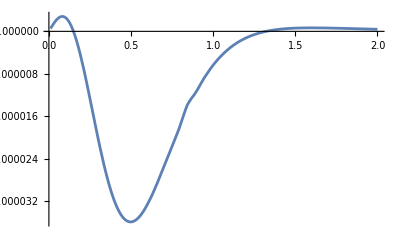

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2},PlotRange->All]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

1.33433×10^-9 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

1.61802×10^-10 λ^2 μ α^3-1.03844×10^-9 (λ^2 μ) α^5+1.66635×10^-9 λ^2 μ α^7+O[α]^8

## 311 x 311 → 422 x BH

```mathematica
ωerg[n_,α_,μ_,l_]:=μ (1-α^2/(2 n^2)-α^4/(8 n^4)+α^4/n^3(-6/(2l+1)+2/n));
```

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1/2;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=3;l1=1;m1=1;
n2=3;l2=1;m2=1;
n3=4;l3=2;m3=2;
```

```mathematica
FullSimplify[Series[ωerg[2,α,μ,1]+ωerg[5,α,μ,1]-ωerg[3,α,μ,2],{α,0,2}]]
```

μ-(161 μ α^2)/1800+O[α]^3

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,40}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

1.74975×10^-10 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = 10^Range[-2, 1.4, 0.025] μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->19,AccuracyGoal->10];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

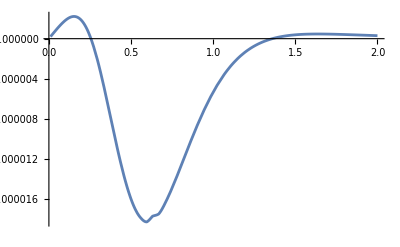

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2},PlotRange->All]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

2.98953×10^-10 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

1.65034×10^-11 λ^2 μ α^7+O[α]^10

## 311 x 322 → 433 x BH

```mathematica
ωerg[n_,α_,μ_,l_]:=μ (1-α^2/(2 n^2)-α^4/(8 n^4)+α^4/n^3(-6/(2l+1)+2/n));
```

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=3;l1=1;m1=1;
n2=3;l2=2;m2=2;
n3=4;l3=3;m3=3;
```

```mathematica
FullSimplify[Series[ωerg[2,α,μ,1]+ωerg[5,α,μ,1]-ωerg[3,α,μ,2],{α,0,2}]]
```

μ-(161 μ α^2)/1800+O[α]^3

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,40}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

6.88979×10^-8 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = 10^Range[-2, 1.4, 0.025] μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

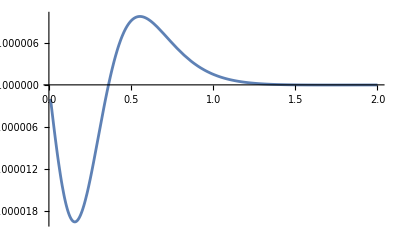

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2},PlotRange->All]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

1.09496×10^-12 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

6.9447×10^-8 λ^2 μ α^7+O[α]^10

## 311 x 311 → 522 x BH

```mathematica
ωerg[n_,α_,μ_,l_]:=μ (1-α^2/(2 n^2)-α^4/(8 n^4)+α^4/n^3(-6/(2l+1)+2/n));
```

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1/2;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=3;l1=1;m1=1;
n2=3;l2=1;m2=1;
n3=5;l3=2;m3=2;
```

```mathematica
FullSimplify[Series[ωerg[2,α,μ,1]+ωerg[5,α,μ,1]-ωerg[3,α,μ,2],{α,0,2}]]
```

μ-(161 μ α^2)/1800+O[α]^3

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,40}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

1.10599×10^-10 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = 10^Range[-2, 1.4, 0.025] μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

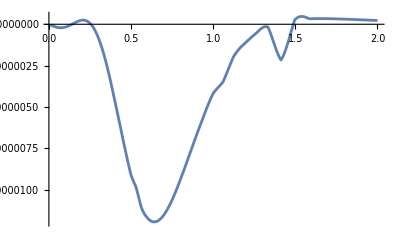

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2},PlotRange->All]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

1.46869×10^-10 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

2.56762×10^-12 λ^2 μ α^7+O[α]^10

## 311 x 322 → 533 x BH

```mathematica
ωerg[n_,α_,μ_,l_]:=μ (1-α^2/(2 n^2)-α^4/(8 n^4)+α^4/n^3(-6/(2l+1)+2/n));
```

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=3;l1=1;m1=1;
n2=3;l2=2;m2=2;
n3=5;l3=3;m3=3;
```

```mathematica
FullSimplify[Series[ωerg[2,α,μ,1]+ωerg[5,α,μ,1]-ωerg[3,α,μ,2],{α,0,2}]]
```

μ-(161 μ α^2)/1800+O[α]^3

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,40}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

2.771×10^-8 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = 10^Range[-2, 1.4, 0.025] μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

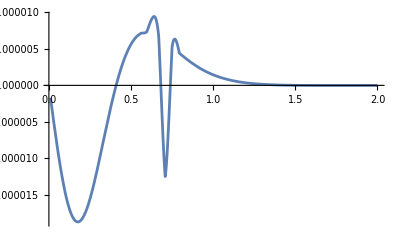

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2},PlotRange->All]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

2.48985×10^-11 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

2.93625×10^-8 λ^2 μ α^7+O[α]^10

## 311 x 411 → 322 x BH

```mathematica
ωerg[n_,α_,μ_,l_]:=μ (1-α^2/(2 n^2)-α^4/(8 n^4)+α^4/n^3(-6/(2l+1)+2/n));
```

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=3;l1=1;m1=1;
n2=4;l2=1;m2=1;
n3=3;l3=2;m3=2;
```

```mathematica
FullSimplify[Series[ωerg[2,α,μ,1]+ωerg[5,α,μ,1]-ωerg[3,α,μ,2],{α,0,2}]]
```

μ-(161 μ α^2)/1800+O[α]^3

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,40}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

1.85756×10^-10 λ^2 μ α^3-1.29784×10^-9 (λ^2 μ) α^5+2.26692×10^-9 λ^2 μ α^7+O[α]^(15/2)

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = 10^Range[-2, 1.4, 0.025] μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

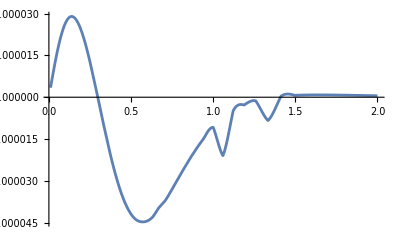

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2},PlotRange->All]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

1.22033×10^-9 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

1.85756×10^-10 λ^2 μ α^3-3.5572×10^-10 (λ^2 μ) α^5+1.96074×10^-10 λ^2 μ α^7+O[α]^8

## 311 x 411 → 422 x BH

```mathematica
ωerg[n_,α_,μ_,l_]:=μ (1-α^2/(2 n^2)-α^4/(8 n^4)+α^4/n^3(-6/(2l+1)+2/n));
```

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=3;l1=1;m1=1;
n2=4;l2=1;m2=1;
n3=4;l3=2;m3=2;
```

```mathematica
FullSimplify[Series[ωerg[2,α,μ,1]+ωerg[5,α,μ,1]-ωerg[3,α,μ,2],{α,0,2}]]
```

μ-(161 μ α^2)/1800+O[α]^3

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,40}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

3.75603×10^-13 λ^2 μ α^3-9.42271×10^-12 (λ^2 μ) α^5+5.90967×10^-11 λ^2 μ α^7+O[α]^(15/2)

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = 10^Range[-2, 1.4, 0.025] μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

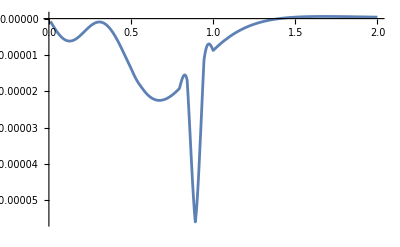

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2},PlotRange->All]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

1.27397×10^-9 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

3.75603×10^-13 λ^2 μ α^3+2.47078×10^-11 λ^2 μ α^5+9.04953×10^-10 λ^2 μ α^7+O[α]^8

## 311 x 411 → 522 x BH

```mathematica
ωerg[n_,α_,μ_,l_]:=μ (1-α^2/(2 n^2)-α^4/(8 n^4)+α^4/n^3(-6/(2l+1)+2/n));
```

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=3;l1=1;m1=1;
n2=4;l2=1;m2=1;
n3=5;l3=2;m3=2;
```

```mathematica
FullSimplify[Series[ωerg[2,α,μ,1]+ωerg[5,α,μ,1]-ωerg[3,α,μ,2],{α,0,2}]]
```

μ-(161 μ α^2)/1800+O[α]^3

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,40}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

1.00638×10^-10 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = 10^Range[-2, 1.4, 0.025] μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

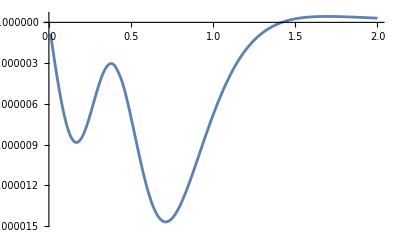

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2},PlotRange->All]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

3.37371×10^-10 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

8.06533×10^-10 λ^2 μ α^7+O[α]^10

## 311 x 422 → 433 x BH

```mathematica
ωerg[n_,α_,μ_,l_]:=μ (1-α^2/(2 n^2)-α^4/(8 n^4)+α^4/n^3(-6/(2l+1)+2/n));
```

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=3;l1=1;m1=1;
n2=4;l2=2;m2=2;
n3=4;l3=3;m3=3;
```

```mathematica
FullSimplify[Series[ωerg[2,α,μ,1]+ωerg[5,α,μ,1]-ωerg[3,α,μ,2],{α,0,2}]]
```

μ-(161 μ α^2)/1800+O[α]^3

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,40}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

7.70615×10^-12 λ^2 μ α^3+2.63514×10^-10 λ^2 μ α^5+2.25273×10^-9 λ^2 μ α^7+O[α]^(15/2)

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = 10^Range[-2, 1.4, 0.025] μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

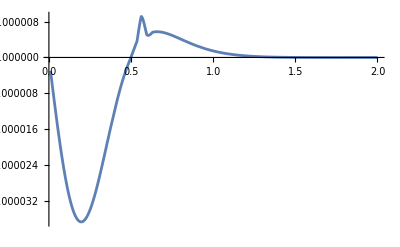

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2},PlotRange->All]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

2.82839×10^-10 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

7.70615×10^-12 λ^2 μ α^3+3.56886×10^-10 λ^2 μ α^5+4.13202×10^-9 λ^2 μ α^7+O[α]^8

## 311 x 422 → 533 x BH

```mathematica
ωerg[n_,α_,μ_,l_]:=μ (1-α^2/(2 n^2)-α^4/(8 n^4)+α^4/n^3(-6/(2l+1)+2/n));
```

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=3;l1=1;m1=1;
n2=4;l2=2;m2=2;
n3=5;l3=3;m3=3;
```

```mathematica
FullSimplify[Series[ωerg[2,α,μ,1]+ωerg[5,α,μ,1]-ωerg[3,α,μ,2],{α,0,2}]]
```

μ-(161 μ α^2)/1800+O[α]^3

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,40}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

1.07722×10^-9 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = 10^Range[-2, 1.4, 0.025] μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

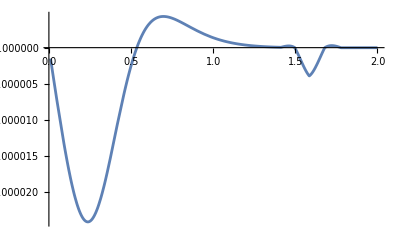

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2},PlotRange->All]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

1.62585×10^-10 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

2.07679×10^-9 λ^2 μ α^7+O[α]^10

## 311 x 433 → 544 x BH

```mathematica
ωerg[n_,α_,μ_,l_]:=μ (1-α^2/(2 n^2)-α^4/(8 n^4)+α^4/n^3(-6/(2l+1)+2/n));
```

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=3;l1=1;m1=1;
n2=4;l2=3;m2=3;
n3=5;l3=4;m3=4;
```

```mathematica
FullSimplify[Series[ωerg[2,α,μ,1]+ωerg[5,α,μ,1]-ωerg[3,α,μ,2],{α,0,2}]]
```

μ-(161 μ α^2)/1800+O[α]^3

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,40}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

1.62805×10^-8 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = 10^Range[-2, 1.4, 0.025] μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

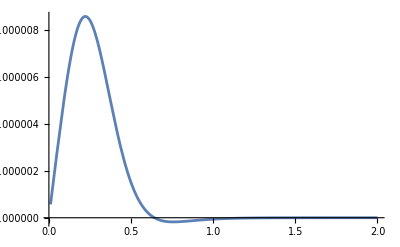

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2},PlotRange->All]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

2.83833×10^-11 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

1.49494×10^-8 λ^2 μ α^7+O[α]^10

## 511 x 511 → 422 x BH

```mathematica
ωerg[n_,α_,μ_,l_]:=μ (1-α^2/(2 n^2)-α^4/(8 n^4)+α^4/n^3(-6/(2l+1)+2/n));
```

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1/2;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=5;l1=1;m1=1;
n2=5;l2=1;m2=1;
n3=4;l3=2;m3=2;
```

```mathematica
FullSimplify[Series[ωerg[2,α,μ,1]+ωerg[5,α,μ,1]-ωerg[3,α,μ,2],{α,0,2}]]
```

μ-(161 μ α^2)/1800+O[α]^3

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,40}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {38.776}. NIntegrate obtained 9.73177×10^-8 and 1.02572×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {41.1848}. NIntegrate obtained 9.23205×10^-8 and 1.27892×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {43.9069}. NIntegrate obtained 7.60326×10^-8 and 1.0845×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

7.45115×10^-12 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = 10^Range[-2, 1.4, 0.025] μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->9,AccuracyGoal->9];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

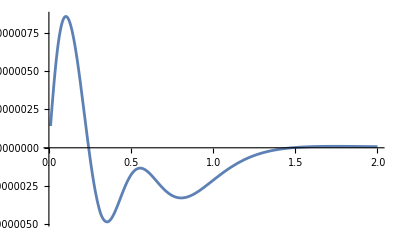

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2},PlotRange->All]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

4.41435×10^-12 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

3.95911×10^-13 λ^2 μ α^7+O[α]^10

## 511 x 522 → 433 x BH

```mathematica
ωerg[n_,α_,μ_,l_]:=μ (1-α^2/(2 n^2)-α^4/(8 n^4)+α^4/n^3(-6/(2l+1)+2/n));
```

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=5;l1=1;m1=1;
n2=5;l2=2;m2=2;
n3=4;l3=3;m3=3;
```

```mathematica
FullSimplify[Series[ωerg[2,α,μ,1]+ωerg[5,α,μ,1]-ωerg[3,α,μ,2],{α,0,2}]]
```

μ-(161 μ α^2)/1800+O[α]^3

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,40}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {39.954}. NIntegrate obtained 1.00658×10^-7 and 1.90903×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {42.5142}. NIntegrate obtained 9.01109×10^-8 and 1.31555×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {39.954}. NIntegrate obtained 8.55063×10^-8 and 1.37166×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

1.21424×10^-11 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = 10^Range[-2, 1.4, 0.025] μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

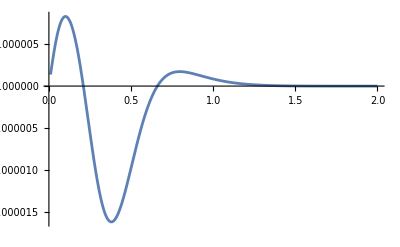

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2},PlotRange->All]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

2.27024×10^-11 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

1.63871×10^-12 λ^2 μ α^7+O[α]^10

## 511 x 511 → 522 x BH

```mathematica
ωerg[n_,α_,μ_,l_]:=μ (1-α^2/(2 n^2)-α^4/(8 n^4)+α^4/n^3(-6/(2l+1)+2/n));
```

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1/2;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=5;l1=1;m1=1;
n2=5;l2=1;m2=1;
n3=5;l3=2;m3=2;
```

```mathematica
FullSimplify[Series[ωerg[2,α,μ,1]+ωerg[5,α,μ,1]-ωerg[3,α,μ,2],{α,0,2}]]
```

μ-(161 μ α^2)/1800+O[α]^3

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,40}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {48.724}. NIntegrate obtained 1.86032×10^-7 and 1.72605×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {48.724}. NIntegrate obtained 4.97499×10^-8 and 1.67973×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {52.5219}. NIntegrate obtained -1.17974×10^-8 and 1.57841×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

4.12201×10^-12 λ^2 μ α^3-3.56714×10^-11 (λ^2 μ) α^5+7.71742×10^-11 λ^2 μ α^7+O[α]^(15/2)

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = 10^Range[-2, 1.4, 0.025] μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

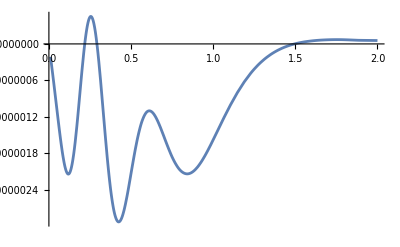

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2},PlotRange->All]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

1.22034×10^-11 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

4.12201×10^-12 λ^2 μ α^3-2.14931×10^-11 (λ^2 μ) α^5+2.80288×10^-11 λ^2 μ α^7+O[α]^8

## 511 x 522 → 533 x BH

```mathematica
ωerg[n_,α_,μ_,l_]:=μ (1-α^2/(2 n^2)-α^4/(8 n^4)+α^4/n^3(-6/(2l+1)+2/n));
```

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1/2;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=5;l1=1;m1=1;
n2=5;l2=2;m2=2;
n3=5;l3=3;m3=3;
```

```mathematica
FullSimplify[Series[ωerg[2,α,μ,1]+ωerg[5,α,μ,1]-ωerg[3,α,μ,2],{α,0,2}]]
```

μ-(161 μ α^2)/1800+O[α]^3

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,40}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {48.724}. NIntegrate obtained -4.24485×10^-8 and 1.05259×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {52.5219}. NIntegrate obtained -1.75764×10^-7 and 1.0414×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {42.5142}. NIntegrate obtained -1.54782×10^-7 and 2.0017×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

1.4604×10^-12 λ^2 μ α^3-1.6419×10^-11 (λ^2 μ) α^5+4.61487×10^-11 λ^2 μ α^7+O[α]^(15/2)

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = 10^Range[-2, 1.4, 0.025] μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

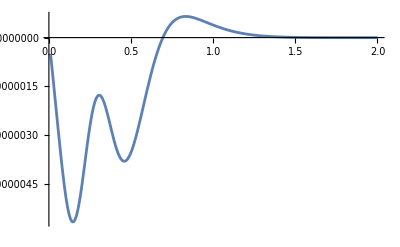

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2},PlotRange->All]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

1.27262×10^-11 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

1.4604×10^-12 λ^2 μ α^3-7.79754×10^-12 (λ^2 μ) α^5+1.04105×10^-11 λ^2 μ α^7+O[α]^8

## 511 x 533 → 544 x BH

```mathematica
ωerg[n_,α_,μ_,l_]:=μ (1-α^2/(2 n^2)-α^4/(8 n^4)+α^4/n^3(-6/(2l+1)+2/n));
```

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1/2;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=5;l1=1;m1=1;
n2=5;l2=3;m2=3;
n3=5;l3=4;m3=4;
```

```mathematica
FullSimplify[Series[ωerg[2,α,μ,1]+ωerg[5,α,μ,1]-ωerg[3,α,μ,2],{α,0,2}]]
```

μ-(161 μ α^2)/1800+O[α]^3

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,40}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {35.656}. NIntegrate obtained -1.54174×10^-7 and 1.11623×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {37.6823}. NIntegrate obtained -1.4437×10^-7 and 1.22236×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {45.4156}. NIntegrate obtained -1.35233×10^-7 and 1.16018×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

5.16143×10^-13 λ^2 μ α^3-5.96278×10^-12 (λ^2 μ) α^5+1.72214×10^-11 λ^2 μ α^7+O[α]^(15/2)

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = 10^Range[-2, 1.4, 0.025] μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

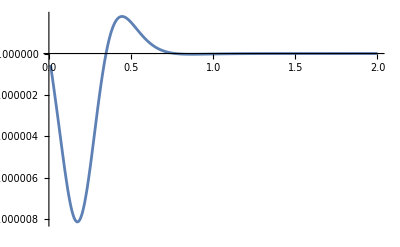

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2},PlotRange->All]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

6.23047×10^-12 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

5.16143×10^-13 λ^2 μ α^3-2.37627×10^-12 (λ^2 μ) α^5+2.73511×10^-12 λ^2 μ α^7+O[α]^8

## Old

## Not included

## 511 x 511 → 211 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1/2;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
Series[ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3],{α,0,2}]
```

μ+(17 μ α^2)/200+O[α]^3

```mathematica
n1=5;l1=1;m1=1;
n2=5;l2=1;m2=1;
n3=2;l3=1;m3=1;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

4.48213×10^-23 λ^2 μ^2 α^4+3.80981×10^-24 λ^2 μ^2 α^6+O[α]^14

```mathematica
(2.5 10^-8 α^3)/(1.7 10^-9)/.{α->.35}
```

0.630515

```mathematica
2.5 10^-8(0.33)^3(1+√(1-(.99)^2))
```

1.02516×10^-9

```mathematica
1+√(1-(.99)^2)
```

1.14107

```mathematica
(1 +3.8)/(1.7 0.75)
```

3.76471

## 511 x 511 → 322 x BH

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1/2;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=5;l1=1;m1=1;
n2=5;l2=1;m2=1;
n3=3;l3=2;m3=2;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,40}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

1.65621×10^-14 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = 10^Range[-2, 1.4, 0.025] μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

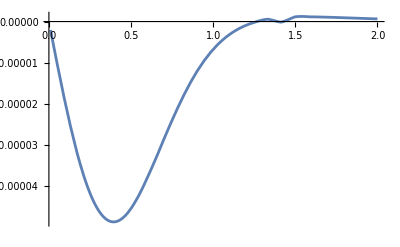

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2},PlotRange->All]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

3.5508×10^-9 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

3.22396×10^-11 λ^2 μ α^3-1.73413×10^-9 (λ^2 μ) α^5+2.33193×10^-8 λ^2 μ α^7+O[α]^8

## 511 x 511 → 422 x BH

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1/2;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=5;l1=1;m1=1;
n2=5;l2=1;m2=1;
n3=4;l3=2;m3=2;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,40}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {38.776}. NIntegrate obtained 9.73177×10^-8 and 1.02572×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {41.1848}. NIntegrate obtained 9.23205×10^-8 and 1.27892×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {43.9069}. NIntegrate obtained 7.60326×10^-8 and 1.0845×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

7.45115×10^-12 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = 10^Range[-2, 1.4, 0.025] μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

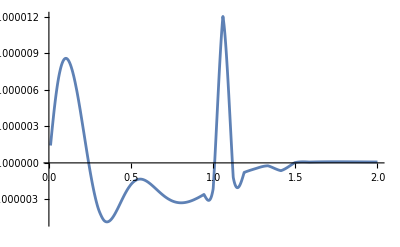

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2},PlotRange->All]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

1.46254×10^-11 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

1.92113×10^-11 λ^2 μ α^7+O[α]^10

## 511 x 511 → 522 x BH

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1/2;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=5;l1=1;m1=1;
n2=5;l2=1;m2=1;
n3=5;l3=2;m3=2;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,40}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {48.724}. NIntegrate obtained 1.86032×10^-7 and 1.72605×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {48.724}. NIntegrate obtained 4.97499×10^-8 and 1.67973×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {52.5219}. NIntegrate obtained -1.17974×10^-8 and 1.57841×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

4.12201×10^-12 λ^2 μ α^3-3.56714×10^-11 (λ^2 μ) α^5+7.71742×10^-11 λ^2 μ α^7+O[α]^(15/2)

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = 10^Range[-2, 1.4, 0.025] μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2},PlotRange->All]
```

-Graphics-

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

1.22034×10^-11 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

4.12201×10^-12 λ^2 μ α^3-2.14931×10^-11 (λ^2 μ) α^5+2.80288×10^-11 λ^2 μ α^7+O[α]^8

## 311 x 311 → 322 x BH

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1/2;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=3;l1=1;m1=1;
n2=3;l2=1;m2=1;
n3=3;l3=2;m3=2;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,40}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

1.61802×10^-10 λ^2 μ α^3-1.96766×10^-9 (λ^2 μ) α^5+5.98216×10^-9 λ^2 μ α^7+O[α]^(15/2)

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = 10^Range[-2, 1.4, 0.025] μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2},PlotRange->All]
```

-Graphics-

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

1.22034×10^-11 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

4.12201×10^-12 λ^2 μ α^3-2.14931×10^-11 (λ^2 μ) α^5+2.80288×10^-11 λ^2 μ α^7+O[α]^8

## 311 x 322 → 433 x BH

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=3;l1=1;m1=1;
n2=3;l2=2;m2=2;
n3=4;l3=3;m3=3;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,40}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

6.88979×10^-8 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = 10^Range[-2.5, 1.4, 0.025] μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2},PlotRange->All]
```

-Graphics-

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

1.09496×10^-12 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

6.9447×10^-8 λ^2 μ α^7+O[α]^10

## 411 x 411 → 211 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1/2;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=1;m1=1;
n2=4;l2=1;m2=1;
n3=2;l3=1;m3=1;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

1.72052×10^-9 λ^2 μ^2 α^4+1.07532×10^-10 λ^2 μ^2 α^6+O[α]^14

```mathematica
(2.5 10^-8 α^3)/(1.7 10^-9)/.{α->.35}
```

0.630515

```mathematica
2.5 10^-8(0.33)^3(1+√(1-(.99)^2))
```

1.02516×10^-9

```mathematica
1+√(1-(.99)^2)
```

1.14107

```mathematica
(1 +3.8)/(1.7 0.75)
```

3.76471

## 411 x 433 → 211 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=1;m1=1;
n2=4;l2=3;m2=3;
n3=2;l3=1;m3=1;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

1.09793×10^-10 λ^2 μ^2 α^4+6.86208×10^-12 λ^2 μ^2 α^6+O[α]^14

## 422 x 422 → 211 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1/2;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=2;m1=2;
n2=4;l2=2;m2=2;
n3=2;l3=1;m3=1;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

1.59401×10^-9 λ^2 μ^2 α^4+9.96256×10^-11 λ^2 μ^2 α^6+O[α]^14

## 433 x 433 → 211 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1/2;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=3;m1=3;
n2=4;l2=3;m2=3;
n3=2;l3=1;m3=1;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

9.20827×10^-11 λ^2 μ^2 α^4+5.75517×10^-12 λ^2 μ^2 α^6+O[α]^14

## 422 x 433 → 211 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=2;m1=2;
n2=4;l2=3;m2=3;
n3=2;l3=1;m3=1;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

6.07077×10^-10 λ^2 μ^2 α^4+3.79423×10^-11 λ^2 μ^2 α^6+O[α]^14

## 211 x 411 → 422 x BH

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=2;l1=1;m1=1;
n2=4;l2=1;m2=1;
n3=4;l3=2;m3=2;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,40}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

3.22396×10^-11 λ^2 μ α^3-1.05745×10^-9 (λ^2 μ) α^5+8.67097×10^-9 λ^2 μ α^7+O[α]^(15/2)

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = 10^Range[-2, 1.4, 0.025] μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2},PlotRange->All]
```

-Graphics-

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

3.5508×10^-9 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

3.22396×10^-11 λ^2 μ α^3-1.73413×10^-9 (λ^2 μ) α^5+2.33193×10^-8 λ^2 μ α^7+O[α]^8

## 411 x 422 → 433 x BH

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=1;m1=1;
n2=4;l2=2;m2=2;
n3=4;l3=3;m3=3;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,40}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

2.27885×10^-11 λ^2 μ α^3-2.9984×10^-10 (λ^2 μ) α^5+9.86286×10^-10 λ^2 μ α^7+O[α]^(15/2)

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = 10^Range[-2, 1.4, 0.025] μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

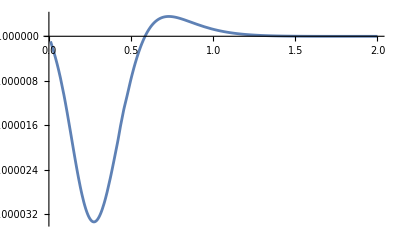

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2},PlotRange->All]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

3.37116×10^-10 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

2.27885×10^-11 λ^2 μ α^3-1.24577×10^-10 (λ^2 μ) α^5+1.7039×10^-10 λ^2 μ α^7+O[α]^8

## 422 x 522 → 544 x BH

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=2;m1=2;
n2=5;l2=2;m2=2;
n3=5;l3=4;m3=4;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,40}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

Power::infy: Infinite expression 1/0 encountered.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {33.8398}. NIntegrate obtained -6.84259×10^-7 and 1.04059×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {33.8398}. NIntegrate obtained -5.34307×10^-7 and 1.04776×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {35.656}. NIntegrate obtained -4.62629×10^-7 and 1.17234×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

ComplexInfinity

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.02]μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

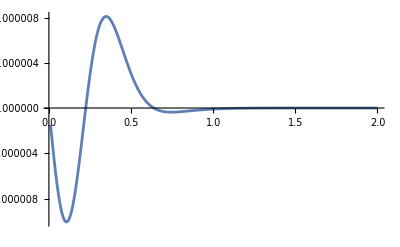

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2},PlotRange->All]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

2.08845×10^-13 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

ComplexInfinity

## 522 x 544 → 322 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=5;l1=2;m1=2;
n2=5;l2=4;m2=4;
n3=3;l3=2;m3=2;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

3.777×10^-28 λ^2 μ^2 α^4+5.87533×10^-30 λ^2 μ^2 α^6+O[α]^14

## 522 x 533 → 322 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=5;l1=2;m1=2;
n2=5;l2=3;m2=3;
n3=3;l3=2;m3=2;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

5.11989×10^-27 λ^2 μ^2 α^4+7.96427×10^-29 λ^2 μ^2 α^6+O[α]^14

## 522 x 522 → 322 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1/2;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=5;l1=2;m1=2;
n2=5;l2=2;m2=2;
n3=3;l3=2;m3=2;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

1.7613×10^-27 λ^2 μ^2 α^4+2.7398×10^-29 λ^2 μ^2 α^6+O[α]^14

## 422 x 522 → 322 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=2;m1=2;
n2=5;l2=2;m2=2;
n3=3;l3=2;m3=2;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

2.41685×10^-15 λ^2 μ^2 α^4+1.04059×10^-17 λ^2 μ^2 α^6+O[α]^14

## 433 x 522 → 322 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=3;m1=3;
n2=5;l2=2;m2=2;
n3=3;l3=2;m3=2;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

1.40922×10^-15 λ^2 μ^2 α^4+6.06748×10^-18 λ^2 μ^2 α^6+O[α]^14

## 533 x 533 → 322 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1/2;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=5;l1=3;m1=3;
n2=5;l2=3;m2=3;
n3=3;l3=2;m3=2;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

1.83732×10^-28 λ^2 μ^2 α^4+2.85805×10^-30 λ^2 μ^2 α^6+O[α]^14

## 522 x 533 → 322 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=5;l1=2;m1=2;
n2=5;l2=3;m2=3;
n3=3;l3=2;m3=2;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

5.11989×10^-27 λ^2 μ^2 α^4+7.96427×10^-29 λ^2 μ^2 α^6+O[α]^14

## 433 x 533 → 322 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=3;m1=3;
n2=5;l2=3;m2=3;
n3=3;l3=2;m3=2;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

5.22356×10^-9 λ^2 μ^2 α^4+2.24903×10^-11 λ^2 μ^2 α^6+O[α]^14

## 522 x 522 → 544 x BH [res]

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1/2;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=5;l1=2;m1=2;
n2=5;l2=2;m2=2;
n3=5;l3=4;m3=4;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,30}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {42.5142}. NIntegrate obtained -1.85246×10^-7 and 1.08832×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {35.656}. NIntegrate obtained -1.72227×10^-7 and 1.20419×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {37.6823}. NIntegrate obtained -1.60268×10^-7 and 1.32076×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

2.72071×10^-13 λ^2 μ α^3-3.27614×10^-12 (λ^2 μ) α^5+9.86237×10^-12 λ^2 μ α^7+O[α]^(15/2)

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.02]μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

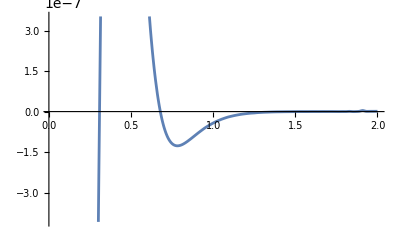

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2}]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

3.17306×10^-12 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

2.72071×10^-13 λ^2 μ α^3-1.41786×10^-12 (λ^2 μ) α^5+1.84724×10^-12 λ^2 μ α^7+O[α]^8

## 544 x 544 → 322 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1/2;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=5;l1=4;m1=4;
n2=5;l2=4;m2=4;
n3=3;l3=2;m3=2;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->20,PrecisionGoal->20,Method->"Trapezoidal"],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in r in the region {{0.,∞}}. NIntegrate obtained 0.0000284712+2.8104×10^-20 ⅈ and 2.48352×10^-20 for the integral and error estimates.

4.34778×10^-11 λ^2 μ^2 α^4+6.76321×10^-13 λ^2 μ^2 α^6+O[α]^14

## 644 x 644 → 322 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1/2;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=6;l1=4;m1=4;
n2=6;l2=4;m2=4;
n3=3;l3=2;m3=2;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->20,PrecisionGoal->20,Method->"Trapezoidal"],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

1.88002×10^-11 λ^2 μ^2 α^4+5.22228×10^-13 λ^2 μ^2 α^6+O[α]^14

## 533 x 544 → 322 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=5;l1=3;m1=3;
n2=5;l2=4;m2=4;
n3=3;l3=2;m3=2;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

1.70462×10^-28 λ^2 μ^2 α^4+2.65163×10^-30 λ^2 μ^2 α^6+O[α]^14

## 433 x 544 → 322 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=3;m1=3;
n2=5;l2=4;m2=4;
n3=3;l3=2;m3=2;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

1.38415×10^-15 λ^2 μ^2 α^4+5.95954×10^-18 λ^2 μ^2 α^6+O[α]^14

## 422 x 544 → 322 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=2;m1=2;
n2=5;l2=4;m2=4;
n3=3;l3=2;m3=2;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->20,PrecisionGoal->20,Method->"Trapezoidal"],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,4}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in r in the region {{0.,∞}}. NIntegrate obtained -0.0000173881-6.80527×10^-19 ⅈ and 2.59372×10^-19 for the integral and error estimates.

2.554×10^-11 λ^2 μ^2 α^4+O[α]^6

```mathematica
Series[ωnew,{α,0,2}]
```

μ+(31 μ α^2)/7200+O[α]^3

```mathematica
N[31/7200]
```

0.00430556

```mathematica
2.553996613135587*^-11 (0.03)^8
```

1.67568×10^-23

## 422 x 422 → 544 x BH

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1/2;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=2;m1=2;
n2=4;l2=2;m2=2;
n3=5;l3=4;m3=4;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,30}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

2.53443×10^-9 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.02]μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

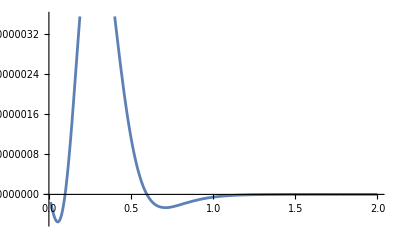

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2}]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

7.38975×10^-12 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

2.26811×10^-9 λ^2 μ α^7+O[α]^10

## 322 x 411 → 433 x BH [res]

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=3;l1=2;m1=2;
n2=4;l2=1;m2=1;
n3=4;l3=3;m3=3;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
(*Print[val/.{α->1,μ->1}];*)
,{n,1,40}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

3.80891×10^-11 λ^2 μ α^3-1.01081×10^-9 (λ^2 μ) α^5+6.70623×10^-9 λ^2 μ α^7+O[α]^(15/2)

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.02]μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

$Aborted

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

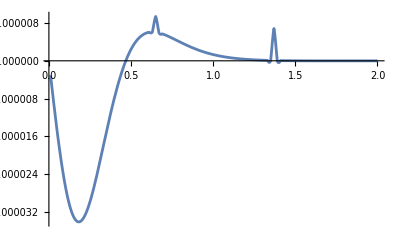

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2}]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

1.89319×10^-10 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

3.80891×10^-11 λ^2 μ α^3-1.17375×10^-9 (λ^2 μ) α^5+9.0425×10^-9 λ^2 μ α^7+O[α]^8

## 322 x 411 → 533 x BH

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=3;l1=2;m1=2;
n2=4;l2=1;m2=1;
n3=5;l3=3;m3=3;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,30}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

1.73908×10^-8 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.02]μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

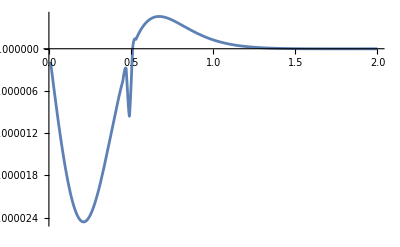

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2}]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

1.37248×10^-10 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

2.06179×10^-8 λ^2 μ α^7+O[α]^10

## 322 x 422 → 544 x BH

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=3;l1=2;m1=2;
n2=4;l2=2;m2=2;
n3=5;l3=4;m3=4;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,50}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

6.60552×10^-11 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = 10^Range[-3, 1.5, 0.1] μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->9,AccuracyGoal->9];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

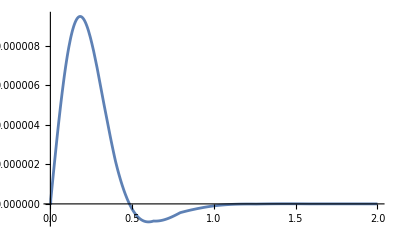

```mathematica
Plot[Re[cOfK[k]R0],{k,.001, 2}]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

2.37702×10^-11 λ^2 μ α^7+O[α]^10

```mathematica
val
```

-(4.14865×10^-6 α √(α^3 μ^3))/(√μ)

```mathematica
val2
```

(2.43768×10^-6+1.55455×10^-8 ⅈ) α^(5/2) μ

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

1.30248×10^-11 λ^2 μ α^7+O[α]^10

```mathematica
1.17 10^-11 α^11/.{α->0.0493955168}
```

4.99745×10^-26

## 322 x 422 → 544 x BH

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=3;l1=2;m1=2;
n2=4;l2=2;m2=2;
n3=5;l3=4;m3=4;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,30}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

6.69992×10^-11 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.02]μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

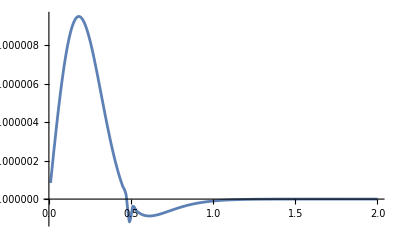

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2}]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

2.08626×10^-11 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

1.30889×10^-11 λ^2 μ α^7+O[α]^10

## 322 x 522 → 544 x BH [res]

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=3;l1=2;m1=2;
n2=5;l2=2;m2=2;
n3=5;l3=4;m3=4;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,30}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

3.44587×10^-12 λ^2 μ α^3+3.23358×10^-11 λ^2 μ α^5+7.58593×10^-11 λ^2 μ α^7+O[α]^(15/2)

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.02]μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

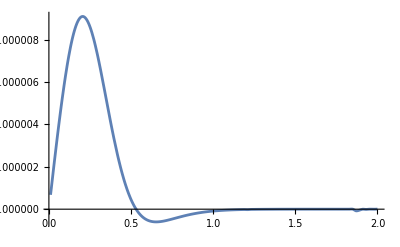

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2}]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

2.46802×10^-11 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

3.44587×10^-12 λ^2 μ α^3+5.07798×10^-11 λ^2 μ α^5+1.87078×10^-10 λ^2 μ α^7+O[α]^8

## 211 x 311 → 322 x BH [res]

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=2;l1=1;m1=1;
n2=3;l2=1;m2=1;
n3=3;l3=2;m3=2;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,20}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

3.11168×10^-10 λ^2 μ α^3-8.40007×10^-9 (λ^2 μ) α^5+5.66906×10^-8 λ^2 μ α^7+O[α]^(15/2)

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.02]μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

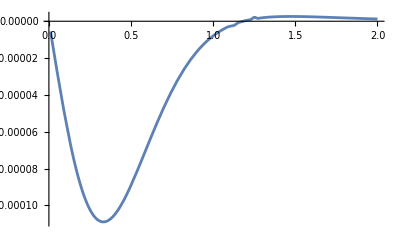

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2}]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

1.46762×10^-8 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

3.11168×10^-10 λ^2 μ α^3-1.26741×10^-8 (λ^2 μ) α^5+1.29056×10^-7 λ^2 μ α^7+O[α]^8

## 432 x 211 → 543 x BH

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=3;m1=2;
n2=3;l2=1;m2=1;
n3=5;l3=4;m3=3;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,20}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

1.22298×10^-8 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.02]μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

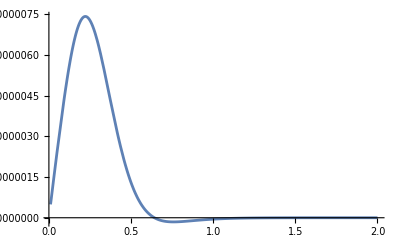

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2}]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

2.19455×10^-11 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

1.12156×10^-8 λ^2 μ α^7+O[α]^10

## 432 x 211 → 433 x BH

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=3;m1=2;
n2=3;l2=1;m2=1;
n3=4;l3=3;m3=3;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,20}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

0.

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.02]μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

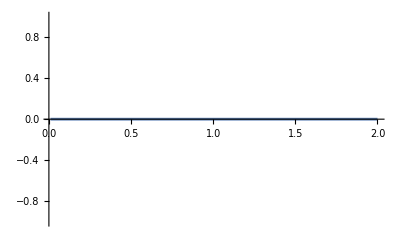

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2}]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

0.

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

0.

## 211 x 211 → 432 x BH (l = 1, 3, 5....)

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1/2;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=2;l1=1;m1=1;
n2=2;l2=1;m2=1;
n3=4;l3=3;m3=2;
```

```mathematica
val=0;
Do[
If[n>l+1,
CG = Block[{m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,l,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
RbatZero=Normal[Series[Rb[n,l,r],{r,0,1}]]/.{r-> α/μ};
val+=RbatZero(CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};]
,{n,1,20},{l,1,5}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,15}],α>0&&μ>0]
```

4.18097×10^-14 λ^2 μ α^11+O[α]^(31/2)

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.02]μ α ;
clist = {};
CG = Block[{l=1,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ](-1)^l SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,1,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

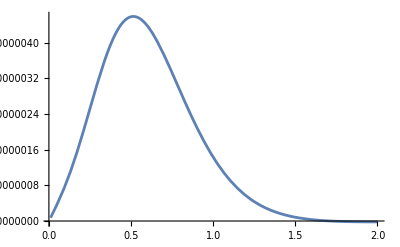

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2}]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

3.90369×10^-11 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

3.90369×10^-11 λ^2 μ α^7+2.55509×10^-12 λ^2 μ α^9+O[α]^10

```mathematica
R0=Series[Rinf[k,3,r],{r,0,3}]/(α μ)/.{a0-> 1/(μ α),k-> k α μ}
```

1/315 ⅇ^(π/(2 k)) k^4 α^3 μ^3 Abs[Gamma[4-ⅈ/k]] r^3+O[r]^4

```mathematica
R0=Series[Rinf[k,0,r],{r,0,0}]/(α μ)/.{a0-> 1/(μ α),k-> k α μ}
```

2 ⅇ^(π/(2 k)) k Abs[Gamma[1-ⅈ/k]]+O[r]^1

## 211 x 411 → 432 x BH (l = 1, 3, 5....)

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=2;l1=1;m1=1;
n2=4;l2=1;m2=1;
n3=4;l3=3;m3=2;
```

```mathematica
val=0;
Do[
If[n>l+1,
CG = Block[{m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,l,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
RbatZero=Normal[Series[Rb[n,l,r],{r,0,1}]]/.{r-> α/μ};
val+=RbatZero(CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};]
,{n,1,20},{l,1,5}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,15}],α>0&&μ>0]
```

2.2066×10^-11 λ^2 μ α^11+O[α]^(31/2)

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.02]μ α ;
clist = {};
CG = Block[{l=1,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ](-1)^l SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,1,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

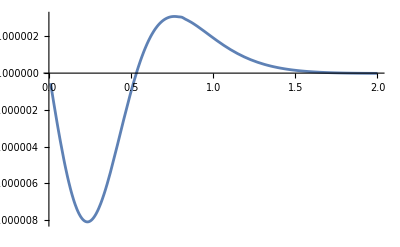

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2}]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

4.94064×10^-12 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

4.94064×10^-12 λ^2 μ α^7-2.08826×10^-11 (λ^2 μ) α^9+O[α]^10

## 211 x 211 → 522 x BH

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1/2;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=2;l1=1;m1=1;
n2=2;l2=1;m2=1;
n3=5;l3=2;m3=2;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,20}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

6.04994×10^-8 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.02]μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

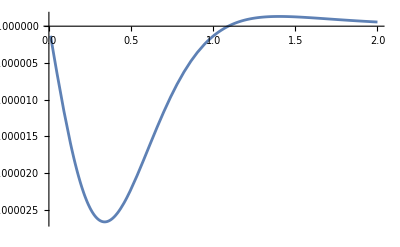

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2}]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

8.03977×10^-10 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

7.52519×10^-8 λ^2 μ α^7+O[α]^10

## 211 x 411 → 522 x BH

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=2;l1=1;m1=1;
n2=4;l2=1;m2=1;
n3=5;l3=2;m3=2;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,20}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

7.43058×10^-8 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.02]μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

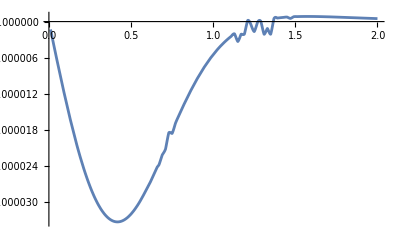

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2}]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

1.80694×10^-9 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

9.92874×10^-8 λ^2 μ α^7+O[α]^10

## 411 x 411 → 522 x BH

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1/2;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=1;m1=1;
n2=4;l2=1;m2=1;
n3=5;l3=2;m3=2;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,50}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

2.58697×10^-10 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.02]μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->10,AccuracyGoal->10];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

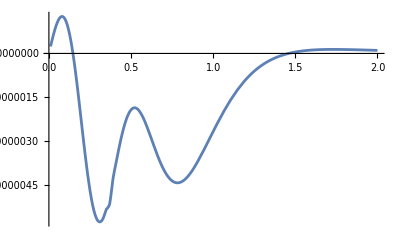

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2}]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

4.28345×10^-11 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

9.00082×10^-11 λ^2 μ α^7+O[α]^10

## 522 x 411 → 433 x BH [res]

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=5;l1=2;m1=2;
n2=4;l2=1;m2=1;
n3=4;l3=3;m3=3;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,20}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

4.52182×10^-12 λ^2 μ α^3-5.24366×10^-11 (λ^2 μ) α^5+1.52018×10^-10 λ^2 μ α^7+O[α]^(15/2)

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.02]μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

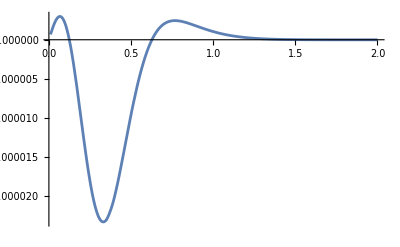

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2}]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

1.14662×10^-10 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

4.52182×10^-12 λ^2 μ α^3-6.89616×10^-12 (λ^2 μ) α^5+2.62935×10^-12 λ^2 μ α^7+O[α]^8

## 522 x 211 → 433 x BH

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1/2;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=5;l1=2;m1=2;
n2=2;l2=1;m2=1;
n3=4;l3=3;m3=3;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,20}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

1.52952×10^-8 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.02]μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

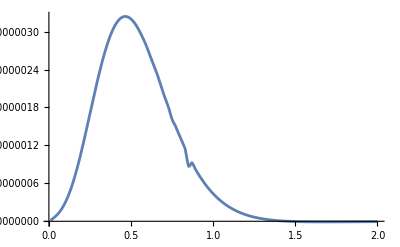

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2}]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

1.23513×10^-11 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

1.61765×10^-8 λ^2 μ α^7+O[α]^10

## 522 x 322 → 544 x BH [res]

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=5;l1=2;m1=2;
n2=3;l2=2;m2=2;
n3=5;l3=4;m3=4;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,20}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

3.44587×10^-12 λ^2 μ α^3+3.20023×10^-11 λ^2 μ α^5+7.43026×10^-11 λ^2 μ α^7+O[α]^(15/2)

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.02]μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2}]
```

-Graphics-

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

2.46802×10^-11 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

3.44587×10^-12 λ^2 μ α^3+5.04463×10^-11 λ^2 μ α^5+1.84629×10^-10 λ^2 μ α^7+O[α]^8

## 622 x 322 → 544 x BH [res]

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=7;l1=6;m1=6;
n2=3;l2=2;m2=2;
n3=9;l3=8;m3=8;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,20}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

1.70224×10^-16 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.02]μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2}]
```

-Graphics-

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

2.46802×10^-11 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

3.44587×10^-12 λ^2 μ α^3+5.04463×10^-11 λ^2 μ α^5+1.84629×10^-10 λ^2 μ α^7+O[α]^8

## 522 x 422 → 544 x BH [res]

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=5;l1=2;m1=2;
n2=4;l2=2;m2=2;
n3=5;l3=4;m3=4;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,20}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {33.8398}. NIntegrate obtained -6.84259×10^-7 and 1.04059×10^-18 for the integral and error estimates.

3.71129×10^-14 λ^2 μ α^3-1.06112×10^-11 (λ^2 μ) α^5+7.58473×10^-10 λ^2 μ α^7+O[α]^(15/2)

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.02]μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

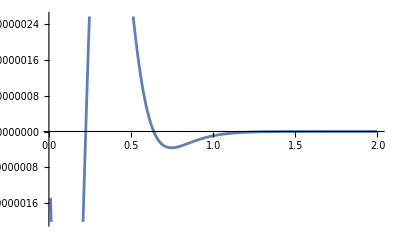

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2}]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

2.08845×10^-13 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

3.71129×10^-14 λ^2 μ α^3-1.04351×10^-11 (λ^2 μ) α^5+7.33511×10^-10 λ^2 μ α^7+O[α]^8

## 522 x 411 → 211 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=5;l1=2;m1=2;
n2=4;l2=1;m2=1;
n3=2;l3=1;m3=1;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity}],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

8.05981×10^-10 λ^2 μ^2 α^4+5.94411×10^-11 λ^2 μ^2 α^6+O[α]^14

## 522 x 422 → 211 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=5;l1=2;m1=2;
n2=4;l2=2;m2=2;
n3=2;l3=1;m3=1;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},PrecisionGoal->8,AccuracyGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

3.74027×10^-9 λ^2 μ^2 α^4+2.75845×10^-10 λ^2 μ^2 α^6+O[α]^14

## 522 x 433 → 211 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=5;l1=2;m1=2;
n2=4;l2=3;m2=3;
n3=2;l3=1;m3=1;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity}],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

2.70955×10^-10 λ^2 μ^2 α^4+1.99829×10^-11 λ^2 μ^2 α^6+O[α]^14

## 522 x 322 → 211 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=5;l1=2;m1=2;
n2=3;l2=2;m2=2;
n3=2;l3=1;m3=1;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

7.65856×10^-9 λ^2 μ^2 α^4+3.78673×10^-10 λ^2 μ^2 α^6+O[α]^14

## 533 x 211 → 544 x BH [res]

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=5;l1=3;m1=3;
n2=2;l2=1;m2=1;
n3=5;l3=4;m3=4;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,20}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

4.58324×10^-13 λ^2 μ α^3+3.85263×10^-12 λ^2 μ α^5+8.09623×10^-12 λ^2 μ α^7+O[α]^(15/2)

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.02]μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->10,AccuracyGoal->10];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

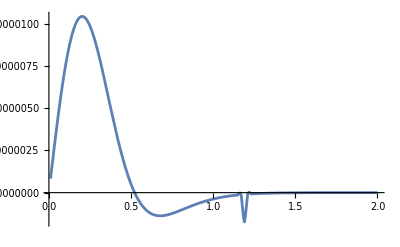

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2}]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

2.72699×10^-13 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

4.58324×10^-13 λ^2 μ α^3+4.55964×10^-12 λ^2 μ α^5+1.13405×10^-11 λ^2 μ α^7+O[α]^8

## 522 x 422 → 544 x BH [res]

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=5;l1=2;m1=2;
n2=4;l2=2;m2=2;
n3=5;l3=4;m3=4;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,20}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {33.8398}. NIntegrate obtained -6.84259×10^-7 and 1.04059×10^-18 for the integral and error estimates.

3.71129×10^-14 λ^2 μ α^3-1.06112×10^-11 (λ^2 μ) α^5+7.58473×10^-10 λ^2 μ α^7+O[α]^(15/2)

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.02]μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2},PlotRange->All]
```

-Graphics-

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

2.08845×10^-13 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

3.71129×10^-14 λ^2 μ α^3-1.04351×10^-11 (λ^2 μ) α^5+7.33511×10^-10 λ^2 μ α^7+O[α]^8

## 211 x 322 → 533 x BH

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=2;l1=1;m1=1;
n2=3;l2=2;m2=2;
n3=5;l3=3;m3=3;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,20}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

6.04994×10^-8 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.02]μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

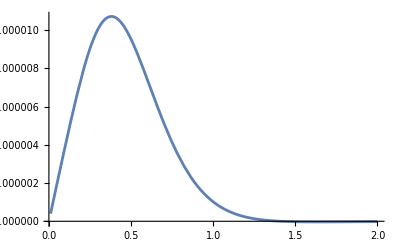

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2}]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

1.51365×10^-10 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

3.08791×10^-8 λ^2 μ α^7+O[α]^10

## 211 x 422 → 533 x BH

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=2;l1=1;m1=1;
n2=4;l2=2;m2=2;
n3=5;l3=3;m3=3;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,20}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

1.20302×10^-7 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.02]μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->9,AccuracyGoal->9];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

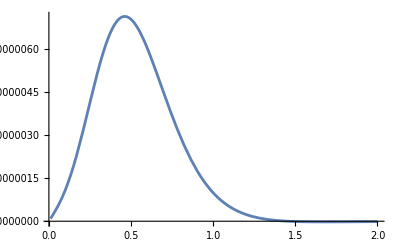

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2}]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

6.4759×10^-11 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

1.14785×10^-7 λ^2 μ α^7+O[α]^10

## 411 x 322 → 533 x BH

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=1;m1=1;
n2=3;l2=2;m2=2;
n3=5;l3=3;m3=3;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,20}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

1.73256×10^-8 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.02]μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2}]
```

-Graphics-

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

1.37248×10^-10 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

2.05469×10^-8 λ^2 μ α^7+O[α]^10

## 411 x 422 → 533 x BH

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=1;m1=1;
n2=4;l2=2;m2=2;
n3=5;l3=3;m3=3;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,20}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {27.0466}. NIntegrate obtained -6.40533×10^-8 and 1.07057×10^-18 for the integral and error estimates.

5.21029×10^-10 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.02]μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

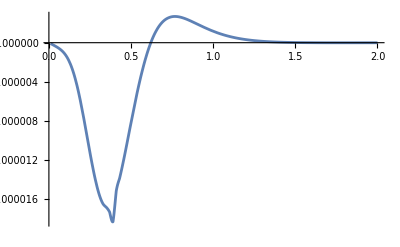

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2}]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

6.25926×10^-11 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

9.44797×10^-10 λ^2 μ α^7+O[α]^10

## 544 x 211 → 655 x BH

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=5;l1=4;m1=4;
n2=2;l2=1;m2=1;
n3=6;l3=5;m3=5;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,20}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

3.41766×10^-12 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.02]μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->10,AccuracyGoal->10];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

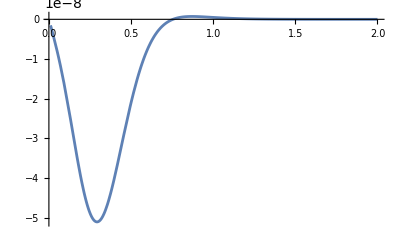

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2}]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

1.27745×10^-15 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

3.55109×10^-12 λ^2 μ α^7+O[α]^10

## 322 x 322 → 544 x BH

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1/2;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=3;l1=2;m1=2;
n2=3;l2=2;m2=2;
n3=5;l3=4;m3=4;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,30}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

1.91204×10^-9 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.02]μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

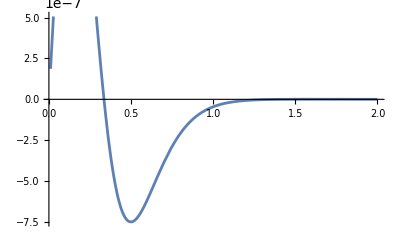

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2}]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

2.86687×10^-14 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

1.92465×10^-9 λ^2 μ α^7+O[α]^10

## 211 x 433 → 544 x BH

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=2;l1=1;m1=1;
n2=4;l2=3;m2=3;
n3=5;l3=4;m3=4;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,20}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

1.14983×10^-9 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = Range[0.01, 2, 0.02]μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->7,AccuracyGoal->7];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

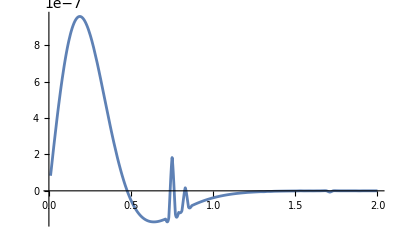

```mathematica
Plot[Re[cOfK[k]R0],{k,.01, 2}]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

1.96782×10^-13 λ^2 μ α^7+O[α]^10

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

1.12119×10^-9 λ^2 μ α^7+O[α]^10

## 322 x 544 → 211 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=3;l1=2;m1=2;
n2=5;l2=4;m2=4;
n3=2;l3=1;m3=1;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

6.12419×10^-11 λ^2 μ^2 α^4+3.02807×10^-12 λ^2 μ^2 α^6+O[α]^14

## 433 x 544 → 211 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=3;m1=3;
n2=5;l2=4;m2=4;
n3=2;l3=1;m3=1;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

2.43838×10^-11 λ^2 μ^2 α^4+1.7983×10^-12 λ^2 μ^2 α^6+O[α]^14

## 544 x 544 → 211 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1/2;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=5;l1=4;m1=4;
n2=5;l2=4;m2=4;
n3=2;l3=1;m3=1;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

9.439×10^-21 λ^2 μ^2 α^4+8.02315×10^-22 λ^2 μ^2 α^6+O[α]^14

## 522 x 544 → 322 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=5;l1=2;m1=2;
n2=5;l2=4;m2=4;
n3=3;l3=2;m3=2;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

3.777×10^-28 λ^2 μ^2 α^4+5.87533×10^-30 λ^2 μ^2 α^6+O[α]^14

## 522 x 433 → 322 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=5;l1=2;m1=2;
n2=4;l2=3;m2=3;
n3=3;l3=2;m3=2;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

1.40922×10^-15 λ^2 μ^2 α^4+6.06748×10^-18 λ^2 μ^2 α^6+O[α]^14

## 522 x 422 → 322 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=5;l1=2;m1=2;
n2=4;l2=2;m2=2;
n3=3;l3=2;m3=2;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

1.40922×10^-15 λ^2 μ^2 α^4+6.06748×10^-18 λ^2 μ^2 α^6+O[α]^14

## 522 x 411 → 322 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=5;l1=2;m1=2;
n2=4;l2=1;m2=1;
n3=3;l3=2;m3=2;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

1.0151×10^-15 λ^2 μ^2 α^4+4.37056×10^-18 λ^2 μ^2 α^6+O[α]^14

## 433 x 544 → 322 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=5;l1=4;m1=4;
n2=4;l2=3;m2=3;
n3=3;l3=2;m3=2;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

1.38415×10^-15 λ^2 μ^2 α^4+5.95954×10^-18 λ^2 μ^2 α^6+O[α]^14

## 422 x 533 → 322 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=2;m1=2;
n2=5;l2=3;m2=3;
n3=3;l3=2;m3=2;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)RinfC[kuse,l2+l1-l3,r ]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},PrecisionGoal->15,AccuracyGoal->15,Method->"QuasiMonteCarlo"],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,1}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,4}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained 0.000126154-3.80161×10^-21 ⅈ and 2.21183×10^-6 for the integral and error estimates.

1.24663×10^-9 λ^2 μ^2 α^4+O[α]^6

## 422 x 544 → 322 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=2;m1=2;
n2=5;l2=4;m2=4;
n3=3;l3=2;m3=2;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)RinfC[kuse,l2+l1-l3,r ]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},PrecisionGoal->15,AccuracyGoal->15,Method->"QuasiMonteCarlo"],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,1}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,4}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained -0.0000173881+1.04117×10^-19 ⅈ and 1.28119×10^-6 for the integral and error estimates.

2.554×10^-11 λ^2 μ^2 α^4+O[α]^6

## 433 x 544 → 322 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=3;m1=3;
n2=5;l2=4;m2=4;
n3=3;l3=2;m3=2;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)RinfC[kuse,l2+l1-l3,r ]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},PrecisionGoal->15,AccuracyGoal->15,Method->"QuasiMonteCarlo"],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,1}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,4}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained 0.0000910523-3.7898×10^-20 ⅈ and 2.07639×10^-6 for the integral and error estimates.

7.82904×10^-10 λ^2 μ^2 α^4+O[α]^6

## 422 x 533 → 322 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=2;m1=2;
n2=5;l2=3;m2=3;
n3=3;l3=2;m3=2;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)RinfC[kuse,l2+l1-l3,r ]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},PrecisionGoal->15,AccuracyGoal->15,Method->"QuasiMonteCarlo"],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,1}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,4}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained 0.000126154-3.80161×10^-21 ⅈ and 2.21183×10^-6 for the integral and error estimates.

1.24663×10^-9 λ^2 μ^2 α^4+O[α]^6

## 433 x 533 → 322 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=3;m1=3;
n2=5;l2=3;m2=3;
n3=3;l3=2;m3=2;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)RinfC[kuse,l2+l1-l3,r ]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},PrecisionGoal->15,AccuracyGoal->15,Method->"QuasiMonteCarlo"],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,1}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,4}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained 0.000179317+3.891×10^-20 ⅈ and 3.54457×10^-6 for the integral and error estimates.

2.81675×10^-9 λ^2 μ^2 α^4+O[α]^6

## 433 x 522 → 322 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=3;m1=3;
n2=5;l2=2;m2=2;
n3=3;l3=2;m3=2;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)RinfC[kuse,l2+l1-l3,r ]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},PrecisionGoal->15,AccuracyGoal->15,Method->"QuasiMonteCarlo"],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,1}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,4}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained 0.0000899131-1.5583×10^-19 ⅈ and 1.77996×10^-6 for the integral and error estimates.

6.33255×10^-10 λ^2 μ^2 α^4+O[α]^6

## 422 x 522 → 322 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=2;m1=2;
n2=5;l2=2;m2=2;
n3=3;l3=2;m3=2;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)RinfC[kuse,l2+l1-l3,r ]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},PrecisionGoal->15,AccuracyGoal->15,Method->"QuasiMonteCarlo"],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,1}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,4}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained 0.000150254+3.18466×10^-19 ⅈ and 2.51627×10^-6 for the integral and error estimates.

1.57209×10^-9 λ^2 μ^2 α^4+O[α]^6

## 422 x 533 → 322 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=2;m1=2;
n2=5;l2=3;m2=3;
n3=3;l3=2;m3=2;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)RinfC[kuse,l2+l1-l3,r ]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
(*ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},PrecisionGoal->15,AccuracyGoal->15,Method->"QuasiMonteCarlo"],α>0&&μ>0&&r∈Reals];*)
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},PrecisionGoal->12,AccuracyGoal->12,Method->"Trapezoidal"],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,1}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,4}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

1.24663×10^-9 λ^2 μ^2 α^4+O[α]^6

## 522 x 544 → 322 x Inf [*]

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=5;l1=2;m1=2;
n2=5;l2=4;m2=4;
n3=3;l3=2;m3=2;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)RinfC[kuse,l2+l1-l3,r ]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},PrecisionGoal->15,AccuracyGoal->15,Method->"QuasiMonteCarlo"],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,1}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,4}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained -0.0000223177+6.89047×10^-20 ⅈ and 1.1324×10^-6 for the integral and error estimates.

2.21353×10^-11 λ^2 μ^2 α^4+O[α]^6

## 533 x 544 → 322 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=5;l1=3;m1=3;
n2=5;l2=4;m2=4;
n3=3;l3=2;m3=2;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)RinfC[kuse,l2+l1-l3,r ]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},PrecisionGoal->15,AccuracyGoal->15,Method->"QuasiMonteCarlo"],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,1}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,4}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained 0.0000606328-1.84285×10^-20 ⅈ and 1.3903×10^-6 for the integral and error estimates.

1.82647×10^-10 λ^2 μ^2 α^4+O[α]^6

## 544 x 544 → 322 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1/2;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=5;l1=4;m1=4;
n2=5;l2=4;m2=4;
n3=3;l3=2;m3=2;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)RinfC[kuse,l2+l1-l3,r ]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},PrecisionGoal->15,AccuracyGoal->15,Method->"QuasiMonteCarlo"],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,1}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,4}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained 0.0000284712-6.5471×10^-21 ⅈ and 7.35651×10^-7 for the integral and error estimates.

4.34778×10^-11 λ^2 μ^2 α^4+O[α]^6

## 522 x 533 → 322 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=5;l1=2;m1=2;
n2=5;l2=3;m2=3;
n3=3;l3=2;m3=2;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)RinfC[kuse,l2+l1-l3,r ]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},PrecisionGoal->15,AccuracyGoal->15,Method->"QuasiMonteCarlo"],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,1}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,4}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained 0.000103727+7.28994×10^-20 ⅈ and 1.79697×10^-6 for the integral and error estimates.

4.4339×10^-10 λ^2 μ^2 α^4+O[α]^6

## 533 x 533 → 322 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1/2;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=5;l1=3;m1=3;
n2=5;l2=3;m2=3;
n3=3;l3=2;m3=2;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)RinfC[kuse,l2+l1-l3,r ]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},PrecisionGoal->15,AccuracyGoal->15,Method->"QuasiMonteCarlo"],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,1}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,4}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained 0.0000829505-2.01986×10^-20 ⅈ and 1.66631×10^-6 for the integral and error estimates.

3.17116×10^-10 λ^2 μ^2 α^4+O[α]^6

## 522 x 522 → 322 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1/2;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=5;l1=2;m1=2;
n2=5;l2=2;m2=2;
n3=3;l3=2;m3=2;
```

```mathematica
goal=20;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)RinfC[kuse,l2+l1-l3,r ]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
(*ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},PrecisionGoal->goal,AccuracyGoal->goal,Method->"QuasiMonteCarlo"],α>0&&μ>0&&r∈Reals];*)
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},PrecisionGoal->goal,AccuracyGoal->goal,Method->"Trapezoidal"],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,1}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,4}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in r in the region {{0.,∞}}. NIntegrate obtained 0.0000662559+1.22277×10^-20 ⅈ and 1.1144×10^-19 for the integral and error estimates.

1.60822×10^-10 λ^2 μ^2 α^4+O[α]^6

## 322 x 544 → 766 x BH [*]

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=3;l1=2;m1=2;
n2=5;l2=4;m2=4;
n3=7;l3=6;m3=6;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,60}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

5.90169×10^-12 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = 10^Range[-3, 1.5, 0.1] μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->9,AccuracyGoal->9];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

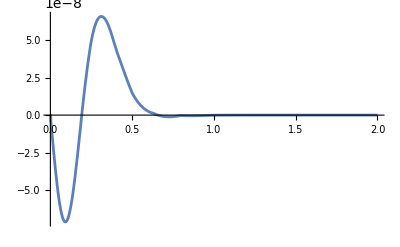

```mathematica
Plot[Re[cOfK[k]R0],{k,.001, 2},PlotRange->All]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

1.24247×10^-15 λ^2 μ α^7+O[α]^10

```mathematica
val
```

-(4.14865×10^-6 α √(α^3 μ^3))/(√μ)

```mathematica
val2
```

(2.43768×10^-6+1.55455×10^-8 ⅈ) α^(5/2) μ

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

6.0719×10^-12 λ^2 μ α^7+O[α]^10

```mathematica
1.17 10^-11 α^11/.{α->0.0493955168}
```

4.99745×10^-26

## 322 x 322 → 644 x BH [*]

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1/2;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=3;l1=2;m1=2;
n2=3;l2=2;m2=2;
n3=6;l3=4;m3=4;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,50}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

2.05085×10^-9 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = 10^Range[-3, 1.5, 0.1] μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->9,AccuracyGoal->9];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

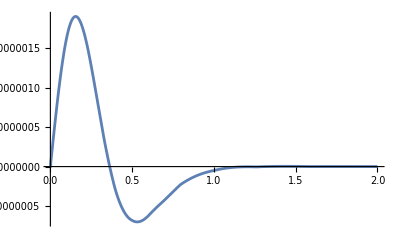

```mathematica
Plot[Re[cOfK[k]R0],{k,.001, 2},PlotRange->All]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

4.2766×10^-14 λ^2 μ α^7+O[α]^10

```mathematica
val
```

(0.0000226432 α √(α^3 μ^3))/(√μ)

```mathematica
val2
```

(1.02984×10^-7-9.26056×10^-9 ⅈ) α^(5/2) μ

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

2.06955×10^-9 λ^2 μ α^7+O[α]^10

```mathematica
1.17 10^-11 α^11/.{α->0.0493955168}
```

4.99745×10^-26

## 644 x 322 → 766 x BH [*]

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=3;l1=2;m1=2;
n2=6;l2=4;m2=4;
n3=7;l3=6;m3=6;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,50}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

3.11789×10^-11 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = 10^Range[-3, 1.5, 0.1] μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->9,AccuracyGoal->9];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

```mathematica
Plot[Re[cOfK[k]R0],{k,.001, 2},PlotRange->All]
```

-Graphics-

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

4.2766×10^-14 λ^2 μ α^7+O[α]^10

```mathematica
val
```

(0.0000226432 α √(α^3 μ^3))/(√μ)

```mathematica
val2
```

(1.02984×10^-7-9.26056×10^-9 ⅈ) α^(5/2) μ

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

2.06955×10^-9 λ^2 μ α^7+O[α]^10

```mathematica
1.17 10^-11 α^11/.{α->0.0493955168}
```

4.99745×10^-26

## 544 x 544 → 988 x BH [*]

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1/2;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=5;l1=4;m1=4;
n2=5;l2=4;m2=4;
n3=9;l3=8;m3=8;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,50}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

1.59696×10^-12 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = 10^Range[-3, 1.5, 0.1] μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->9,AccuracyGoal->9];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

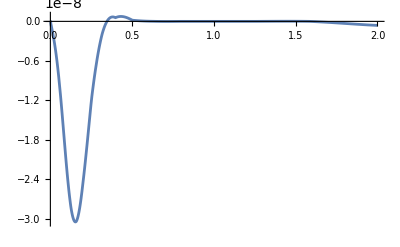

```mathematica
Plot[Re[cOfK[k]R0],{k,.001, 2},PlotRange->All]
```

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

6.88085×10^-16 λ^2 μ α^7+O[α]^10

```mathematica
val
```

-(6.31854×10^-7 α √(α^3 μ^3))/(√μ)

```mathematica
val2
```

(-1.2976×10^-8-1.90894×10^-9 ⅈ) α^(5/2) μ

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

1.66324×10^-12 λ^2 μ α^7+O[α]^10

```mathematica
1.17 10^-11 α^11/.{α->0.0493955168}
```

4.99745×10^-26

```mathematica
1.6632389824953647*^-12 (0.9)^11
```

5.21942×10^-13

## 766 x 322 → 988 x BH [*]

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=7;l1=6;m1=6;
n2=3;l2=2;m2=2;
n3=9;l3=8;m3=8;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,50}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

1.71038×10^-16 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = 10^Range[-3, 1.5, 0.1] μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->9,AccuracyGoal->9];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

```mathematica
Plot[Re[cOfK[k]R0],{k,.001, 2},PlotRange->All]
```

-Graphics-

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

6.88085×10^-16 λ^2 μ α^7+O[α]^10

```mathematica
val
```

-(6.31854×10^-7 α √(α^3 μ^3))/(√μ)

```mathematica
val2
```

(-1.2976×10^-8-1.90894×10^-9 ⅈ) α^(5/2) μ

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

1.66324×10^-12 λ^2 μ α^7+O[α]^10

```mathematica
1.17 10^-11 α^11/.{α->0.0493955168}
```

4.99745×10^-26

## 544 x 766 → 322 x Inf [*]

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=5;l1=4;m1=4;
n2=7;l2=6;m2=6;
n3=3;l3=2;m3=2;
```

```mathematica
goal=20;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)RinfC[kuse,l2+l1-l3,r ]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
(*ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},PrecisionGoal->goal,AccuracyGoal->goal,Method->"QuasiMonteCarlo"],α>0&&μ>0&&r∈Reals];*)
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},PrecisionGoal->goal,AccuracyGoal->goal,Method->"Trapezoidal"],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,1}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,4}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

7.64947×10^-13 λ^2 μ^2 α^4+O[α]^6

```mathematica
Solve[(ξ1 2.0695496560304987*^-9   (8 10^-5 α^12)    -1.9246463509711576*^-9  α^11 ϵ3 ϵ5)ϵ3==0,ϵ3]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{ϵ3→0},{ϵ3→(0.0000860231 α ξ1)/ϵ5}}

```mathematica
Solve[(ξ2 1.9246463509711576*^-9  α^11 (0.00008602306205443818 α ξ1)/ϵ5  -4.3477762506001576*^-11 α^8  ϵ5 )ϵ3ϵ5==0,ϵ5]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{ϵ5→-0.0617091 α^2 √ξ1 √ξ2},{ϵ5→0.0617091 α^2 √ξ1 √ξ2}}

```mathematica
Solve[(ξ2 6.071901302251895*^-12  α^11- 7.649471640372019*^-13 α^8)==0,α]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{α→0.},{α→0.},{α→0.},{α→0.},{α→0.},{α→0.},{α→0.},{α→0.},{α→-(0.250653-0.434143 ⅈ)/ξ2^(1/3)},{α→-(0.250653+0.434143 ⅈ)/ξ2^(1/3)},{α→0.501305/ξ2^(1/3)}}

## 544 x 766 → 422 x Inf [*]

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=5;l1=4;m1=4;
n2=7;l2=6;m2=6;
n3=4;l3=2;m3=2;
```

```mathematica
goal=20;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)RinfC[kuse,l2+l1-l3,r ]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
(*ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},PrecisionGoal->goal,AccuracyGoal->goal,Method->"QuasiMonteCarlo"],α>0&&μ>0&&r∈Reals];*)
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},PrecisionGoal->goal,AccuracyGoal->goal,Method->"Trapezoidal"],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,1}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,4}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in r in the region {{0.,∞}}. NIntegrate obtained -7.12462×10^-6-2.55336×10^-21 ⅈ and 3.17014×10^-20 for the integral and error estimates.

1.15952×10^-11 λ^2 μ^2 α^4+O[α]^6

```mathematica
Series[ωnew,{α,0,2}]
```

μ+(41 μ α^2)/39200+O[α]^3

```mathematica
Solve[(ξ1 2.0695496560304987*^-9   (8 10^-5 α^12)    -1.9246463509711576*^-9  α^11 ϵ3 ϵ5)ϵ3==0,ϵ3]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{ϵ3→0},{ϵ3→(0.0000860231 α ξ1)/ϵ5}}

```mathematica
Solve[(ξ2 1.9246463509711576*^-9  α^11 (0.00008602306205443818 α ξ1)/ϵ5  -4.3477762506001576*^-11 α^8  ϵ5 )ϵ3ϵ5==0,ϵ5]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{ϵ5→-0.0617091 α^2 √ξ1 √ξ2},{ϵ5→0.0617091 α^2 √ξ1 √ξ2}}

```mathematica
Solve[(ξ2 6.071901302251895*^-12  α^11- 7.649471640372019*^-13 α^8)==0,α]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{α→0.},{α→0.},{α→0.},{α→0.},{α→0.},{α→0.},{α→0.},{α→0.},{α→-(0.250653-0.434143 ⅈ)/ξ2^(1/3)},{α→-(0.250653+0.434143 ⅈ)/ξ2^(1/3)},{α→0.501305/ξ2^(1/3)}}

```mathematica
Series[ωerg[9,α,μ,8]+ωerg[9,α,μ,8]-ωerg[4,α,μ,3],{α,0,2}]
```

μ+(49 μ α^2)/2592+O[α]^3

## 766 x 766 → 322 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1/2;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=7;l1=6;m1=6;
n2=7;l2=6;m2=6;
n3=3;l3=2;m3=2;
```

```mathematica
goal=20;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)RinfC[kuse,l2+l1-l3,r ]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
(*ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},PrecisionGoal->goal,AccuracyGoal->goal,Method->"QuasiMonteCarlo"],α>0&&μ>0&&r∈Reals];*)
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},PrecisionGoal->goal,AccuracyGoal->goal,Method->"Trapezoidal"],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,1}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,4}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

5.21889×10^-15 λ^2 μ^2 α^4+O[α]^6

```mathematica
Solve[(- 5.218893371944077*^-15 α^8 ϵ7 +6.071901302251895*^-12  α^11 ϵ5)ϵ3ϵ7==0,α]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{α→0.},{α→0.},{α→0.},{α→0.},{α→0.},{α→0.},{α→0.},{α→0.},{α→-((0.0475395+0.0823408 ⅈ) ϵ5^(1/3))/ϵ7^(1/3)},{α→-((0.0475395-0.0823408 ⅈ) ϵ5^(1/3))/ϵ7^(1/3)},{α→(0.095079 ϵ5^(1/3))/ϵ7^(1/3)}}

## 644 x 544 → 322 x Inf [*]

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=5;l1=4;m1=4;
n2=6;l2=4;m2=4;
n3=3;l3=2;m3=2;
```

```mathematica
goal=20;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)RinfC[kuse,l2+l1-l3,r ]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
(*ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},PrecisionGoal->goal,AccuracyGoal->goal,Method->"QuasiMonteCarlo"],α>0&&μ>0&&r∈Reals];*)
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},PrecisionGoal->goal,AccuracyGoal->goal,Method->"Trapezoidal"],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,1}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,4}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in r in the region {{0.,∞}}. NIntegrate obtained 0.0000490539+1.58963×10^-20 ⅈ and 7.30842×10^-20 for the integral and error estimates.

1.09358×10^-10 λ^2 μ^2 α^4+O[α]^6

```mathematica
Solve[(-1.1 10^-10 α^8+2.06 10^-9  α^11)==0,α]
```

{{α→-0.188283-0.326116 ⅈ},{α→-0.188283+0.326116 ⅈ},{α→0.},{α→0.},{α→0.},{α→0.},{α→0.},{α→0.},{α→0.},{α→0.},{α→0.376567}}

```mathematica
ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3]
```

## 644 x 644 → 322 x Inf [*]

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1/2;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=6;l1=4;m1=4;
n2=6;l2=4;m2=4;
n3=3;l3=2;m3=2;
```

```mathematica
goal=20;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)RinfC[kuse,l2+l1-l3,r ]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
(*ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},PrecisionGoal->goal,AccuracyGoal->goal,Method->"QuasiMonteCarlo"],α>0&&μ>0&&r∈Reals];*)
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},PrecisionGoal->goal,AccuracyGoal->goal,Method->"Trapezoidal"],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,1}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,4}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

1.88002×10^-11 λ^2 μ^2 α^4+O[α]^6

```mathematica
Solve[(2.0695496560304987*^-9  α^11 ϵ3 ϵ3 ϵ6   -1.8800217116274354*^-10 α^8 ϵ3 ϵ5 ϵ6)==0,α]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{α→0.},{α→0.},{α→0.},{α→0.},{α→0.},{α→0.},{α→0.},{α→0.},{α→-((0.224767-0.389308 ⅈ) ϵ5^(1/3))/ϵ3^(1/3)},{α→-((0.224767+0.389308 ⅈ) ϵ5^(1/3))/ϵ3^(1/3)},{α→(0.449534 ϵ5^(1/3))/ϵ3^(1/3)}}

```mathematica
Solve[(ξ1 2.0695496560304987*^-9   (8 10^-5 α^12)    -1.9246463509711576*^-9  α^11 ϵ3 ϵ5)ϵ3==0,ϵ3]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{ϵ3→0},{ϵ3→(0.0000860231 α ξ1)/ϵ5}}

```mathematica
Solve[(ξ2 1.9246463509711576*^-9  α^11 (0.00008602306205443818 α ξ1)/ϵ5  -4.3477762506001576*^-11 α^8  ϵ5 )ϵ3ϵ5==0,ϵ5]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{ϵ5→-0.0617091 α^2 √ξ1 √ξ2},{ϵ5→0.0617091 α^2 √ξ1 √ξ2}}

```mathematica
FullSimplify[( ξ 2.0695496560304987*^-9  α^11 ϵ3 ϵ3 ϵ6   -1.8800217116274354*^-10 α^8 ϵ3 ϵ5 ϵ6)/.{ϵ3->(0.00008602306205443818 α ξ1)/ϵ5}/.{ϵ5->0.06170911614941988 α^2 √ξ1 √ξ2}]
```

(α^9 ϵ6 ξ1 (4.02168×10^-15 ξ-1.61725×10^-14 ξ2))/ξ2

```mathematica
Solve[(α^9 ϵ6 ξ1 (4.021675208760379*^-15 ξ-1.6172522436301794*^-14 ξ2))/ξ2==0,ξ]
```

{{ξ→4.02134 ξ2}}

## 988 x 988 → 322 x Inf [*]

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1/2;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=9;l1=8;m1=8;
n2=9;l2=8;m2=8;
n3=3;l3=2;m3=2;
```

```mathematica
goal=20;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)RinfC[kuse,l2+l1-l3,r ]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
(*ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},PrecisionGoal->goal,AccuracyGoal->goal,Method->"QuasiMonteCarlo"],α>0&&μ>0&&r∈Reals];*)
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},PrecisionGoal->goal,AccuracyGoal->goal,Method->"Trapezoidal"],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,1}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,4}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

9.38036×10^-20 λ^2 μ^2 α^4+O[α]^6

## 988 x 988 → 544 x Inf [*]

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1/2;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=9;l1=8;m1=8;
n2=9;l2=8;m2=8;
n3=5;l3=4;m3=4;
```

```mathematica
goal=20;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)RinfC[kuse,l2+l1-l3,r ]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
(*ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},PrecisionGoal->goal,AccuracyGoal->goal,Method->"QuasiMonteCarlo"],α>0&&μ>0&&r∈Reals];*)
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},PrecisionGoal->goal,AccuracyGoal->goal,Method->"Trapezoidal"],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,1}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,4}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

1.30762×10^-14 λ^2 μ^2 α^4+O[α]^6

```mathematica
Series[ωnew,{α,0,2}]
```

μ+(31 μ α^2)/4050+O[α]^3

```mathematica
N[31/4050]
```

0.00765432

```mathematica
1.3076191918578918*^-14 (0.03)^8
```

8.57929×10^-27

## 988 x 988 → 522 x Inf [*]

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1/2;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=9;l1=8;m1=8;
n2=9;l2=8;m2=8;
n3=5;l3=2;m3=2;
```

```mathematica
goal=20;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)RinfC[kuse,l2+l1-l3,r ]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
(*ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},PrecisionGoal->goal,AccuracyGoal->goal,Method->"QuasiMonteCarlo"],α>0&&μ>0&&r∈Reals];*)
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},PrecisionGoal->goal,AccuracyGoal->goal,Method->"Trapezoidal"],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,1}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,4}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

1.69666×10^-14 λ^2 μ^2 α^4+O[α]^6

## 988 x 544 → 322 x Inf [*]

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=9;l1=8;m1=8;
n2=5;l2=4;m2=4;
n3=3;l3=2;m3=2;
```

```mathematica
goal=20;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)RinfC[kuse,l2+l1-l3,r ]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
(*ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},PrecisionGoal->goal,AccuracyGoal->goal,Method->"QuasiMonteCarlo"],α>0&&μ>0&&r∈Reals];*)
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},PrecisionGoal->goal,AccuracyGoal->goal,Method->"Trapezoidal"],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,1}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,4}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

3.89735×10^-16 λ^2 μ^2 α^4+O[α]^6

```mathematica
Solve[(ξ1 2.0695496560304987*^-9   (8 10^-5 α^12)    -1.9246463509711576*^-9  α^11 ϵ3 ϵ5)ϵ3==0,ϵ3]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{ϵ3→0},{ϵ3→(0.0000860231 α ξ1)/ϵ5}}

```mathematica
Solve[(ξ2 1.9246463509711576*^-9  α^11 (0.00008602306205443818 α ξ1)/ϵ5  -4.3477762506001576*^-11 α^8  ϵ5 )ϵ3ϵ5==0,ϵ5]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{ϵ5→-0.0617091 α^2 √ξ1 √ξ2},{ϵ5→0.0617091 α^2 √ξ1 √ξ2}}

```mathematica
FullSimplify[(ξ2 1.6632389824953647*^-12 α^11 ϵ5 -3.897350062434336*^-16  ϵ3 α^8)ϵ9 ϵ5/.{ϵ3->(0.00008602306205443818 α ξ1)/ϵ5}/.{ϵ5->0.06170911614941988 α^2 √ξ1 √ξ2}]
```

α^9 ϵ9 ξ1 (-3.35262×10^-20+6.33364×10^-15 α^6 ξ2^2)

```mathematica
Solve[-3.352619862686574*^-20+6.333639020443429*^-15 α^6 ξ2^2==0,α]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{α→-0.132015/ξ2^(1/3)},{α→-(0.0660073+0.114328 ⅈ)/ξ2^(1/3)},{α→-(0.0660073-0.114328 ⅈ)/ξ2^(1/3)},{α→(0.0660073-0.114328 ⅈ)/ξ2^(1/3)},{α→(0.0660073+0.114328 ⅈ)/ξ2^(1/3)},{α→0.132015/ξ2^(1/3)}}

```mathematica
FullSimplify[(ξ2 1.6632389824953647*^-12 α^11 ϵ5 -1.3 10^-14  ϵ5 α^8)ϵ9 ϵ5/.{ϵ3->(0.00008602306205443818 α ξ1)/ϵ5}/.{ϵ5->0.06170911614941988 α^2 √ξ1 √ξ2}]
```

α^12 ϵ9 ξ1 ξ2 (-4.95042×10^-17+6.33364×10^-15 α^3 ξ2)

```mathematica
Solve[-4.9504195207253715*^-17+6.333639020443429*^-15 α^3 ξ2==0,α]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{α→-(0.0992277-0.171867 ⅈ)/ξ2^(1/3)},{α→-(0.0992277+0.171867 ⅈ)/ξ2^(1/3)},{α→0.198455/ξ2^(1/3)}}

## 433 x 433 → 766 x BH

```mathematica
(*211 x 211 -> 322 x BH*)
```

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1/2;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=3;m1=3;
n2=4;l2=3;m2=3;
n3=7;l3=6;m3=6;
```

```mathematica
val=0;
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[hold=fac 1/(2μ)^(3/2)1/(α^6 μ^(9/2))Rb[n,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)};
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kDiff =FullSimplify[(μ^2 -ωnew^2)-(μ^2-ωerg[n,α,μ,0]^2)] ;
k2First=Normal[Series[kDiff,{α,0,2}]];
k2=Normal[Series[kDiff,{α,0,4}]];
If[k2First== 0/.{α->1,μ->1} , kuse=k2,kuse=k2First];
val+=
 (*SphericalHarmonicY[0,0,θ,ϕ]*)Limit[Rb[n,0,r],r->0](CG/kuse α^6 μ^(9/2)(1/(α μ))^3 NIntegrate[hold r^2,{r,0,Infinity},PrecisionGoal->18,AccuracyGoal->18])/.{a0-> 1/(μ α)};
,{n,1,50}];

FullSimplify[Series[1/μ 4 α^2 λ^2 val^2,{α,0,7}],α>0&&μ>0]
```

2.15834×10^-10 λ^2 μ α^7+O[α]^8

```mathematica
(*k > 0 part*)
```

```mathematica
kvals = 10^Range[-3, 1.5, 0.1] μ α ;
clist = {};
CG = Block[{l=0,m=0},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
Do[
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
khold =FullSimplify[(μ^2 -ωnew^2)];
kInd = Normal[Series[khold,{α,0,2}]];
preF = fac/(2π)1/(kInd+k^2)CG/(2 μ)^(3/2);
hold=FullSimplify[1/(α μ)^(11/2)Rinf[k,0,r/(α μ) ]Rb[n1,l1,r/(α μ)] Rb[n2,l2,r/(α μ)]Rb[n3,l3,r/(α μ)]/.{a0-> 1/(μ α)}];
hold2=FullSimplify[hold,α>0&&μ>0];

intR =(α μ)^(11/2)/(α μ)^3 NIntegrate[hold2 r^2,{r,0,Infinity},PrecisionGoal->9,AccuracyGoal->9];
(*Print[intR];*)
ck = preF intR;
AppendTo[clist, ck]
,{k,kvals }];//Quiet
```

```mathematica
temp=FullSimplify[μ/(√α) clist,α>0&&μ>0];
cOfK=Interpolation[Thread[{kvals/(α μ),temp}]];
R0=Limit[Rinf[k,0,r],r->0]/(α μ)/.{a0-> 1/(μ α),k-> k α μ};
 val2=(α μ)^2 (√α)/μ NIntegrate[cOfK[k] R0,{k,kvals⟦1⟧/(α μ), kvals⟦-1⟧/(α μ)}];
```

```mathematica
Plot[Re[cOfK[k]R0],{k,.001, 2},PlotRange->All]
```

-Graphics-

```mathematica
FullSimplify[Series[1/μ 4 α^2 λ^2 val2 Conjugate[val2],{α,0,7}],α>0&&μ>0]
```

6.88085×10^-16 λ^2 μ α^7+O[α]^10

```mathematica
val
```

-(6.31854×10^-7 α √(α^3 μ^3))/(√μ)

```mathematica
val2
```

(-1.2976×10^-8-1.90894×10^-9 ⅈ) α^(5/2) μ

```mathematica
hold=FullSimplify[val+val2,α>0&&μ>0];
FullSimplify[Series[1/μ 4 α^2 λ^2 hold Conjugate[hold],{α,0,7}],α>0&&μ>0]
```

1.66324×10^-12 λ^2 μ α^7+O[α]^10

```mathematica
1.17 10^-11 α^11/.{α->0.0493955168}
```

4.99745×10^-26

## 988 x 988 → 644 x Inf [*]

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1/2;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=9;l1=8;m1=8;
n2=9;l2=8;m2=8;
n3=6;l3=4;m3=4;
```

```mathematica
goal=20;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)RinfC[kuse,l2+l1-l3,r ]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
(*ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},PrecisionGoal->goal,AccuracyGoal->goal,Method->"QuasiMonteCarlo"],α>0&&μ>0&&r∈Reals];*)
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},PrecisionGoal->goal,AccuracyGoal->goal,Method->"Trapezoidal"],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,1}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,4}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

3.92056×10^-13 λ^2 μ^2 α^4+O[α]^6

```mathematica
Series[ωnew,{α,0,2}]
```

μ+(μ α^2)/648+O[α]^3

```mathematica
N[1/648]
```

0.00154321

```mathematica
3.920558454471366*^-13(0.025)^8
```

5.9823×10^-26

# N=4 Can’t grow Tests

## 322 x 432 → 211 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=3;l1=2;m1=2;
n2=4;l2=3;m2=2;
n3=2;l3=1;m3=1;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

1.25729×10^-9 λ^2 μ^2 α^4+4.80216×10^-11 λ^2 μ^2 α^6+O[α]^14

## 411 x 432 → 211 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=1;m1=1;
n2=4;l2=3;m2=2;
n3=2;l3=1;m3=1;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

6.17587×10^-11 λ^2 μ^2 α^4+3.85992×10^-12 λ^2 μ^2 α^6+O[α]^14

## 422 x 432 → 211 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=2;m1=2;
n2=4;l2=3;m2=3;
n3=2;l3=1;m3=1;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

6.07077×10^-10 λ^2 μ^2 α^4+3.79423×10^-11 λ^2 μ^2 α^6+O[α]^14

## 432 x 432 → 211 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1/2;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=3;m1=2;
n2=4;l2=3;m2=3;
n3=2;l3=1;m3=1;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

3.83678×10^-11 λ^2 μ^2 α^4+2.39799×10^-12 λ^2 μ^2 α^6+O[α]^14

## 432 x 433 → 211 x Inf

```mathematica
ϕ1=(α2 Exp[-I ω2 t]ψ2 + α3 Exp[-I ω3 t]ψ3 + α2 Exp[I ω2 t]ψ2c + α3 Exp[I ω3 t]ψ3c+α24Exp[-I ω4 t]ψ4 + α4 Exp[I ω4 t]ψ4c) ;
fac=1;(*Coefficient[1/6 Expand[ϕ1^3],α2^2 α3 ψ2^2 ψ3c ⅇ^(ⅈ t ω3-ⅈ 2 t ω2)]*)
```

```mathematica
n1=4;l1=3;m1=2;
n2=4;l2=3;m2=3;
n3=2;l3=1;m3=1;
```

```mathematica
CG = Block[{l=l2+l1-l3,m=-(m1+m2-m3)},Integrate[SphericalHarmonicY[l,m,θ,ϕ]SphericalHarmonicY[l3,-m3,θ,ϕ](-1)^m3 SphericalHarmonicY[l1,m1,θ,ϕ]SphericalHarmonicY[l2,m2,θ,ϕ]Sin[θ],{θ,0,π},{ϕ,0,2π}]];
ωnew =  ωerg[n1,α,μ,l1]+ωerg[n2,α,μ,l2]-ωerg[n3,α,μ,l3];
kuse=Normal[Series[FullSimplify[√(ωnew^2-μ^2),μ>0&&α>0],{α,0,2}]];
holdT = 1/(α^(11/2) μ^4)FullSimplify[fac 1/(2μ)^(3/2)Conjugate[Rinf[kuse,l2+l1-l3,r ]]Rb[n1,l1,r]Rb[n2,l2,r]Rb[n3,l3,r]/.{r->r/(α μ)}/.{ a0-> 1/(μ α)},α>0&&μ>0&&r>0&&k>0];
ff=FullSimplify[(CG (4π)(-I)^(l2+l1-l3))/(2 kuse)(α)^(11/2) μ^4(1/(α μ))^3 NIntegrate[holdT r^2,{r,0,Infinity},AccuracyGoal->8,PrecisionGoal->8],α>0&&μ>0&&r∈Reals];
facfront=Normal[Series[ωnew kuse,{α,0,4}]];
FullSimplify[Series[2  (facfront)/(4π)^2 λ^2 (ff Conjugate[ff]),{α,0,12}],Assumptions->α>0&&μ>0&&λ>0&&k>0&&α∈Reals&&μ∈Reals]
```

1.53471×10^-10 λ^2 μ^2 α^4+9.59195×10^-12 λ^2 μ^2 α^6+O[α]^14

## δω211

```mathematica
(α^2 3.1 10^-5 357(3/2)^4)/(α^2/2^2)
```

0.224107

```mathematica
angl=Block[{l=1,m=1},Integrate[(SphericalHarmonicY[l,m,θ,ϕ]Conjugate[SphericalHarmonicY[l,m,θ,ϕ]])^2 Sin[θ],{θ,0,π},{ϕ,0,2π}]];
radl=FullSimplify[Block[{n1=2,l1=1},Integrate[Rb[n1,l1,r]^4 r^2,{r,0,Infinity}]]/.{a0->1/(μ α)},α>0&&μ>0];
(*N[1/(4 μ^2)((angl * radl)/2)]*)
N[((angl * radl)/2)]
```

0.000466274 α^3 μ^3

```mathematica
angl=Block[{l=1,m=1,l2=2,m2=2},Integrate[(SphericalHarmonicY[l,m,θ,ϕ]Conjugate[SphericalHarmonicY[l,m,θ,ϕ]])(SphericalHarmonicY[l2,m2,θ,ϕ]Conjugate[SphericalHarmonicY[l2,m2,θ,ϕ]])Sin[θ],{θ,0,π},{ϕ,0,2π}]];
radl=FullSimplify[Block[{n1=2,l1=1,n2=3,l2=2},Integrate[Rb[n1,l1,r]^2 Rb[n2,l2,r]^2 r^2,{r,0,Infinity}]]/.{a0->1/(μ α)},α>0&&μ>0];
N[1/(4 μ^2)(angl * radl)]
(*N[(angl * radl)]*)
```

0.0000352025 α^3 μ

```mathematica
angl=Block[{l=1,m=1,l2=1,m2=1},Integrate[(SphericalHarmonicY[l,m,θ,ϕ]Conjugate[SphericalHarmonicY[l,m,θ,ϕ]])(SphericalHarmonicY[l2,m2,θ,ϕ]Conjugate[SphericalHarmonicY[l2,m2,θ,ϕ]])Sin[θ],{θ,0,π},{ϕ,0,2π}]];
radl=FullSimplify[Block[{n1=2,l1=1,n2=4,l2=1},Integrate[Rb[n1,l1,r]^2 Rb[n2,l2,r]^2 r^2,{r,0,Infinity}]]/.{a0->1/(μ α)},α>0&&μ>0];
(*N[1/(4 μ^2)((angl * radl)/2)]*)
N[(angl * radl)]
```

0.0000727732 α^3 μ^3

```mathematica
angl=Block[{l=1,m=1,l2=4,m2=4},Integrate[(SphericalHarmonicY[l,m,θ,ϕ]Conjugate[SphericalHarmonicY[l,m,θ,ϕ]])(SphericalHarmonicY[l2,m2,θ,ϕ]Conjugate[SphericalHarmonicY[l2,m2,θ,ϕ]])Sin[θ],{θ,0,π},{ϕ,0,2π}]];
radl=FullSimplify[Block[{n1=2,l1=1,n2=5,l2=4},Integrate[Rb[n1,l1,r]^2 Rb[n2,l2,r]^2 r^2,{r,0,Infinity}]]/.{a0->1/(μ α)},α>0&&μ>0];
(*N[1/(4 μ^2)((angl * radl)/2)]*)
N[(angl * radl)]
```

3.15389×10^-7 α^3 μ^3

## δω322

```mathematica
(α^2 1.1 10^-5 357(3/2)^4)/(α^2/3^2)
```

0.178924

```mathematica
n=3;l=2;m=2;
```

```mathematica
angl=Integrate[(SphericalHarmonicY[l,m,θ,ϕ]Conjugate[SphericalHarmonicY[l,m,θ,ϕ]])^2 Sin[θ],{θ,0,π},{ϕ,0,2π}];
radl=FullSimplify[Integrate[Rb[n,l,r]^4 r^2,{r,0,Infinity}]/.{a0->1/(μ α)},α>0&&μ>0];
Print[N[1/(4 μ^2)((angl * radl)/2)]];
Print[N[((angl * radl)/2)]];
```

0.0000143912 α^3 μ

0.0000575647 α^3 μ^3

```mathematica
n2=2;l2=1;m2=1;
angl=Integrate[(SphericalHarmonicY[l,m,θ,ϕ]Conjugate[SphericalHarmonicY[l,m,θ,ϕ]])(SphericalHarmonicY[l2,m2,θ,ϕ]Conjugate[SphericalHarmonicY[l2,m2,θ,ϕ]])Sin[θ],{θ,0,π},{ϕ,0,2π}];
radl=FullSimplify[Integrate[Rb[n,l,r]^2 Rb[n2,l2,r]^2 r^2,{r,0,Infinity}]/.{a0->1/(μ α)},α>0&&μ>0];
Print[N[1/(4 μ^2)(angl * radl)]];
Print[N[(angl * radl)]];
```

0.0000352025 α^3 μ

0.00014081 α^3 μ^3

```mathematica
n2=4;l2=1;m2=1;
angl=Integrate[(SphericalHarmonicY[l,m,θ,ϕ]Conjugate[SphericalHarmonicY[l,m,θ,ϕ]])(SphericalHarmonicY[l2,m2,θ,ϕ]Conjugate[SphericalHarmonicY[l2,m2,θ,ϕ]])Sin[θ],{θ,0,π},{ϕ,0,2π}];
radl=FullSimplify[Integrate[Rb[n,l,r]^2 Rb[n2,l2,r]^2 r^2,{r,0,Infinity}]/.{a0->1/(μ α)},α>0&&μ>0];
Print[N[1/(4 μ^2)(angl * radl)]];
Print[N[(angl * radl)]];
```

4.63811×10^-6 α^3 μ

```mathematica
n2=4;l2=2;m2=2;
angl=Integrate[(SphericalHarmonicY[l,m,θ,ϕ]Conjugate[SphericalHarmonicY[l,m,θ,ϕ]])(SphericalHarmonicY[l2,m2,θ,ϕ]Conjugate[SphericalHarmonicY[l2,m2,θ,ϕ]])Sin[θ],{θ,0,π},{ϕ,0,2π}];
radl=FullSimplify[Integrate[Rb[n,l,r]^2 Rb[n2,l2,r]^2 r^2,{r,0,Infinity}]/.{a0->1/(μ α)},α>0&&μ>0];
Print[N[1/(4 μ^2)(angl * radl)]];
Print[N[(angl * radl)]];
```

7.66396×10^-6 α^3 μ

0.0000306558 α^3 μ^3

```mathematica
n2=4;l2=3;m2=3;
angl=Integrate[(SphericalHarmonicY[l,m,θ,ϕ]Conjugate[SphericalHarmonicY[l,m,θ,ϕ]])(SphericalHarmonicY[l2,m2,θ,ϕ]Conjugate[SphericalHarmonicY[l2,m2,θ,ϕ]])Sin[θ],{θ,0,π},{ϕ,0,2π}];
radl=FullSimplify[Integrate[Rb[n,l,r]^2 Rb[n2,l2,r]^2 r^2,{r,0,Infinity}]/.{a0->1/(μ α)},α>0&&μ>0];
Print[N[1/(4 μ^2)(angl * radl)]];
Print[N[(angl * radl)]];
```

7.66396×10^-6 α^3 μ

0.0000306558 α^3 μ^3

```mathematica
n2=5;l2=4;m2=4;
angl=Integrate[(SphericalHarmonicY[l,m,θ,ϕ]Conjugate[SphericalHarmonicY[l,m,θ,ϕ]])(SphericalHarmonicY[l2,m2,θ,ϕ]Conjugate[SphericalHarmonicY[l2,m2,θ,ϕ]])Sin[θ],{θ,0,π},{ϕ,0,2π}];
radl=FullSimplify[Integrate[Rb[n,l,r]^2 Rb[n2,l2,r]^2 r^2,{r,0,Infinity}]/.{a0->1/(μ α)},α>0&&μ>0];
Print[N[1/(4 μ^2)(angl * radl)]];
Print[N[(angl * radl)]];
```

9.73822×10^-7 α^3 μ

3.89529×10^-6 α^3 μ^3

## δω433

```mathematica
n=4;l=3;m=3;
```

```mathematica
angl=Integrate[(SphericalHarmonicY[l,m,θ,ϕ]Conjugate[SphericalHarmonicY[l,m,θ,ϕ]])^2 Sin[θ],{θ,0,π},{ϕ,0,2π}];
radl=FullSimplify[Integrate[Rb[n,l,r]^4 r^2,{r,0,Infinity}]/.{a0->1/(μ α)},α>0&&μ>0];
Print[N[1/(4 μ^2)((angl * radl)/2)]];
Print[N[((angl * radl)/2)]];
```

3.32023×10^-6 α^3 μ

0.0000132809 α^3 μ^3

```mathematica
n2=2;l2=1;m2=1;
angl=Integrate[(SphericalHarmonicY[l,m,θ,ϕ]Conjugate[SphericalHarmonicY[l,m,θ,ϕ]])(SphericalHarmonicY[l2,m2,θ,ϕ]Conjugate[SphericalHarmonicY[l2,m2,θ,ϕ]])Sin[θ],{θ,0,π},{ϕ,0,2π}];
radl=FullSimplify[Integrate[Rb[n,l,r]^2 Rb[n2,l2,r]^2 r^2,{r,0,Infinity}]/.{a0->1/(μ α)},α>0&&μ>0];
Print[N[1/(4 μ^2)(angl * radl)]];
Print[N[(angl * radl)]];
```

2.24609×10^-6 α^3 μ

8.98434×10^-6 α^3 μ^3

```mathematica
n2=3;l2=2;m2=2;
angl=Integrate[(SphericalHarmonicY[l,m,θ,ϕ]Conjugate[SphericalHarmonicY[l,m,θ,ϕ]])(SphericalHarmonicY[l2,m2,θ,ϕ]Conjugate[SphericalHarmonicY[l2,m2,θ,ϕ]])Sin[θ],{θ,0,π},{ϕ,0,2π}];
radl=FullSimplify[Integrate[Rb[n,l,r]^2 Rb[n2,l2,r]^2 r^2,{r,0,Infinity}]/.{a0->1/(μ α)},α>0&&μ>0];
Print[N[1/(4 μ^2)(angl * radl)]];
Print[N[(angl * radl)]];
```

7.66396×10^-6 α^3 μ

0.0000306558 α^3 μ^3

```mathematica
n2=4;l2=2;m2=2;
angl=Integrate[(SphericalHarmonicY[l,m,θ,ϕ]Conjugate[SphericalHarmonicY[l,m,θ,ϕ]])(SphericalHarmonicY[l2,m2,θ,ϕ]Conjugate[SphericalHarmonicY[l2,m2,θ,ϕ]])Sin[θ],{θ,0,π},{ϕ,0,2π}];
radl=FullSimplify[Integrate[Rb[n,l,r]^2 Rb[n2,l2,r]^2 r^2,{r,0,Infinity}]/.{a0->1/(μ α)},α>0&&μ>0];
Print[N[1/(4 μ^2)(angl * radl)]];
Print[N[(angl * radl)]];
```

3.32023×10^-6 α^3 μ

0.0000132809 α^3 μ^3

```mathematica
n2=4;l2=3;m2=3;
angl=Integrate[(SphericalHarmonicY[l,m,θ,ϕ]Conjugate[SphericalHarmonicY[l,m,θ,ϕ]])(SphericalHarmonicY[l2,m2,θ,ϕ]Conjugate[SphericalHarmonicY[l2,m2,θ,ϕ]])Sin[θ],{θ,0,π},{ϕ,0,2π}];
radl=FullSimplify[Integrate[Rb[n,l,r]^2 Rb[n2,l2,r]^2 r^2,{r,0,Infinity}]/.{a0->1/(μ α)},α>0&&μ>0];
Print[N[1/(4 μ^2)(angl * radl)]];
Print[N[(angl * radl)]];
```

6.64046×10^-6 α^3 μ

0.0000265618 α^3 μ^3

```mathematica
n2=5;l2=4;m2=4;
angl=Integrate[(SphericalHarmonicY[l,m,θ,ϕ]Conjugate[SphericalHarmonicY[l,m,θ,ϕ]])(SphericalHarmonicY[l2,m2,θ,ϕ]Conjugate[SphericalHarmonicY[l2,m2,θ,ϕ]])Sin[θ],{θ,0,π},{ϕ,0,2π}];
radl=FullSimplify[Integrate[Rb[n,l,r]^2 Rb[n2,l2,r]^2 r^2,{r,0,Infinity}]/.{a0->1/(μ α)},α>0&&μ>0];
Print[N[1/(4 μ^2)(angl * radl)]];
Print[N[(angl * radl)]];
```

2.39422×10^-6 α^3 μ

9.57687×10^-6 α^3 μ^3

## δω544

```mathematica
(α^2 1.1 10^-6 357(5/2)^4)/(α^2/5^2)
```

0.383496

```mathematica
n=5;l=4;m=4;
```

```mathematica
angl=Integrate[(SphericalHarmonicY[l,m,θ,ϕ]Conjugate[SphericalHarmonicY[l,m,θ,ϕ]])^2 Sin[θ],{θ,0,π},{ϕ,0,2π}];
radl=FullSimplify[Integrate[Rb[n,l,r]^4 r^2,{r,0,Infinity}]/.{a0->1/(μ α)},α>0&&μ>0];
Print[N[1/(4 μ^2)((angl * radl)/2)]];
Print[N[((angl * radl)/2)]];
```

1.07097×10^-6 α^3 μ

4.28389×10^-6 α^3 μ^3

```mathematica
n2=2;l2=1;m2=1;
angl=Integrate[(SphericalHarmonicY[l,m,θ,ϕ]Conjugate[SphericalHarmonicY[l,m,θ,ϕ]])(SphericalHarmonicY[l2,m2,θ,ϕ]Conjugate[SphericalHarmonicY[l2,m2,θ,ϕ]])Sin[θ],{θ,0,π},{ϕ,0,2π}];
radl=FullSimplify[Integrate[Rb[n,l,r]^2 Rb[n2,l2,r]^2 r^2,{r,0,Infinity}]/.{a0->1/(μ α)},α>0&&μ>0];
Print[N[1/(4 μ^2)(angl * radl)]];
Print[N[(angl * radl)]];
```

7.88473×10^-8 α^3 μ

3.15389×10^-7 α^3 μ^3

```mathematica
n2=3;l2=2;m2=2;
angl=Integrate[(SphericalHarmonicY[l,m,θ,ϕ]Conjugate[SphericalHarmonicY[l,m,θ,ϕ]])(SphericalHarmonicY[l2,m2,θ,ϕ]Conjugate[SphericalHarmonicY[l2,m2,θ,ϕ]])Sin[θ],{θ,0,π},{ϕ,0,2π}];
radl=FullSimplify[Integrate[Rb[n,l,r]^2 Rb[n2,l2,r]^2 r^2,{r,0,Infinity}]/.{a0->1/(μ α)},α>0&&μ>0];
Print[N[1/(4 μ^2)(angl * radl)]];
Print[N[(angl * radl)]];
```

9.73822×10^-7 α^3 μ

3.89529×10^-6 α^3 μ^3

```mathematica
n2=4;l2=2;m2=2;
angl=Integrate[(SphericalHarmonicY[l,m,θ,ϕ]Conjugate[SphericalHarmonicY[l,m,θ,ϕ]])(SphericalHarmonicY[l2,m2,θ,ϕ]Conjugate[SphericalHarmonicY[l2,m2,θ,ϕ]])Sin[θ],{θ,0,π},{ϕ,0,2π}];
radl=FullSimplify[Integrate[Rb[n,l,r]^2 Rb[n2,l2,r]^2 r^2,{r,0,Infinity}]/.{a0->1/(μ α)},α>0&&μ>0];
Print[N[1/(4 μ^2)(angl * radl)]];
Print[N[(angl * radl)]];
```

2.09323×10^-6 α^3 μ

8.37292×10^-6 α^3 μ^3

```mathematica
n2=4;l2=3;m2=3;
angl=Integrate[(SphericalHarmonicY[l,m,θ,ϕ]Conjugate[SphericalHarmonicY[l,m,θ,ϕ]])(SphericalHarmonicY[l2,m2,θ,ϕ]Conjugate[SphericalHarmonicY[l2,m2,θ,ϕ]])Sin[θ],{θ,0,π},{ϕ,0,2π}];
radl=FullSimplify[Integrate[Rb[n,l,r]^2 Rb[n2,l2,r]^2 r^2,{r,0,Infinity}]/.{a0->1/(μ α)},α>0&&μ>0];
Print[N[1/(4 μ^2)(angl * radl)]];
Print[N[(angl * radl)]];
```

2.39422×10^-6 α^3 μ

9.57687×10^-6 α^3 μ^3

```mathematica
n2=5;l2=4;m2=4;
angl=Integrate[(SphericalHarmonicY[l,m,θ,ϕ]Conjugate[SphericalHarmonicY[l,m,θ,ϕ]])(SphericalHarmonicY[l2,m2,θ,ϕ]Conjugate[SphericalHarmonicY[l2,m2,θ,ϕ]])Sin[θ],{θ,0,π},{ϕ,0,2π}];
radl=FullSimplify[Integrate[Rb[n,l,r]^2 Rb[n2,l2,r]^2 r^2,{r,0,Infinity}]/.{a0->1/(μ α)},α>0&&μ>0];
Print[N[1/(4 μ^2)(angl * radl)]];
Print[N[(angl * radl)]];
```

2.14195×10^-6 α^3 μ

8.56779×10^-6 α^3 μ^3